# Mathematica中的张量计算

## 施加明（华中师范大学） 2021.02.19

广义相对论寒假讨论班

## 为什么要编程

(A^a)_bcd

a,b,c,d=1,2,...,D-1,D, 含有D^4个分量

张量分量很多，张量计算量大，笔算计算速度慢

笔算计算容易出错

笔算验证计算较难

## 王一（香港科技大学）：不会编程的物理学家不是好辩手

## Tensor computer algebra

Many tensor algebra tools have been developed over the years. Packages available for all major computer algebra systems. Categorize by whether they are designed for abstract tensor algebra, or explicit component calculations.

  | Abstract | Component
Mathematica | xAct,MathTensor,
Tensor, TTC, Ricci,
Atlas | xAct (xCoba),GRTensorM,
MathGR,RGTC,Tensorial,
GREAT, TensoriaCalc
 
Maple | Atlas,
DifferentialGeometry | GRTensorII
Matlab | - | Tensor Toolbox
C | - | FTensor,TL,vmmlib,
FAstMat
Standalone | Cadabra (uses xPerm),
Redberry,Maxima | Tela (numeric),Maxima

## Mathematica : WOLFRAM MATHEMATICA 全球现代技术计算的终极系统

Mathematica 在其三十年的开发历程中，在技术计算领域确立了最先进的技术，并为全球技术创新人员、教育工作者、学生和其他人士提供了最主要的计算环境。https://www.wolfram.com/mathematica/

-Graphics-

Mathematica 在所有领域构建了前所未有的强大算法—许多算法都是使用 Wolfram 语言独特的开发方法和功能进行构建的

Mathematica 使用 Wolfram 笔记本界面，使您可以快速整理包括文本、可运行代码、动态图形和用户界面等的丰富文档中的任何内容

从 参考资料中心 的 150,000 多个范例，Wolfram 演示项目的将近 10,000 个开源演示项目和其他资源中获取帮助，开始着手任何项目。

-Graphics-

## xAct: Efficient tensor computer algebra for the Wolfram Language

xAct is a suite of free packages for tensor computer algebra in the Wolfram Language.xAct implements state-of-the-art algorithms for fast manipulations of indices and has been modelled on the current geometric approach to General Relativity. It is highly programmable and configurable. Since its first public release in March 2004, xAct has been intensively tested and has solved a number of hard problems in GR.

There are four packages acting as a kernel for the rest:

xCore: generic programming tools

xPerm: manipulation of large groups of permutations

xTensor: abstract tensor computations, the flagship of the system

xCoba: component tensor computations

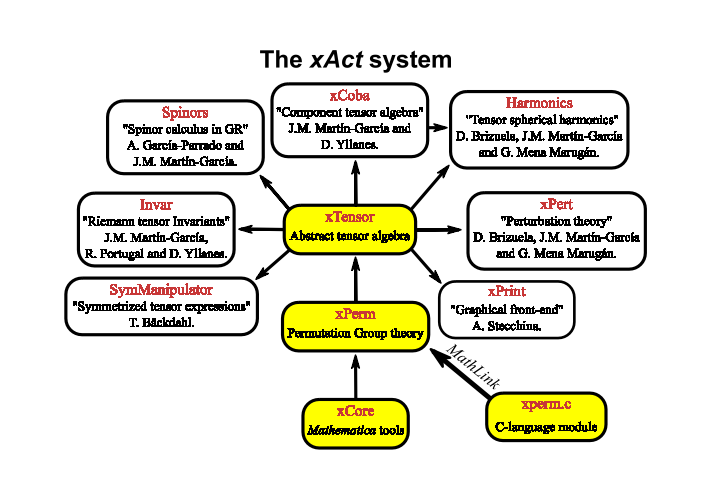

Figure credit: Alfonso Garcia-Parrado Gomez-Loboa and Jose M. Martin-Garcia,  Comput.Phys.Commun. 183 (2012) 2214-2225

## Introduction to xAct

xAct is a very powerful tensor algebra package for Mathematica. 
It is developed and maintained by José M. Martín-García and collaborators. You can get it for free at http://www.xact.es/ .
Amongst others, it can do the following:

Abstract index manipulation & tensor computations:

▽_a▽_b T | a | b |   |   |  
  |   | c | d | e==▽_b▽_a T | a | b |   |   |  
  |   | c | d | e+R[▽] |   |   |   |  
e | f | a | b T | a | b |   |   | f
  |   | c | d |  +R[▽] |   |   |   |  
d | f | a | b T | a | b |   | f |  
  |   | c |   | e+R[▽] |   |   |   |  
c | f | a | b T | a | b | f |   |  
  |   |   | d | e

Component computations

g |   |  
a | b==(-1-r^2/L^2 | 0 | 0
0 | 1/(1+r^2/L^2) | 0
0 | 0 | r^2),    R[▽]==-6/L^2

Perturbations (up to any order!):

△[R[▽]]==-h | 1 | a | b
  |   |   R[▽] |   |  
a | b+▽_b▽_a h | 1 | a | b
  |   |  -▽_b▽^b h | 1 | a |  
  |   | a

Invariants of Riemann tensors:

R[▽] | a | b
  |   R[▽] |   | c | d | e
a |   |   |   R[▽] |   |   |   |  
b | d | c | e==1/2 R[▽] | a | b
  |   R[▽] |   | c | d | e
a |   |   |   R[▽] |   |   |   |  
b | c | d | e

Export to LaTeX!

## Installation of xAct

#### 安装包安放位置

Linux:
   - system-wide: /usr/share/Mathematica/Applications/xAct
   - single-user: $HOME/.Mathematica/Applications/xAct

Mac OS:
   - system-wide: /Library/Mathematica/Applications/xAct
   - single-user: /Users/<user>/Library/Mathematica/Applications/xAct

MSWindows:
   - system-wide: C:\Documents and settings\All Users\Application data\Mathematica\Applications\xAct\
   - single-user: C:\Documents and settings\<user>\Application Data\Mathematica\Applications\xAct\

#### 下载链接

A single file with the current versions (16 February 2020) of all packages can be downloaded: xAct_ 1.1.4.tgz for linux/unix/mac, or xAct_ 1.1.4.zip for windows.

#### 测试环境路径

```mathematica
$Path
```

{E:\11.0\SystemFiles\Links,C:\Users\SJM\AppData\Roaming\Mathematica\Kernel,C:\Users\SJM\AppData\Roaming\Mathematica\Autoload,C:\Users\SJM\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\SJM,E:\11.0\AddOns\Packages,E:\11.0\SystemFiles\Autoload,E:\11.0\AddOns\Autoload,E:\11.0\AddOns\Applications,E:\11.0\AddOns\ExtraPackages,E:\11.0\SystemFiles\Kernel\Packages,E:\11.0\Documentation\English\System,E:\11.0\SystemFiles\Data\ICC,E:\11.0\Documentation\ChineseSimplified\System\}

```mathematica
Dirname="C:\\ProgramData\\Mathematica\\Applications\\xAct";

Quiet@AppendTo[$Path,Dirname];
$Path
```

{E:\11.0\SystemFiles\Links,C:\Users\SJM\AppData\Roaming\Mathematica\Kernel,C:\Users\SJM\AppData\Roaming\Mathematica\Autoload,C:\Users\SJM\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\SJM,E:\11.0\AddOns\Packages,E:\11.0\SystemFiles\Autoload,E:\11.0\AddOns\Autoload,E:\11.0\AddOns\Applications,E:\11.0\AddOns\ExtraPackages,E:\11.0\SystemFiles\Kernel\Packages,E:\11.0\Documentation\English\System,E:\11.0\SystemFiles\Data\ICC,E:\11.0\Documentation\ChineseSimplified\System\,C:\ProgramData\Mathematica\Applications\xAct}

```mathematica
<<xTensor`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

## 爱因斯坦场方程

### 变分法（variation method）：运动方程

Ref. Cosimo Bambi - Introduction to General Relativity, DOI: 10.1007/978-981-13-1090-4

The total action will be the sum of the action of the gravitational sector, say S_g, and of the action of the matter sector, say S_m,

S=S_g+S_m

The natural candidates for the Lagrangian coordinates of the action of the gravitational field are the metric coefficients and their first derivatives.
 The Einstein equations should be obtained by considering the following variation

g_μν→(g̃)_μν=g_μν+δg_μν

with δg_μν=0 at the boundary of the integration region.

δS_g+δS_m=0⇒G_μν−κT_μν=0.

Einstein–Hilbert action is

S_EH=c^3/(16π G_N)∫d^4 x √-g R

or

S_EH=1/(2κ c)∫d^4 x √-g R

-Graphics-

we can rewrite the variation of the Einstein–Hilbert action as

-Graphics-

-Graphics-

Note that the last term in this expression is a divergence

-Graphics-

and therefore we can apply Gauss's theorem to reduce the second integral. The Least Action Principle requires that the variations of the Lagrangian coordinates vanish at the boundary of the integration region, and therefore any surface integral vanishes too.

The Einstein equations is

-Graphics-

### 导入xAct程序包

```mathematica
ClearAll["Global`*"];
<<xAct`xTensor`
<<xAct`xTras`
<<xAct`TexAct`;
Myprint[expr_]:=TexPrint[expr]//TraditionalForm
org[expr_]:=Collect[ContractMetric[expr],$PerturbationParameter,ToCanonical];
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.5, {2020,2,16}

CopyRight (C) 2005-2020, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`TexAct`  version 0.4.2, {2020,2,19}

CopyRight (C) 2008-2020, Thomas Bäckdahl, Jose M. Martin-Garcia and Barry Wardell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

### 定义Manifold, Metric

```mathematica
Index=IndexRange[a,m];
DefManifold[M4,4,Index]
DefMetric[1,gmetric[-a,-b],CD,SymbolOfCovD->{";","∇"},PrintAs->"g"];
```

** DefManifold: Defining manifold M4.

** DefVBundle: Defining vbundle TangentM4.

** DefTensor: Defining symmetric metric tensor gmetric[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilongmetric[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetragmetric[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetragmetric†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Schouten tensor SchoutenCD[-a,-b].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCD[LI[_],-a,-b].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCD[LI[_],-a,-b].

** DefTensor: Defining weight +2 density Detgmetric[]. Determinant.

** DefParameter: Defining parameter PerturbationParametergmetric.

** DefTensor: Defining tensor Perturbationgmetric[LI[order],-a,-b].

```mathematica
?M4
```

Global`M4

DefInfo[M4]^={manifold,}
 
DimOfManifold[M4]^=4
 
ManifoldQ[M4]^=True
 
PrintAs[M4]^=M4
 
ServantsOf[M4]^={𝕋M4}
 
SplittingsOfManifold[M4]^={}
 
VisitorsOf[M4]^={gmetric,epsilongmetric,Tetragmetric,Tetragmetric†,CD,TorsionCD,ChristoffelCD,RiemannCD,RicciCD,RicciScalarCD,EinsteinCD,WeylCD,TFRicciCD,KretschmannCD,SymRiemannCD,SchoutenCD,SchoutenCCCD,EinsteinCCCD,Detgmetric,Perturbationgmetric,xAct`xTras`Private`var$3202}

```mathematica
?TangentM4
```

𝕋M4

BaseOfVBundle[𝕋M4]^=M4
 
Dagger[𝕋M4]^=𝕋M4
 
DefInfo[𝕋M4]^={vbundle,}
 
DimOfVBundle[𝕋M4]^=4
 
IndicesOfVBundle[𝕋M4]^={{a,b,c,d,e,f,g,h,i,j,k,l,m},{}}
 
LastIndex[𝕋M4]^={m,1}
 
MasterOf[𝕋M4]^=M4
 
MetricsOfVBundle[𝕋M4]^={gmetric}
 
PrintAs[𝕋M4]^=𝕋M4
 
SplittingsOfVBundle[𝕋M4]^={}
 
VBundleQ[𝕋M4]^=True
 
VisitorsOf[𝕋M4]^={gmetric,epsilongmetric,Tetragmetric,Tetragmetric†,TorsionCD,ChristoffelCD,RiemannCD,RicciCD,EinsteinCD,WeylCD,TFRicciCD,SymRiemannCD,SchoutenCD,SchoutenCCCD,EinsteinCCCD,Perturbationgmetric,xAct`xTras`Private`var$3202}

```mathematica
?EinsteinCD
```

Global`EinsteinCD

Dagger[EinsteinCD]^:=EinsteinCD
 
DefInfo[EinsteinCD]^:={symmetric Einstein tensor,}
 
DependenciesOfTensor[EinsteinCD]^:={M4}
 
HostsOf[EinsteinCD]^:={M4,𝕋M4}
 
MasterOf[EinsteinCD]^:=CD
 
PrintAs[EinsteinCD]^:=G[∇]
 
SlotsOfTensor[EinsteinCD]^:={-𝕋M4,-𝕋M4}
 
SymmetryGroupOfTensor[EinsteinCD]^:=StrongGenSet[{1,2},GenSet[(1,2)]]
 
TensorID[EinsteinCD]^:={Einstein,CD}
 
xTensorQ[EinsteinCD]^:=True
 
∇_UnderBar[b̲] G[∇] | UnderBar[a̲] | UnderBar[b̲]
  |  ^:=Module[{},0]
 
∇^UnderBar[b̲] G[∇] | UnderBar[a̲] |  
  | UnderBar[b̲]^:=Module[{},0]
 
∇_UnderBar[b̲] G[∇] | UnderBar[b̲] | UnderBar[a̲]
  |  ^:=Module[{},0]
 
∇^UnderBar[b̲] G[∇] |   | UnderBar[a̲]
UnderBar[b̲] |  ^:=Module[{},0]

### 1.含宇宙学常数Λ的Einstein场方程

```mathematica
DefConstantSymbol[Λ]
DefTensor[T[],M4]
```

** DefConstantSymbol: Defining constant symbol Λ.

** DefTensor: Defining tensor T[].

```mathematica
Lag1=RicciScalarCD[]-2Λ
EinsteinTensor=VarL[gmetric[a,b]][Lag1]//Expand
```

-2 Λ+R[∇]

Λ g |   |  
a | b+R[∇] |   |  
a | b-1/2 g |   |  
a | b R[∇]

```mathematica
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[EinsteinCD]^="G";
Print["Einstein场方程为: ",EinsteinTensor==8π G T[-a,-b]]
```

Einstein场方程为: Λ g |   |  
a | b+R |   |  
a | b-1/2 g |   |  
a | b R==8 G π T |   |  
a | b

#### 检查是否满足守恒律 ∇^a T | | a | b=0

```mathematica
EinsteinCD[-a,-b]
CD[a][EinsteinCD[-a,-b]]
```

G |   |  
a | b

0

```mathematica
CD[a][EinsteinTensor]
%//FullSimplification[]
```

∇^a R |   |  
a | b-1/2 g |   |  
a | b ∇^a R

0

#### 清除定义的量

```mathematica
Clear[T]
UndefConstantSymbol[Λ]
```

** UndefConstantSymbol: Undefined constant symbol Λ

### 2. F(R) theories : see L. G. Jaime, et al., arXiv:1206.1642

#### 定义函数 F

```mathematica
DefScalarFunction[F]
```

** DefScalarFunction: Defining scalar function F.

```mathematica
DefTensor[T[],M4]
Lag2=F[RicciScalarCD[]]
GTensor2=VarL[gmetric[a,b]][Lag2]
G1=GTensor2//org
G2=GTensor2//FullSimplification[]//ScreenDollarIndices
Print["F(R)引力场方程为: ",G2==8π G T[-a,-b]]
CD[a][ T[-a,-b]]
Clear[T]
```

** DefTensor: Defining tensor T[].

F[R]

-1/2 F[R] g |   |  
a | b+R |   |  
a | b F'[R]-1/4 ∇_a ∇_b R F''[R]-1/4 ∇_b ∇_a R F''[R]-1/4 g |   |  
b | c ∇^c ∇_a R F''[R]-1/4 g |   |  
a | c ∇^c ∇_b R F''[R]+1/2 g |   |  
a | b ∇^c ∇_c R F''[R]+1/2 g |   |  
a | b g | c | d
  |   ∇_d ∇_c R F''[R]-1/2 ∇_a R ∇_b R F^(3)[R]-1/4 g |   |  
b | c ∇_a R ∇^c R F^(3)[R]-1/4 g |   |  
a | c ∇_b R ∇^c R F^(3)[R]+1/2 g |   |  
a | b ∇_c R ∇^c R F^(3)[R]+1/2 g |   |  
a | b g | c | d
  |   ∇_c R ∇_d R F^(3)[R]

-1/2 F[R] g |   |  
a | b+R |   |  
a | b F'[R]-1/2 ∇_a ∇_b R F''[R]-1/2 ∇_b ∇_a R F''[R]+g |   |  
a | b ∇_c ∇^c R F''[R]-∇_a R ∇_b R F^(3)[R]+g |   |  
a | b ∇_c R ∇^c R F^(3)[R]

-1/2 F[R] g |   |  
a | b+R |   |  
a | b F'[R]-∇_b ∇_a R F''[R]+g |   |  
a | b ∇_c ∇^c R F''[R]-∇_a R ∇_b R F^(3)[R]+g |   |  
a | b ∇_c R ∇^c R F^(3)[R]

F(R)引力场方程为: -1/2 F[R] g |   |  
a | b+R |   |  
a | b F'[R]-∇_b ∇_a R F''[R]+g |   |  
a | b ∇_c ∇^c R F''[R]-∇_a R ∇_b R F^(3)[R]+g |   |  
a | b ∇_c R ∇^c R F^(3)[R]==8 G π T |   |  
a | b

∇^a T |   |  
a | b

#### 检查是否满足守恒律 ∇^a T | | a | b=0

```mathematica
CD[a][-1/2 F[R] {{g, {{, }, {a, b}}}}+{{R, {{, }, {a, b}}}} F'[R]-∇_b ∇_a R F''[R]+{{g, {{, }, {a, b}}}} ∇_c ∇^c R F''[R]-∇_a R ∇_b R Derivative[3][F][R]+{{g, {{, }, {a, b}}}} ∇_c R ∇^c R Derivative[3][F][R]]
%//FullSimplification[]
```

∇^a R |   |  
a | b F'[R]-1/2 g |   |  
a | b ∇^a R F'[R]+R |   |  
a | b ∇^a R F''[R]-∇^a ∇_b ∇_a R F''[R]-∇^a ∇_a R ∇_b R F^(3)[R]-∇^a R ∇_b ∇_a R F^(3)[R]+g |   |  
a | b (∇^a ∇_c ∇^c R F''[R]+∇^a R ∇_c ∇^c R F^(3)[R])-∇_a R (∇^a ∇_b R F^(3)[R]+∇^a R ∇_b R F^(4)[R])+g |   |  
a | b (∇^a ∇_c R ∇^c R F^(3)[R]+∇_c R (∇^a ∇^c R F^(3)[R]+∇^a R ∇^c R F^(4)[R]))

0

## 修改引力理论(Horndeski理论)的运动方程及其分量计算

xIST/COPPER: General scalar-tensor theories and perturbations

### 1. Horndeski theories: the most general scalar-tensor theories with second-order field equations, see Tsutomu Kobayashi, et al., arXiv:1105.5723

We thus consider a gravity + scalar system described by the action

-Graphics-

-Graphics-

-Graphics-

where R is the Ricci tensor, G_µν is the Einstein tensor, K and G_i are arbitrary functions of ϕ , X.

-Graphics-

#### (1)构造Horndeski作用量

```mathematica
ClearAll["Global`*"];
<<xAct`xTensor`
<<xAct`xTras`
<<xAct`TexAct`;
Myprint[expr_]:=TexPrint[expr]//TraditionalForm
org[expr_]:=Collect[ContractMetric[expr],$PerturbationParameter,ToCanonical];
Index=IndexRange[a,m];
DefManifold[M4,4,Index]
DefMetric[1,gmetric[-a,-b],CD,SymbolOfCovD->{";","∇"},PrintAs->"g"];
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[EinsteinCD]^="G";
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.5, {2020,2,16}

CopyRight (C) 2005-2020, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`TexAct`  version 0.4.2, {2020,2,19}

CopyRight (C) 2008-2020, Thomas Bäckdahl, Jose M. Martin-Garcia and Barry Wardell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefManifold: Defining manifold M4.

** DefVBundle: Defining vbundle TangentM4.

** DefTensor: Defining symmetric metric tensor gmetric[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilongmetric[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetragmetric[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetragmetric†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Schouten tensor SchoutenCD[-a,-b].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCD[LI[_],-a,-b].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCD[LI[_],-a,-b].

** DefTensor: Defining weight +2 density Detgmetric[]. Determinant.

** DefParameter: Defining parameter PerturbationParametergmetric.

** DefTensor: Defining tensor Perturbationgmetric[LI[order],-a,-b].

```mathematica
Clear[ϕ,X];
DefTensor[ϕ[],M4]
DefTensor[X[],M4]
DefScalarFunction[K]
DefScalarFunction[G3]
DefScalarFunction[G4]
DefScalarFunction[G5]
L2=K[ϕ[],X[]]
L3=-G3[ϕ[],X[]]CD[a][CD[-a][ϕ[]]]//SeparateMetric[]
L4=G4[ϕ[],X[]]RicciScalarCD[]+D[G4[ϕ[],X[]],X[]](CD[a][CD[-a][ϕ[]]]CD[b][CD[-b][ϕ[]]]-CD[b][CD[a][ϕ[]]]CD[-b][CD[-a][ϕ[]]])//SeparateMetric[]
L5=G5[ϕ[],X[]]EinsteinCD[-a,-b]CD[b][CD[a][ϕ[]]]-1/6 D[G5[ϕ[],X[]],X[]](CD[a][CD[-a][ϕ[]]]CD[b][CD[-b][ϕ[]]]CD[c][CD[-c][ϕ[]]]-3CD[c][CD[-c][ϕ[]]]CD[b][CD[a][ϕ[]]]CD[-b][CD[-a][ϕ[]]]+2CD[-b][CD[-a][ϕ[]]]CD[a][CD[c][ϕ[]]]CD[-c][CD[b][ϕ[]]])//SeparateMetric[]
LHorndeski=L2+L3+L4+L5
```

** DefTensor: Defining tensor ϕ[].

** DefTensor: Defining tensor X[].

** DefScalarFunction: Defining scalar function K.

** DefScalarFunction: Defining scalar function G3.

** DefScalarFunction: Defining scalar function G4.

** DefScalarFunction: Defining scalar function G5.

K[ϕ,X]

-G3[ϕ,X] g | a | b
  |   ∇_b ∇_a ϕ

G4[ϕ,X] R+(-g | a | c
  |   g | b | d
  |   ∇_b ∇_a ϕ ∇_d ∇_c ϕ+g | a | e
  |   g | b | f
  |   ∇_e ∇_a ϕ ∇_f ∇_b ϕ) G4^(0,1)[ϕ,X]

G |   |  
a | b G5[ϕ,X] g | a | c
  |   g | b | d
  |   ∇_d ∇_c ϕ-1/6 (2 g | a | e
  |   g | b | f
  |   g | c | d
  |   ∇_b ∇_a ϕ ∇_c ∇_f ϕ ∇_e ∇_d ϕ-3 g | a | g
  |   g | b | h
  |   g | c | i
  |   ∇_b ∇_a ϕ ∇_h ∇_g ϕ ∇_i ∇_c ϕ+g | a | j
  |   g | b | k
  |   g | c | l
  |   ∇_j ∇_a ϕ ∇_k ∇_b ϕ ∇_l ∇_c ϕ) G5^(0,1)[ϕ,X]

K[ϕ,X]+G4[ϕ,X] R-G3[ϕ,X] g | a | b
  |   ∇_b ∇_a ϕ+G |   |  
a | b G5[ϕ,X] g | a | c
  |   g | b | d
  |   ∇_d ∇_c ϕ+(-g | a | c
  |   g | b | d
  |   ∇_b ∇_a ϕ ∇_d ∇_c ϕ+g | a | e
  |   g | b | f
  |   ∇_e ∇_a ϕ ∇_f ∇_b ϕ) G4^(0,1)[ϕ,X]-1/6 (2 g | a | e
  |   g | b | f
  |   g | c | d
  |   ∇_b ∇_a ϕ ∇_c ∇_f ϕ ∇_e ∇_d ϕ-3 g | a | g
  |   g | b | h
  |   g | c | i
  |   ∇_b ∇_a ϕ ∇_h ∇_g ϕ ∇_i ∇_c ϕ+g | a | j
  |   g | b | k
  |   g | c | l
  |   ∇_j ∇_a ϕ ∇_k ∇_b ϕ ∇_l ∇_c ϕ) G5^(0,1)[ϕ,X]

#### (2)给出ϕ场和引力场的运动方程

Varying the action, we obtain

-Graphics-

The gravitational- and scalar-field equations are thus given by

-Graphics-

Note that the Lagrangian includes the derivatives of the field, up to the second order. Therefore, we have

-Graphics-

```mathematica
Xs=-1/2 gmetric[i,j]CD[-i][ϕ[]]CD[-j][ϕ[]];
VarLX[T0_]:=Module[{T=T0},TX=D[T,X[]]//org;TXij=TX/.{a->i,b->j};VarL[gmetric[a,b]][T]+TXij  VarD[gmetric[a,b]][Xs]]
VarDϕ[T0_]:=Module[{T=T0},D[T,ϕ[]]+D[T,X[]]VarD[ϕ[],CD][Xs]]

Clear[Pϕ,PPϕ]
DefTensor[Pϕ[],M4]
DefTensor[PPϕ[],M4]

SimplifyP1[T_]:=Module[{T0=T},IC1=Table[index=Index[[i1]];CD[-index][ϕ[]]->Pϕ[-index],{i1,1,Length[Index]}];
IC2=Table[index=Index[[i1]];index2=Index[[j1]];
CD[-index2][Pϕ[-index]]->PPϕ[-index,-index2],{i1,1,Length[Index]},{j1,1,Length[Index]}]//Flatten;T0/.IC1/.IC2]
SimplifyP2[T_]:=Module[{T0=T},IC1=Table[index=Index[[i1]];Pϕ[-index]->CD[-index][ϕ[]],{i1,1,Length[Index]}];
IC2=Table[index=Index[[i1]];index2=Index[[j1]];
{PPϕ[index,-index2]->CD[-index2][Pϕ[index]],PPϕ[-index,-index2]->CD[-index2][Pϕ[-index]],PPϕ[-index,index2]->CD[index2][Pϕ[-index]]},
{i1,1,Length[Index]},{j1,1,Length[Index]}]//Flatten;T0/.IC2/.IC1]

Xsnew=Xs//SimplifyP1

VarDJϕ[T0_]:=Module[{T=T0},VarD[Pϕ[-i],CD][T]-CD[-b][VarD[PPϕ[-i,-b],CD][T]]+0*(D[T,X[]])VarD[Pϕ[-i],CD][Xsnew]]//org
VarDJϕ2[T0_]:=Module[{T=T0},VarD[Pϕ[-i],CD][T]-CD[-b][VarD[PPϕ[-i,-b],CD][T]]+1*(D[T,X[]])VarD[Pϕ[-i],CD][Xsnew]]//org
VarDPϕ[T0_]:=Module[{T=T0},D[T,ϕ[]]//org]

L3new=-G3[ϕ,X] {{g, {{a, b}, {, }}}} ∇_b ∇_a ϕ//SimplifyP1
L4new=G4[ϕ,X] R+(-{{g, {{a, c}, {, }}}} {{g, {{b, d}, {, }}}} ∇_b ∇_a ϕ ∇_d ∇_c ϕ+{{g, {{a, e}, {, }}}} {{g, {{b, f}, {, }}}} ∇_e ∇_a ϕ ∇_f ∇_b ϕ) Derivative[0,1][G4][ϕ,X]//SimplifyP1
L5new={{G, {{, }, {a, b}}}} G5[ϕ,X] {{g, {{a, c}, {, }}}} {{g, {{b, d}, {, }}}} ∇_d ∇_c ϕ-1/6 (2 {{g, {{a, e}, {, }}}} {{g, {{b, f}, {, }}}} {{g, {{c, d}, {, }}}} ∇_b ∇_a ϕ ∇_c ∇_f ϕ ∇_e ∇_d ϕ-3 {{g, {{a, g}, {, }}}} {{g, {{b, h}, {, }}}} {{g, {{c, i}, {, }}}} ∇_b ∇_a ϕ ∇_h ∇_g ϕ ∇_i ∇_c ϕ+{{g, {{a, j}, {, }}}} {{g, {{b, k}, {, }}}} {{g, {{c, l}, {, }}}} ∇_j ∇_a ϕ ∇_k ∇_b ϕ ∇_l ∇_c ϕ) Derivative[0,1][G5][ϕ,X]//SimplifyP1
```

** DefTensor: Defining tensor Pϕ[].

** DefTensor: Defining tensor PPϕ[].

-1/2 g | i | j
  |   Pϕ |  
i Pϕ |  
j

-G3[ϕ,X] g | a | b
  |   PPϕ |   |  
a | b

G4[ϕ,X] R+(g | a | e
  |   g | b | f
  |   PPϕ |   |  
a | e PPϕ |   |  
b | f-g | a | c
  |   g | b | d
  |   PPϕ |   |  
a | b PPϕ |   |  
c | d) G4^(0,1)[ϕ,X]

G |   |  
a | b G5[ϕ,X] g | a | c
  |   g | b | d
  |   PPϕ |   |  
c | d-1/6 (g | a | j
  |   g | b | k
  |   g | c | l
  |   PPϕ |   |  
a | j PPϕ |   |  
b | k PPϕ |   |  
c | l+2 g | a | e
  |   g | b | f
  |   g | c | d
  |   PPϕ |   |  
a | b PPϕ |   |  
d | e PPϕ |   |  
f | c-3 g | a | g
  |   g | b | h
  |   g | c | i
  |   PPϕ |   |  
a | b PPϕ |   |  
c | i PPϕ |   |  
g | h) G5^(0,1)[ϕ,X]

Check Eqs. (B6)-(B13) in arXiv:1105.5723

```mathematica
SimplifyP3[T_]:=Module[{T0=T},IC1=Table[index=Index[[i1]];{Pϕ[-index]->CD[-index][ϕ[]],Pϕ[index]->CD[index][ϕ[]]},{i1,1,Length[Index]}]//Flatten;
IC2=Table[index=Index[[i1]];index2=Index[[j1]];{PPϕ[index,index2]->CD[index2][CD[index][ϕ[]]],PPϕ[index,-index2]->CD[-index2][CD[index][ϕ[]]],PPϕ[-index,-index2]->CD[-index2][CD[-index][ϕ[]]],PPϕ[-index,index2]->CD[index2][CD[-index][ϕ[]]]},{i1,1,Length[Index]},{j1,1,Length[Index]}]//Flatten;
T0/.IC2/.IC1]
Pϕ2=VarDPϕ[L2]//ReplaceDummies
Pϕ3=VarDPϕ[L3new]//ReplaceDummies
Pϕ4=VarDPϕ[L4new]//ReplaceDummies
VarDPϕ[L5new]//ReplaceDummies//SimplifyP2;
Pϕ5=Collect[%,Derivative[1,1][G5][ϕ,X]]
```

K^(1,0)[ϕ,X]

-PPϕ | a |  
  | a G3^(1,0)[ϕ,X]

R G4^(1,0)[ϕ,X]-PPϕ |   |  
a | b PPϕ | a | b
  |   G4^(1,1)[ϕ,X]+PPϕ | a |  
  | a PPϕ | b |  
  | b G4^(1,1)[ϕ,X]

G |   |  
a | b PPϕ | a | b
  |   G5^(1,0)[ϕ,X]+(1/2 PPϕ | a |  
  | a PPϕ |   |  
b | c PPϕ | b | c
  |  -1/3 PPϕ | a | b
  |   PPϕ |   | c
b |   PPϕ |   |  
c | a-1/6 PPϕ | a |  
  | a PPϕ | b |  
  | b PPϕ | c |  
  | c) G5^(1,1)[ϕ,X]

```mathematica
Derivative[1,0][K][ϕ,X]//SimplifyP3
-{{PPϕ, {{a, }, {, a}}}} Derivative[1,0][G3][ϕ,X]//SimplifyP3
R Derivative[1,0][G4][ϕ,X]-{{PPϕ, {{, }, {a, b}}}} {{PPϕ, {{a, b}, {, }}}} Derivative[1,1][G4][ϕ,X]+{{PPϕ, {{a, }, {, a}}}} {{PPϕ, {{b, }, {, b}}}} Derivative[1,1][G4][ϕ,X]//SimplifyP3
{{G, {{, }, {a, b}}}} {{PPϕ, {{a, b}, {, }}}} Derivative[1,0][G5][ϕ,X]+(1/2 {{PPϕ, {{a, }, {, a}}}} {{PPϕ, {{, }, {b, c}}}} {{PPϕ, {{b, c}, {, }}}}-1/3 {{PPϕ, {{a, b}, {, }}}} {{PPϕ, {{, c}, {b, }}}} {{PPϕ, {{, }, {c, a}}}}-1/6 {{PPϕ, {{a, }, {, a}}}} {{PPϕ, {{b, }, {, b}}}} {{PPϕ, {{c, }, {, c}}}}) Derivative[1,1][G5][ϕ,X]//SimplifyP3
```

K^(1,0)[ϕ,X]

-∇_a ∇^a ϕ G3^(1,0)[ϕ,X]

R G4^(1,0)[ϕ,X]+∇_a ∇^a ϕ ∇_b ∇^b ϕ G4^(1,1)[ϕ,X]-∇_b ∇_a ϕ ∇^b ∇^a ϕ G4^(1,1)[ϕ,X]

G |   |  
a | b ∇^b ∇^a ϕ G5^(1,0)[ϕ,X]+(-1/6 ∇_a ∇^a ϕ ∇_b ∇^b ϕ ∇_c ∇^c ϕ-1/3 ∇_a ∇_c ϕ ∇^b ∇^a ϕ ∇^c ∇_b ϕ+1/2 ∇_a ∇^a ϕ ∇_c ∇_b ϕ ∇^c ∇^b ϕ) G5^(1,1)[ϕ,X]

-Graphics-

```mathematica
J2=VarDJϕ[L2]//ReplaceDummies//SimplifyP2
J3=VarDJϕ[L3new]//ReplaceDummies//SimplifyP2
J4=VarDJϕ[L4new]//ReplaceDummies//SimplifyP2
VarDJϕ[L5new]//ReplaceDummies//SimplifyP2;
J5=Collect[%,{Derivative[1,1][G5][ϕ,X],Derivative[0,1][G5][ϕ,X],Derivative[0,2][G5][ϕ,X]}]
```

0

∇^i X G3^(0,1)[ϕ,X]+∇^i ϕ G3^(1,0)[ϕ,X]

2 ∇_a PPϕ | i | a
  |   G4^(0,1)[ϕ,X]-2 ∇^i PPϕ | a |  
  | a G4^(0,1)[ϕ,X]+2 PPϕ | i | a
  |   ∇_a X G4^(0,2)[ϕ,X]-2 PPϕ | a |  
  | a ∇^i X G4^(0,2)[ϕ,X]+2 PPϕ | i | a
  |   ∇_a ϕ G4^(1,1)[ϕ,X]-2 PPϕ | a |  
  | a ∇^i ϕ G4^(1,1)[ϕ,X]

(PPϕ | a | b
  |   ∇_a PPϕ |   | i
b |  -PPϕ | i | a
  |   ∇_a PPϕ | b |  
  | b-G | i |  
  | a ∇^a X+PPϕ | a | i
  |   ∇_b PPϕ | b |  
  | a-PPϕ | a |  
  | a ∇_b PPϕ | i | b
  |  -PPϕ | a | b
  |   ∇^i PPϕ |   |  
a | b+PPϕ | a |  
  | a ∇^i PPϕ | b |  
  | b) G5^(0,1)[ϕ,X]+(-PPϕ | b |  
  | b PPϕ | i | a
  |   ∇_a X+PPϕ | a | i
  |   PPϕ | b |  
  | a ∇_b X-1/2 PPϕ |   |  
a | b PPϕ | a | b
  |   ∇^i X+1/2 PPϕ | a |  
  | a PPϕ | b |  
  | b ∇^i X) G5^(0,2)[ϕ,X]-G | i |  
  | a ∇^a ϕ G5^(1,0)[ϕ,X]+(-PPϕ | b |  
  | b PPϕ | i | a
  |   ∇_a ϕ+PPϕ | a | i
  |   PPϕ | b |  
  | a ∇_b ϕ-1/2 PPϕ |   |  
a | b PPϕ | a | b
  |   ∇^i ϕ+1/2 PPϕ | a |  
  | a PPϕ | b |  
  | b ∇^i ϕ) G5^(1,1)[ϕ,X]

```mathematica
0
∇^i X Derivative[0,1][G3][ϕ,X]+∇^i ϕ Derivative[1,0][G3][ϕ,X]//SimplifyP3
2 ∇_a {{PPϕ, {{i, a}, {, }}}} Derivative[0,1][G4][ϕ,X]-2 ∇^i {{PPϕ, {{a, }, {, a}}}} Derivative[0,1][G4][ϕ,X]+2 {{PPϕ, {{i, a}, {, }}}} ∇_a X Derivative[0,2][G4][ϕ,X]-2 {{PPϕ, {{a, }, {, a}}}} ∇^i X Derivative[0,2][G4][ϕ,X]+2 {{PPϕ, {{i, a}, {, }}}} ∇_a ϕ Derivative[1,1][G4][ϕ,X]-2 {{PPϕ, {{a, }, {, a}}}} ∇^i ϕ Derivative[1,1][G4][ϕ,X]//SimplifyP3;
%//SortCovDs//FullSimplification[];
Collect[%,{Derivative[0,2][G4][ϕ,X],Derivative[1,1][G4][ϕ,X]}]
({{PPϕ, {{a, b}, {, }}}} ∇_a {{PPϕ, {{, i}, {b, }}}}-{{PPϕ, {{i, a}, {, }}}} ∇_a {{PPϕ, {{b, }, {, b}}}}-{{G, {{i, }, {, a}}}} ∇^a X+{{PPϕ, {{a, i}, {, }}}} ∇_b {{PPϕ, {{b, }, {, a}}}}-{{PPϕ, {{a, }, {, a}}}} ∇_b {{PPϕ, {{i, b}, {, }}}}-{{PPϕ, {{a, b}, {, }}}} ∇^i {{PPϕ, {{, }, {a, b}}}}+{{PPϕ, {{a, }, {, a}}}} ∇^i {{PPϕ, {{b, }, {, b}}}}) Derivative[0,1][G5][ϕ,X]+(-{{PPϕ, {{b, }, {, b}}}} {{PPϕ, {{i, a}, {, }}}} ∇_a X+{{PPϕ, {{a, i}, {, }}}} {{PPϕ, {{b, }, {, a}}}} ∇_b X-1/2 {{PPϕ, {{, }, {a, b}}}} {{PPϕ, {{a, b}, {, }}}} ∇^i X+1/2 {{PPϕ, {{a, }, {, a}}}} {{PPϕ, {{b, }, {, b}}}} ∇^i X) Derivative[0,2][G5][ϕ,X]-{{G, {{i, }, {, a}}}} ∇^a ϕ Derivative[1,0][G5][ϕ,X]+(-{{PPϕ, {{b, }, {, b}}}} {{PPϕ, {{i, a}, {, }}}} ∇_a ϕ+{{PPϕ, {{a, i}, {, }}}} {{PPϕ, {{b, }, {, a}}}} ∇_b ϕ-1/2 {{PPϕ, {{, }, {a, b}}}} {{PPϕ, {{a, b}, {, }}}} ∇^i ϕ+1/2 {{PPϕ, {{a, }, {, a}}}} {{PPϕ, {{b, }, {, b}}}} ∇^i ϕ) Derivative[1,1][G5][ϕ,X]//SimplifyP3;
%//SortCovDs//FullSimplification[];
Collect[%,{Derivative[1,1][G5][ϕ,X],Derivative[0,1][G5][ϕ,X],Derivative[0,2][G5][ϕ,X]}]
```

0

∇^i X G3^(0,1)[ϕ,X]+∇^i ϕ G3^(1,0)[ϕ,X]

2 R | i |  
  | a ∇^a ϕ G4^(0,1)[ϕ,X]+(-2 ∇_a ∇^a ϕ ∇^i X+2 ∇^a X ∇^i ∇_a ϕ) G4^(0,2)[ϕ,X]+(-2 ∇_a ∇^a ϕ ∇^i ϕ+2 ∇^a ϕ ∇^i ∇_a ϕ) G4^(1,1)[ϕ,X]

(-G | i |  
  | a ∇^a X-R | i |  
  | a ∇^a ϕ ∇_b ∇^b ϕ+R | i |   |   |  
  | b | a | c ∇^a ϕ ∇^c ∇^b ϕ+R |   |  
a | b ∇^a ϕ ∇^i ∇^b ϕ) G5^(0,1)[ϕ,X]+(1/2 ∇_a ∇^a ϕ ∇_b ∇^b ϕ ∇^i X-1/2 ∇_b ∇_a ϕ ∇^b ∇^a ϕ ∇^i X-∇^a X ∇_b ∇^b ϕ ∇^i ∇_a ϕ+∇^a X ∇_b ∇_a ϕ ∇^i ∇^b ϕ) G5^(0,2)[ϕ,X]-G | i |  
  | a ∇^a ϕ G5^(1,0)[ϕ,X]+(1/2 ∇_a ∇^a ϕ ∇_b ∇^b ϕ ∇^i ϕ-1/2 ∇_b ∇_a ϕ ∇^b ∇^a ϕ ∇^i ϕ-∇^a ϕ ∇_b ∇^b ϕ ∇^i ∇_a ϕ+∇^a ϕ ∇_b ∇_a ϕ ∇^i ∇^b ϕ) G5^(1,1)[ϕ,X]

-Graphics-

```mathematica
J2=VarDJϕ2[L2]//ReplaceDummies//SimplifyP2;
J3=VarDJϕ2[L3new]//ReplaceDummies//SimplifyP2;
J4=VarDJϕ2[L4new]//ReplaceDummies//SimplifyP2;
VarDJϕ2[L5new]//ReplaceDummies//SimplifyP2;
J5=Collect[%,{Derivative[1,1][G5][ϕ,X],Derivative[0,1][G5][ϕ,X],Derivative[0,2][G5][ϕ,X]}];
Pϕs=Pϕ2+Pϕ3+Pϕ4+Pϕ5
Ja=J2+J3+J4+J5/.j->i
```

-PPϕ | a |  
  | a G3^(1,0)[ϕ,X]+R G4^(1,0)[ϕ,X]+G |   |  
a | b PPϕ | a | b
  |   G5^(1,0)[ϕ,X]+K^(1,0)[ϕ,X]-PPϕ |   |  
a | b PPϕ | a | b
  |   G4^(1,1)[ϕ,X]+PPϕ | a |  
  | a PPϕ | b |  
  | b G4^(1,1)[ϕ,X]+(1/2 PPϕ | a |  
  | a PPϕ |   |  
b | c PPϕ | b | c
  |  -1/3 PPϕ | a | b
  |   PPϕ |   | c
b |   PPϕ |   |  
c | a-1/6 PPϕ | a |  
  | a PPϕ | b |  
  | b PPϕ | c |  
  | c) G5^(1,1)[ϕ,X]

PPϕ | a |  
  | a Pϕ | i
  G3^(0,1)[ϕ,X]+∇^i X G3^(0,1)[ϕ,X]-Pϕ | i
  R G4^(0,1)[ϕ,X]+2 ∇_a PPϕ | i | a
  |   G4^(0,1)[ϕ,X]-2 ∇^i PPϕ | a |  
  | a G4^(0,1)[ϕ,X]+(-G |   |  
a | b PPϕ | a | b
  |   Pϕ | i
 +PPϕ | a | b
  |   ∇_a PPϕ |   | i
b |  -PPϕ | i | a
  |   ∇_a PPϕ | b |  
  | b-G | i |  
  | a ∇^a X+PPϕ | a | i
  |   ∇_b PPϕ | b |  
  | a-PPϕ | a |  
  | a ∇_b PPϕ | i | b
  |  -PPϕ | a | b
  |   ∇^i PPϕ |   |  
a | b+PPϕ | a |  
  | a ∇^i PPϕ | b |  
  | b) G5^(0,1)[ϕ,X]-Pϕ | i
  K^(0,1)[ϕ,X]+PPϕ |   |  
a | b PPϕ | a | b
  |   Pϕ | i
  G4^(0,2)[ϕ,X]-PPϕ | a |  
  | a PPϕ | b |  
  | b Pϕ | i
  G4^(0,2)[ϕ,X]+2 PPϕ | i | a
  |   ∇_a X G4^(0,2)[ϕ,X]-2 PPϕ | a |  
  | a ∇^i X G4^(0,2)[ϕ,X]+(-1/2 PPϕ | a |  
  | a PPϕ |   |  
b | c PPϕ | b | c
  |   Pϕ | i
 +1/3 PPϕ | a | b
  |   PPϕ |   | c
b |   PPϕ |   |  
c | a Pϕ | i
 +1/6 PPϕ | a |  
  | a PPϕ | b |  
  | b PPϕ | c |  
  | c Pϕ | i
 -PPϕ | b |  
  | b PPϕ | i | a
  |   ∇_a X+PPϕ | a | i
  |   PPϕ | b |  
  | a ∇_b X-1/2 PPϕ |   |  
a | b PPϕ | a | b
  |   ∇^i X+1/2 PPϕ | a |  
  | a PPϕ | b |  
  | b ∇^i X) G5^(0,2)[ϕ,X]+∇^i ϕ G3^(1,0)[ϕ,X]-G | i |  
  | a ∇^a ϕ G5^(1,0)[ϕ,X]+2 PPϕ | i | a
  |   ∇_a ϕ G4^(1,1)[ϕ,X]-2 PPϕ | a |  
  | a ∇^i ϕ G4^(1,1)[ϕ,X]+(-PPϕ | b |  
  | b PPϕ | i | a
  |   ∇_a ϕ+PPϕ | a | i
  |   PPϕ | b |  
  | a ∇_b ϕ-1/2 PPϕ |   |  
a | b PPϕ | a | b
  |   ∇^i ϕ+1/2 PPϕ | a |  
  | a PPϕ | b |  
  | b ∇^i ϕ) G5^(1,1)[ϕ,X]

```mathematica
Pϕs2=-{{PPϕ, {{a, }, {, a}}}} Derivative[1,0][G3][ϕ,X]+R Derivative[1,0][G4][ϕ,X]+{{G, {{, }, {a, b}}}} {{PPϕ, {{a, b}, {, }}}} Derivative[1,0][G5][ϕ,X]+Derivative[1,0][K][ϕ,X]-{{PPϕ, {{, }, {a, b}}}} {{PPϕ, {{a, b}, {, }}}} Derivative[1,1][G4][ϕ,X]+{{PPϕ, {{a, }, {, a}}}} {{PPϕ, {{b, }, {, b}}}} Derivative[1,1][G4][ϕ,X]+(1/2 {{PPϕ, {{a, }, {, a}}}} {{PPϕ, {{, }, {b, c}}}} {{PPϕ, {{b, c}, {, }}}}-1/3 {{PPϕ, {{a, b}, {, }}}} {{PPϕ, {{, c}, {b, }}}} {{PPϕ, {{, }, {c, a}}}}-1/6 {{PPϕ, {{a, }, {, a}}}} {{PPϕ, {{b, }, {, b}}}} {{PPϕ, {{c, }, {, c}}}}) Derivative[1,1][G5][ϕ,X]//SimplifyP3
```

-∇_a ∇^a ϕ G3^(1,0)[ϕ,X]+R G4^(1,0)[ϕ,X]+G |   |  
a | b ∇^b ∇^a ϕ G5^(1,0)[ϕ,X]+K^(1,0)[ϕ,X]+∇_a ∇^a ϕ ∇_b ∇^b ϕ G4^(1,1)[ϕ,X]-∇_b ∇_a ϕ ∇^b ∇^a ϕ G4^(1,1)[ϕ,X]+(-1/6 ∇_a ∇^a ϕ ∇_b ∇^b ϕ ∇_c ∇^c ϕ-1/3 ∇_a ∇_c ϕ ∇^b ∇^a ϕ ∇^c ∇_b ϕ+1/2 ∇_a ∇^a ϕ ∇_c ∇_b ϕ ∇^c ∇^b ϕ) G5^(1,1)[ϕ,X]

```mathematica
Ja2={{PPϕ, {{a, }, {, a}}}} {{Pϕ, {{i}, {}}}} Derivative[0,1][G3][ϕ,X]+∇^i X Derivative[0,1][G3][ϕ,X]-{{Pϕ, {{i}, {}}}} R Derivative[0,1][G4][ϕ,X]+2 ∇_a {{PPϕ, {{i, a}, {, }}}} Derivative[0,1][G4][ϕ,X]-2 ∇^i {{PPϕ, {{a, }, {, a}}}} Derivative[0,1][G4][ϕ,X]-{{G, {{, }, {a, b}}}} {{PPϕ, {{a, b}, {, }}}} {{Pϕ, {{i}, {}}}} Derivative[0,1][G5][ϕ,X]+{{PPϕ, {{a, b}, {, }}}} ∇_a {{PPϕ, {{, i}, {b, }}}} Derivative[0,1][G5][ϕ,X]-{{PPϕ, {{i, a}, {, }}}} ∇_a {{PPϕ, {{b, }, {, b}}}} Derivative[0,1][G5][ϕ,X]-{{G, {{i, }, {, a}}}} ∇^a X Derivative[0,1][G5][ϕ,X]+{{PPϕ, {{a, i}, {, }}}} ∇_b {{PPϕ, {{b, }, {, a}}}} Derivative[0,1][G5][ϕ,X]-{{PPϕ, {{a, }, {, a}}}} ∇_b {{PPϕ, {{i, b}, {, }}}} Derivative[0,1][G5][ϕ,X]-{{PPϕ, {{a, b}, {, }}}} ∇^i {{PPϕ, {{, }, {a, b}}}} Derivative[0,1][G5][ϕ,X]+{{PPϕ, {{a, }, {, a}}}} ∇^i {{PPϕ, {{b, }, {, b}}}} Derivative[0,1][G5][ϕ,X]-{{Pϕ, {{i}, {}}}} Derivative[0,1][K][ϕ,X]+{{PPϕ, {{, }, {a, b}}}} {{PPϕ, {{a, b}, {, }}}} {{Pϕ, {{i}, {}}}} Derivative[0,2][G4][ϕ,X]-{{PPϕ, {{a, }, {, a}}}} {{PPϕ, {{b, }, {, b}}}} {{Pϕ, {{i}, {}}}} Derivative[0,2][G4][ϕ,X]+2 {{PPϕ, {{i, a}, {, }}}} ∇_a X Derivative[0,2][G4][ϕ,X]-2 {{PPϕ, {{a, }, {, a}}}} ∇^i X Derivative[0,2][G4][ϕ,X]-1/2 {{PPϕ, {{a, }, {, a}}}} {{PPϕ, {{, }, {b, c}}}} {{PPϕ, {{b, c}, {, }}}} {{Pϕ, {{i}, {}}}} Derivative[0,2][G5][ϕ,X]+1/3 {{PPϕ, {{a, b}, {, }}}} {{PPϕ, {{, c}, {b, }}}} {{PPϕ, {{, }, {c, a}}}} {{Pϕ, {{i}, {}}}} Derivative[0,2][G5][ϕ,X]+1/6 {{PPϕ, {{a, }, {, a}}}} {{PPϕ, {{b, }, {, b}}}} {{PPϕ, {{c, }, {, c}}}} {{Pϕ, {{i}, {}}}} Derivative[0,2][G5][ϕ,X]-{{PPϕ, {{b, }, {, b}}}} {{PPϕ, {{i, a}, {, }}}} ∇_a X Derivative[0,2][G5][ϕ,X]+{{PPϕ, {{a, i}, {, }}}} {{PPϕ, {{b, }, {, a}}}} ∇_b X Derivative[0,2][G5][ϕ,X]-1/2 {{PPϕ, {{, }, {a, b}}}} {{PPϕ, {{a, b}, {, }}}} ∇^i X Derivative[0,2][G5][ϕ,X]+1/2 {{PPϕ, {{a, }, {, a}}}} {{PPϕ, {{b, }, {, b}}}} ∇^i X Derivative[0,2][G5][ϕ,X]+∇^i ϕ Derivative[1,0][G3][ϕ,X]-{{G, {{i, }, {, a}}}} ∇^a ϕ Derivative[1,0][G5][ϕ,X]+2 {{PPϕ, {{i, a}, {, }}}} ∇_a ϕ Derivative[1,1][G4][ϕ,X]-2 {{PPϕ, {{a, }, {, a}}}} ∇^i ϕ Derivative[1,1][G4][ϕ,X]-{{PPϕ, {{b, }, {, b}}}} {{PPϕ, {{i, a}, {, }}}} ∇_a ϕ Derivative[1,1][G5][ϕ,X]+{{PPϕ, {{a, i}, {, }}}} {{PPϕ, {{b, }, {, a}}}} ∇_b ϕ Derivative[1,1][G5][ϕ,X]-1/2 {{PPϕ, {{, }, {a, b}}}} {{PPϕ, {{a, b}, {, }}}} ∇^i ϕ Derivative[1,1][G5][ϕ,X]+1/2 {{PPϕ, {{a, }, {, a}}}} {{PPϕ, {{b, }, {, b}}}} ∇^i ϕ Derivative[1,1][G5][ϕ,X]//SimplifyP3
```

∇^i X G3^(0,1)[ϕ,X]+∇_a ∇^a ϕ ∇^i ϕ G3^(0,1)[ϕ,X]+2 ∇_a ∇^a ∇^i ϕ G4^(0,1)[ϕ,X]-R ∇^i ϕ G4^(0,1)[ϕ,X]-2 ∇^i ∇_a ∇^a ϕ G4^(0,1)[ϕ,X]-G | i |  
  | a ∇^a X G5^(0,1)[ϕ,X]-∇_a ∇_b ∇^b ϕ ∇^a ∇^i ϕ G5^(0,1)[ϕ,X]-∇_a ∇^a ϕ ∇_b ∇^b ∇^i ϕ G5^(0,1)[ϕ,X]+∇_a ∇^i ∇_b ϕ ∇^b ∇^a ϕ G5^(0,1)[ϕ,X]-G |   |  
a | b ∇^b ∇^a ϕ ∇^i ϕ G5^(0,1)[ϕ,X]+∇_b ∇_a ∇^b ϕ ∇^i ∇^a ϕ G5^(0,1)[ϕ,X]-∇^b ∇^a ϕ ∇^i ∇_b ∇_a ϕ G5^(0,1)[ϕ,X]+∇_a ∇^a ϕ ∇^i ∇_b ∇^b ϕ G5^(0,1)[ϕ,X]-∇^i ϕ K^(0,1)[ϕ,X]+2 ∇_a X ∇^a ∇^i ϕ G4^(0,2)[ϕ,X]-2 ∇_a ∇^a ϕ ∇^i X G4^(0,2)[ϕ,X]-∇_a ∇^a ϕ ∇_b ∇^b ϕ ∇^i ϕ G4^(0,2)[ϕ,X]+∇_b ∇_a ϕ ∇^b ∇^a ϕ ∇^i ϕ G4^(0,2)[ϕ,X]-∇_a X ∇^a ∇^i ϕ ∇_b ∇^b ϕ G5^(0,2)[ϕ,X]+1/2 ∇_a ∇^a ϕ ∇_b ∇^b ϕ ∇^i X G5^(0,2)[ϕ,X]-1/2 ∇_b ∇_a ϕ ∇^b ∇^a ϕ ∇^i X G5^(0,2)[ϕ,X]+1/6 ∇_a ∇^a ϕ ∇_b ∇^b ϕ ∇_c ∇^c ϕ ∇^i ϕ G5^(0,2)[ϕ,X]+1/3 ∇_a ∇_c ϕ ∇^b ∇^a ϕ ∇^c ∇_b ϕ ∇^i ϕ G5^(0,2)[ϕ,X]-1/2 ∇_a ∇^a ϕ ∇_c ∇_b ϕ ∇^c ∇^b ϕ ∇^i ϕ G5^(0,2)[ϕ,X]+∇_a ∇^b ϕ ∇_b X ∇^i ∇^a ϕ G5^(0,2)[ϕ,X]+∇^i ϕ G3^(1,0)[ϕ,X]-G | i |  
  | a ∇^a ϕ G5^(1,0)[ϕ,X]+2 ∇_a ϕ ∇^a ∇^i ϕ G4^(1,1)[ϕ,X]-2 ∇_a ∇^a ϕ ∇^i ϕ G4^(1,1)[ϕ,X]-∇_a ϕ ∇^a ∇^i ϕ ∇_b ∇^b ϕ G5^(1,1)[ϕ,X]+1/2 ∇_a ∇^a ϕ ∇_b ∇^b ϕ ∇^i ϕ G5^(1,1)[ϕ,X]-1/2 ∇_b ∇_a ϕ ∇^b ∇^a ϕ ∇^i ϕ G5^(1,1)[ϕ,X]+∇_a ∇^b ϕ ∇_b ϕ ∇^i ∇^a ϕ G5^(1,1)[ϕ,X]

```mathematica
Pϕs2//Myprint
```

- \nabla_{a}\nabla^{a}\phi \frac{\partial G3(\phi , X)}{\partial \phi} + R \frac{\partial G4(\phi , X)}{\partial \phi} + G_{ab} \nabla^{b}\nabla^{a}\phi \frac{\partial G5(\phi , X)}{\partial \phi} + \frac{\partial K(\phi , X)}{\partial \phi} + \nabla_{a}\nabla^{a}\phi \nabla_{b}\nabla^{b}\phi \frac{\partial^{2}G4(\phi , X)}{\partial \phi \partial X} -  \nabla_{b}\nabla_{a}\phi \nabla^{b}\nabla^{a}\phi \frac{\partial^{2}G4(\phi , X)}{\partial \phi \partial X} + (- \tfrac{1}{6} \nabla_{a}\nabla^{a}\phi \nabla_{b}\nabla^{b}\phi \nabla_{c}\nabla^{c}\phi -  \tfrac{1}{3} \nabla_{a}\nabla_{c}\phi \nabla^{b}\nabla^{a}\phi \nabla^{c}\nabla_{b}\phi + \tfrac{1}{2} \nabla_{a}\nabla^{a}\phi \nabla_{c}\nabla_{b}\phi \nabla^{c}\nabla^{b}\phi) \frac{\partial^{2}G5(\phi , X)}{\partial \phi \partial X}

-Graphics-

Check Eqs (B2)-(B5) in arXiv:1105.5723

```mathematica
EoM2=VarLX[L2]//org
EoM3=VarLX[L3]//org//ReplaceDummies
EoM4=VarLX[L4]//org//ReplaceDummies
EoM5=VarLX[L5]//org//ReplaceDummies;
EoM50=EoM5//SeparateMetric[]//SortCovDs//FullSimplification[]
```

-1/2 g |   |  
a | b K[ϕ,X]-1/2 ∇_a ϕ ∇_b ϕ K^(0,1)[ϕ,X]

1/2 ∇_a ϕ ∇_b X G3^(0,1)[ϕ,X]+1/2 ∇_a X ∇_b ϕ G3^(0,1)[ϕ,X]+1/2 ∇_a ϕ ∇_b ϕ ∇_c ∇^c ϕ G3^(0,1)[ϕ,X]-1/2 g |   |  
a | b ∇_c ϕ ∇^c X G3^(0,1)[ϕ,X]+∇_a ϕ ∇_b ϕ G3^(1,0)[ϕ,X]-1/2 g |   |  
a | b ∇_c ϕ ∇^c ϕ G3^(1,0)[ϕ,X]

G4[ϕ,X] R |   |  
a | b-1/2 G4[ϕ,X] g |   |  
a | b R-1/2 ∇_a ∇_b X G4^(0,1)[ϕ,X]-1/2 R ∇_a ϕ ∇_b ϕ G4^(0,1)[ϕ,X]-∇_a ∇_c ∇^c ϕ ∇_b ϕ G4^(0,1)[ϕ,X]-1/2 ∇_b ∇_a X G4^(0,1)[ϕ,X]-∇_a ∇^c ϕ ∇_b ∇_c ϕ G4^(0,1)[ϕ,X]-∇_a ϕ ∇_b ∇_c ∇^c ϕ G4^(0,1)[ϕ,X]+1/2 ∇_b ϕ ∇_c ∇_a ∇^c ϕ G4^(0,1)[ϕ,X]+1/2 ∇_a ϕ ∇_c ∇_b ∇^c ϕ G4^(0,1)[ϕ,X]+g |   |  
a | b ∇_c ∇^c X G4^(0,1)[ϕ,X]-1/2 ∇_a ∇_b ϕ ∇_c ∇^c ϕ G4^(0,1)[ϕ,X]-1/2 ∇_b ∇_a ϕ ∇_c ∇^c ϕ G4^(0,1)[ϕ,X]+1/2 ∇_b ϕ ∇_c ∇^c ∇_a ϕ G4^(0,1)[ϕ,X]+1/2 ∇_a ϕ ∇_c ∇^c ∇_b ϕ G4^(0,1)[ϕ,X]-1/2 ∇_c ∇_a ∇_b ϕ ∇^c ϕ G4^(0,1)[ϕ,X]-1/2 ∇_c ∇_b ∇_a ϕ ∇^c ϕ G4^(0,1)[ϕ,X]+g |   |  
a | b ∇_c ∇_d ∇^d ϕ ∇^c ϕ G4^(0,1)[ϕ,X]+1/2 ∇_b ∇_c ϕ ∇^c ∇_a ϕ G4^(0,1)[ϕ,X]+1/2 ∇_a ∇_c ϕ ∇^c ∇_b ϕ G4^(0,1)[ϕ,X]+1/2 g |   |  
a | b ∇_c ∇^c ϕ ∇_d ∇^d ϕ G4^(0,1)[ϕ,X]+1/2 g |   |  
a | b ∇_d ∇_c ϕ ∇^d ∇^c ϕ G4^(0,1)[ϕ,X]-∇_a X ∇_b X G4^(0,2)[ϕ,X]-∇_a ϕ ∇_b X ∇_c ∇^c ϕ G4^(0,2)[ϕ,X]-∇_a X ∇_b ϕ ∇_c ∇^c ϕ G4^(0,2)[ϕ,X]+1/2 ∇_a ∇_c ϕ ∇_b ϕ ∇^c X G4^(0,2)[ϕ,X]+1/2 ∇_a ϕ ∇_b ∇_c ϕ ∇^c X G4^(0,2)[ϕ,X]+g |   |  
a | b ∇_c X ∇^c X G4^(0,2)[ϕ,X]-1/2 ∇_a ∇_b ϕ ∇_c ϕ ∇^c X G4^(0,2)[ϕ,X]-1/2 ∇_b ∇_a ϕ ∇_c ϕ ∇^c X G4^(0,2)[ϕ,X]+1/2 ∇_b ϕ ∇_c ∇_a ϕ ∇^c X G4^(0,2)[ϕ,X]+1/2 ∇_a ϕ ∇_c ∇_b ϕ ∇^c X G4^(0,2)[ϕ,X]-1/2 ∇_a ϕ ∇_b ϕ ∇_c ∇^c ϕ ∇_d ∇^d ϕ G4^(0,2)[ϕ,X]+g |   |  
a | b ∇_c ϕ ∇^c X ∇_d ∇^d ϕ G4^(0,2)[ϕ,X]+1/2 ∇_a ϕ ∇_b ϕ ∇_d ∇_c ϕ ∇^d ∇^c ϕ G4^(0,2)[ϕ,X]-1/2 ∇_a ∇_b ϕ G4^(1,0)[ϕ,X]-1/2 ∇_b ∇_a ϕ G4^(1,0)[ϕ,X]+g |   |  
a | b ∇_c ∇^c ϕ G4^(1,0)[ϕ,X]-∇_a ϕ ∇_b X G4^(1,1)[ϕ,X]-∇_a X ∇_b ϕ G4^(1,1)[ϕ,X]-2 ∇_a ϕ ∇_b ϕ ∇_c ∇^c ϕ G4^(1,1)[ϕ,X]+2 g |   |  
a | b ∇_c ϕ ∇^c X G4^(1,1)[ϕ,X]+1/2 ∇_a ∇_c ϕ ∇_b ϕ ∇^c ϕ G4^(1,1)[ϕ,X]+1/2 ∇_a ϕ ∇_b ∇_c ϕ ∇^c ϕ G4^(1,1)[ϕ,X]-1/2 ∇_a ∇_b ϕ ∇_c ϕ ∇^c ϕ G4^(1,1)[ϕ,X]-1/2 ∇_b ∇_a ϕ ∇_c ϕ ∇^c ϕ G4^(1,1)[ϕ,X]+1/2 ∇_b ϕ ∇_c ∇_a ϕ ∇^c ϕ G4^(1,1)[ϕ,X]+1/2 ∇_a ϕ ∇_c ∇_b ϕ ∇^c ϕ G4^(1,1)[ϕ,X]+g |   |  
a | b ∇_c ϕ ∇^c ϕ ∇_d ∇^d ϕ G4^(1,1)[ϕ,X]-∇_a ϕ ∇_b ϕ G4^(2,0)[ϕ,X]+g |   |  
a | b ∇_c ϕ ∇^c ϕ G4^(2,0)[ϕ,X]

1/2 G5[ϕ,X] R ∇_b ∇_a ϕ+1/2 G |   |  
a | b G5[ϕ,X] ∇_c ∇^c ϕ-1/2 G5[ϕ,X] R |   |  
a | b ∇_c ∇^c ϕ+1/4 G5[ϕ,X] g |   |  
a | b ∇_c ϕ ∇^c R+1/2 G5[ϕ,X] ∇_c G |   |  
a | b ∇^c ϕ-1/2 G5[ϕ,X] ∇_c R |   |  
a | b ∇^c ϕ+1/2 G |   |  
b | c G5[ϕ,X] ∇^c ∇_a ϕ-1/2 G5[ϕ,X] R |   |  
b | c ∇^c ∇_a ϕ+1/2 G |   |  
a | c G5[ϕ,X] ∇^c ∇_b ϕ-1/2 G5[ϕ,X] R |   |  
a | c ∇^c ∇_b ϕ-1/2 G |   |  
c | d G5[ϕ,X] g |   |  
a | b ∇^d ∇^c ϕ+1/2 G5[ϕ,X] g |   |  
a | b R |   |  
c | d ∇^d ∇^c ϕ+1/4 G5[ϕ,X] R |   |   |   |  
a | b | c | d ∇^d ∇^c ϕ-1/4 G5[ϕ,X] R |   |   |   |  
a | c | b | d ∇^d ∇^c ϕ+1/4 G5[ϕ,X] R |   |   |   |  
a | d | b | c ∇^d ∇^c ϕ+1/2 ∇_b ∇_a ϕ ∇_c ∇^c X G5^(0,1)[ϕ,X]+1/2 ∇_b ∇_a X ∇_c ∇^c ϕ G5^(0,1)[ϕ,X]-1/2 G |   |  
b | c ∇_a ϕ ∇^c X G5^(0,1)[ϕ,X]-1/2 G |   |  
a | c ∇_b ϕ ∇^c X G5^(0,1)[ϕ,X]+1/2 G |   |  
a | b ∇_c ϕ ∇^c X G5^(0,1)[ϕ,X]-1/2 R |   |  
b | c ∇_a X ∇^c ϕ G5^(0,1)[ϕ,X]-1/2 R |   |  
a | c ∇_b X ∇^c ϕ G5^(0,1)[ϕ,X]-1/2 ∇_c ∇_b ϕ ∇^c ∇_a X G5^(0,1)[ϕ,X]-1/2 ∇_c ∇_a ϕ ∇^c ∇_b X G5^(0,1)[ϕ,X]-1/2 g |   |  
a | b ∇_c ∇^c X ∇_d ∇^d ϕ G5^(0,1)[ϕ,X]+1/2 ∇_b ∇_a ϕ ∇_c ∇^c ϕ ∇_d ∇^d ϕ G5^(0,1)[ϕ,X]-1/2 R |   |  
b | c ∇_a ϕ ∇^c ϕ ∇_d ∇^d ϕ G5^(0,1)[ϕ,X]-1/2 R |   |  
a | c ∇_b ϕ ∇^c ϕ ∇_d ∇^d ϕ G5^(0,1)[ϕ,X]+1/2 ∇_c ∇_b ∇_a ϕ ∇^c ϕ ∇_d ∇^d ϕ G5^(0,1)[ϕ,X]-1/2 ∇_c ∇_b ϕ ∇^c ∇_a ϕ ∇_d ∇^d ϕ G5^(0,1)[ϕ,X]+1/2 ∇_b ∇_a ϕ ∇^c ϕ ∇_d ∇^d ∇_c ϕ G5^(0,1)[ϕ,X]+g |   |  
a | b R |   |  
c | d ∇^c X ∇^d ϕ G5^(0,1)[ϕ,X]-1/4 R |   |   |   |  
a | b | c | d ∇^c X ∇^d ϕ G5^(0,1)[ϕ,X]-1/4 R |   |   |   |  
a | c | b | d ∇^c X ∇^d ϕ G5^(0,1)[ϕ,X]-3/4 R |   |   |   |  
a | d | b | c ∇^c X ∇^d ϕ G5^(0,1)[ϕ,X]-1/2 R |   |  
c | d ∇_b ∇_a ϕ ∇^c ϕ ∇^d ϕ G5^(0,1)[ϕ,X]+1/2 R |   |  
c | d ∇_b ϕ ∇^c ϕ ∇^d ∇_a ϕ G5^(0,1)[ϕ,X]-1/2 ∇^c ϕ ∇_d ∇_c ∇_b ϕ ∇^d ∇_a ϕ G5^(0,1)[ϕ,X]+1/2 R |   |  
c | d ∇_a ϕ ∇^c ϕ ∇^d ∇_b ϕ G5^(0,1)[ϕ,X]-1/2 ∇^c ϕ ∇_d ∇_c ∇_a ϕ ∇^d ∇_b ϕ G5^(0,1)[ϕ,X]+1/2 g |   |  
a | b ∇_d ∇_c ϕ ∇^d ∇^c X G5^(0,1)[ϕ,X]-1/2 G |   |  
c | d ∇_a ϕ ∇_b ϕ ∇^d ∇^c ϕ G5^(0,1)[ϕ,X]-1/6 g |   |  
a | b ∇_c ∇^c ϕ ∇_d ∇^d ϕ ∇_e ∇^e ϕ G5^(0,1)[ϕ,X]+1/2 g |   |  
a | b R |   |  
c | d ∇^c ϕ ∇^d ϕ ∇_e ∇^e ϕ G5^(0,1)[ϕ,X]-1/2 g |   |  
a | b ∇^c ϕ ∇_d ∇^d ϕ ∇_e ∇^e ∇_c ϕ G5^(0,1)[ϕ,X]-1/2 R |   |   |   |  
b | c | d | e ∇^c ϕ ∇^d ϕ ∇^e ∇_a ϕ G5^(0,1)[ϕ,X]-1/2 R |   |   |   |  
a | c | d | e ∇^c ϕ ∇^d ϕ ∇^e ∇_b ϕ G5^(0,1)[ϕ,X]+1/6 g |   |  
a | b ∇^d ∇^c ϕ ∇_e ∇_d ϕ ∇^e ∇_c ϕ G5^(0,1)[ϕ,X]+1/4 R |   |   |   |  
b | c | d | e ∇_a ϕ ∇^c ϕ ∇^e ∇^d ϕ G5^(0,1)[ϕ,X]+1/2 R |   |   |   |  
b | e | c | d ∇_a ϕ ∇^c ϕ ∇^e ∇^d ϕ G5^(0,1)[ϕ,X]+1/4 R |   |   |   |  
a | c | d | e ∇_b ϕ ∇^c ϕ ∇^e ∇^d ϕ G5^(0,1)[ϕ,X]+1/2 R |   |   |   |  
a | e | c | d ∇_b ϕ ∇^c ϕ ∇^e ∇^d ϕ G5^(0,1)[ϕ,X]+1/2 g |   |  
a | b ∇^c ϕ ∇_e ∇_d ∇_c ϕ ∇^e ∇^d ϕ G5^(0,1)[ϕ,X]-1/2 g |   |  
a | b R |   |   |   |  
c | e | d | f ∇^c ϕ ∇^d ϕ ∇^f ∇^e ϕ G5^(0,1)[ϕ,X]+1/2 ∇_a X ∇_b X ∇_c ∇^c ϕ G5^(0,2)[ϕ,X]+1/2 ∇_b ∇_a ϕ ∇_c X ∇^c X G5^(0,2)[ϕ,X]-1/2 ∇_b X ∇_c ∇_a ϕ ∇^c X G5^(0,2)[ϕ,X]-1/2 ∇_a X ∇_c ∇_b ϕ ∇^c X G5^(0,2)[ϕ,X]+1/4 ∇_a ϕ ∇_b X ∇_c ∇^c ϕ ∇_d ∇^d ϕ G5^(0,2)[ϕ,X]+1/4 ∇_a X ∇_b ϕ ∇_c ∇^c ϕ ∇_d ∇^d ϕ G5^(0,2)[ϕ,X]-1/2 g |   |  
a | b ∇_c X ∇^c X ∇_d ∇^d ϕ G5^(0,2)[ϕ,X]+1/2 ∇_b ∇_a ϕ ∇_c ϕ ∇^c X ∇_d ∇^d ϕ G5^(0,2)[ϕ,X]-1/2 ∇_b ϕ ∇_c ∇_a ϕ ∇^c X ∇_d ∇^d ϕ G5^(0,2)[ϕ,X]-1/2 ∇_a ϕ ∇_c ∇_b ϕ ∇^c X ∇_d ∇^d ϕ G5^(0,2)[ϕ,X]+1/2 g |   |  
a | b ∇^c X ∇_d ∇_c ϕ ∇^d X G5^(0,2)[ϕ,X]-1/2 ∇_c ϕ ∇^c X ∇_d ∇_b ϕ ∇^d ∇_a ϕ G5^(0,2)[ϕ,X]+1/2 ∇_b ϕ ∇^c X ∇_d ∇_c ϕ ∇^d ∇_a ϕ G5^(0,2)[ϕ,X]+1/2 ∇_a ϕ ∇^c X ∇_d ∇_c ϕ ∇^d ∇_b ϕ G5^(0,2)[ϕ,X]-1/4 ∇_a ϕ ∇_b X ∇_d ∇_c ϕ ∇^d ∇^c ϕ G5^(0,2)[ϕ,X]-1/4 ∇_a X ∇_b ϕ ∇_d ∇_c ϕ ∇^d ∇^c ϕ G5^(0,2)[ϕ,X]+1/12 ∇_a ϕ ∇_b ϕ ∇_c ∇^c ϕ ∇_d ∇^d ϕ ∇_e ∇^e ϕ G5^(0,2)[ϕ,X]-1/4 g |   |  
a | b ∇_c ϕ ∇^c X ∇_d ∇^d ϕ ∇_e ∇^e ϕ G5^(0,2)[ϕ,X]+1/6 ∇_a ϕ ∇_b ϕ ∇^d ∇^c ϕ ∇_e ∇_d ϕ ∇^e ∇_c ϕ G5^(0,2)[ϕ,X]-1/4 ∇_a ϕ ∇_b ϕ ∇_c ∇^c ϕ ∇_e ∇_d ϕ ∇^e ∇^d ϕ G5^(0,2)[ϕ,X]+1/4 g |   |  
a | b ∇_c ϕ ∇^c X ∇_e ∇_d ϕ ∇^e ∇^d ϕ G5^(0,2)[ϕ,X]+∇_b ∇_a ϕ ∇_c ∇^c ϕ G5^(1,0)[ϕ,X]-1/2 G |   |  
b | c ∇_a ϕ ∇^c ϕ G5^(1,0)[ϕ,X]-1/2 R |   |  
b | c ∇_a ϕ ∇^c ϕ G5^(1,0)[ϕ,X]-1/2 G |   |  
a | c ∇_b ϕ ∇^c ϕ G5^(1,0)[ϕ,X]-1/2 R |   |  
a | c ∇_b ϕ ∇^c ϕ G5^(1,0)[ϕ,X]+1/2 G |   |  
a | b ∇_c ϕ ∇^c ϕ G5^(1,0)[ϕ,X]-∇_c ∇_b ϕ ∇^c ∇_a ϕ G5^(1,0)[ϕ,X]-1/2 g |   |  
a | b ∇_c ∇^c ϕ ∇_d ∇^d ϕ G5^(1,0)[ϕ,X]+g |   |  
a | b R |   |  
c | d ∇^c ϕ ∇^d ϕ G5^(1,0)[ϕ,X]-R |   |   |   |  
a | c | b | d ∇^c ϕ ∇^d ϕ G5^(1,0)[ϕ,X]+1/2 g |   |  
a | b ∇_d ∇_c ϕ ∇^d ∇^c ϕ G5^(1,0)[ϕ,X]+1/2 ∇_a ϕ ∇_b X ∇_c ∇^c ϕ G5^(1,1)[ϕ,X]+1/2 ∇_a X ∇_b ϕ ∇_c ∇^c ϕ G5^(1,1)[ϕ,X]+∇_b ∇_a ϕ ∇_c ϕ ∇^c X G5^(1,1)[ϕ,X]-1/2 ∇_b ϕ ∇_c ∇_a ϕ ∇^c X G5^(1,1)[ϕ,X]-1/2 ∇_a ϕ ∇_c ∇_b ϕ ∇^c X G5^(1,1)[ϕ,X]-1/2 ∇_b X ∇_c ∇_a ϕ ∇^c ϕ G5^(1,1)[ϕ,X]-1/2 ∇_a X ∇_c ∇_b ϕ ∇^c ϕ G5^(1,1)[ϕ,X]+1/2 ∇_a ϕ ∇_b ϕ ∇_c ∇^c ϕ ∇_d ∇^d ϕ G5^(1,1)[ϕ,X]-g |   |  
a | b ∇_c ϕ ∇^c X ∇_d ∇^d ϕ G5^(1,1)[ϕ,X]+1/2 ∇_b ∇_a ϕ ∇_c ϕ ∇^c ϕ ∇_d ∇^d ϕ G5^(1,1)[ϕ,X]-1/2 ∇_b ϕ ∇_c ∇_a ϕ ∇^c ϕ ∇_d ∇^d ϕ G5^(1,1)[ϕ,X]-1/2 ∇_a ϕ ∇_c ∇_b ϕ ∇^c ϕ ∇_d ∇^d ϕ G5^(1,1)[ϕ,X]+g |   |  
a | b ∇^c X ∇_d ∇_c ϕ ∇^d ϕ G5^(1,1)[ϕ,X]-1/2 ∇_c ϕ ∇^c ϕ ∇_d ∇_b ϕ ∇^d ∇_a ϕ G5^(1,1)[ϕ,X]+1/2 ∇_b ϕ ∇^c ϕ ∇_d ∇_c ϕ ∇^d ∇_a ϕ G5^(1,1)[ϕ,X]+1/2 ∇_a ϕ ∇^c ϕ ∇_d ∇_c ϕ ∇^d ∇_b ϕ G5^(1,1)[ϕ,X]-1/2 ∇_a ϕ ∇_b ϕ ∇_d ∇_c ϕ ∇^d ∇^c ϕ G5^(1,1)[ϕ,X]-1/4 g |   |  
a | b ∇_c ϕ ∇^c ϕ ∇_d ∇^d ϕ ∇_e ∇^e ϕ G5^(1,1)[ϕ,X]+1/4 g |   |  
a | b ∇_c ϕ ∇^c ϕ ∇_e ∇_d ϕ ∇^e ∇^d ϕ G5^(1,1)[ϕ,X]+1/2 ∇_a ϕ ∇_b ϕ ∇_c ∇^c ϕ G5^(2,0)[ϕ,X]+1/2 ∇_b ∇_a ϕ ∇_c ϕ ∇^c ϕ G5^(2,0)[ϕ,X]-1/2 ∇_b ϕ ∇_c ∇_a ϕ ∇^c ϕ G5^(2,0)[ϕ,X]-1/2 ∇_a ϕ ∇_c ∇_b ϕ ∇^c ϕ G5^(2,0)[ϕ,X]-1/2 g |   |  
a | b ∇_c ϕ ∇^c ϕ ∇_d ∇^d ϕ G5^(2,0)[ϕ,X]+1/2 g |   |  
a | b ∇^c ϕ ∇_d ∇_c ϕ ∇^d ϕ G5^(2,0)[ϕ,X]

-Graphics-

-Graphics-

### 2 .分量计算

#### We set flat FLRW metric which describes our universe

```mathematica
DefChart[FRW,M4,{0,1,2,3},{t[],x[],y[],z[]}];
DefScalarFunction[as,PrintAs->"a"];
gmatrix = {{-1, 0, 0, 0}, {0,as[t[]]^2, 0, 0}, 
    {0, 0,as[t[]]^2, 0}, {0, 0, 0,as[t[]]^2}};
```

** DefChart: Defining chart FRW.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar x[].

** DefTensor: Defining coordinate scalar y[].

** DefTensor: Defining coordinate scalar z[].

** DefMapping: Defining mapping FRW.

** DefMapping: Defining inverse mapping iFRW.

** DefTensor: Defining mapping differential tensor diFRW[-a,iFRWa].

** DefTensor: Defining mapping differential tensor dFRW[-a,FRWa].

** DefBasis: Defining basis FRW. Coordinated basis.

** DefCovD: Defining parallel derivative PDFRW[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDFRW[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDFRW[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDFRW[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDFRW[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpFRW[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownFRW[-a,-b,-c,-d].

** DefScalarFunction: Defining scalar function as.

```mathematica
MetricInBasis[gmetric,-FRW,gmatrix];
MetricInBasis[gmetric,FRW,Inverse[gmatrix]]
MetricCompute[gmetric,FRW,All,CVSimplify->Simplify]
```

Added independent rule g |   |  
0 | 0→-1 for tensor gmetric

Added independent rule g |   |  
0 | 1→0 for tensor gmetric

Added independent rule g |   |  
0 | 2→0 for tensor gmetric

Added independent rule g |   |  
0 | 3→0 for tensor gmetric

Added dependent rule g |   |  
1 | 0→g |   |  
0 | 1 for tensor gmetric

Added independent rule g |   |  
1 | 1→a[t]^2 for tensor gmetric

Added independent rule g |   |  
1 | 2→0 for tensor gmetric

Added independent rule g |   |  
1 | 3→0 for tensor gmetric

Added dependent rule g |   |  
2 | 0→g |   |  
0 | 2 for tensor gmetric

Added dependent rule g |   |  
2 | 1→g |   |  
1 | 2 for tensor gmetric

Added independent rule g |   |  
2 | 2→a[t]^2 for tensor gmetric

Added independent rule g |   |  
2 | 3→0 for tensor gmetric

Added dependent rule g |   |  
3 | 0→g |   |  
0 | 3 for tensor gmetric

Added dependent rule g |   |  
3 | 1→g |   |  
1 | 3 for tensor gmetric

Added dependent rule g |   |  
3 | 2→g |   |  
2 | 3 for tensor gmetric

Added independent rule g |   |  
3 | 3→a[t]^2 for tensor gmetric

Added independent rule g | 0 | 0
  |  →-1 for tensor gmetric

Added independent rule g | 0 | 1
  |  →0 for tensor gmetric

Added independent rule g | 0 | 2
  |  →0 for tensor gmetric

Added independent rule g | 0 | 3
  |  →0 for tensor gmetric

Added dependent rule g | 1 | 0
  |  →g | 0 | 1
  |   for tensor gmetric

Added independent rule g | 1 | 1
  |  →1/a[t]^2 for tensor gmetric

Added independent rule g | 1 | 2
  |  →0 for tensor gmetric

Added independent rule g | 1 | 3
  |  →0 for tensor gmetric

Added dependent rule g | 2 | 0
  |  →g | 0 | 2
  |   for tensor gmetric

Added dependent rule g | 2 | 1
  |  →g | 1 | 2
  |   for tensor gmetric

Added independent rule g | 2 | 2
  |  →1/a[t]^2 for tensor gmetric

Added independent rule g | 2 | 3
  |  →0 for tensor gmetric

Added dependent rule g | 3 | 0
  |  →g | 0 | 3
  |   for tensor gmetric

Added dependent rule g | 3 | 1
  |  →g | 1 | 3
  |   for tensor gmetric

Added dependent rule g | 3 | 2
  |  →g | 2 | 3
  |   for tensor gmetric

Added independent rule g | 3 | 3
  |  →1/a[t]^2 for tensor gmetric

{{g | 0 | 0
  |  →-1,g | 0 | 1
  |  →0,g | 0 | 2
  |  →0,g | 0 | 3
  |  →0},{g | 1 | 0
  |  →0,g | 1 | 1
  |  →1/a[t]^2,g | 1 | 2
  |  →0,g | 1 | 3
  |  →0},{g | 2 | 0
  |  →0,g | 2 | 1
  |  →0,g | 2 | 2
  |  →1/a[t]^2,g | 2 | 3
  |  →0},{g | 3 | 0
  |  →0,g | 3 | 1
  |  →0,g | 3 | 2
  |  →0,g | 3 | 3
  |  →1/a[t]^2}}

** DefTensor: Defining weight +2 density DetgmetricFRW[]. Determinant.

** DefTensor: Defining tensor ChristoffelCDPDFRW[a,-b,-c].

#### To compute some components of important tensors : Christoffel symbol, Einstein Tensor

```mathematica
ComponentArray[ChristoffelCDPDFRW[{a,FRW},-{b,FRW},-{c,FRW}]]//ToValues//MatrixForm
IndependentRules[TensorValues[ChristoffelCDPDFRW]]//MatrixForm
```

((0
0
0
0) | (0
a[t] a'[t]
0
0) | (0
0
a[t] a'[t]
0) | (0
0
0
a[t] a'[t])
(0
a'[t]/a[t]
0
0) | (a'[t]/a[t]
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
a'[t]/a[t]
0) | (0
0
0
0) | (a'[t]/a[t]
0
0
0) | (0
0
0
0)
(0
0
0
a'[t]/a[t]) | (0
0
0
0) | (0
0
0
0) | (a'[t]/a[t]
0
0
0))

(Γ[∇,𝒟] |   |   |  
0 | 0 | 0→0
Γ[∇,𝒟] |   |   |  
0 | 0 | 1→0
Γ[∇,𝒟] |   |   |  
0 | 0 | 2→0
Γ[∇,𝒟] |   |   |  
0 | 0 | 3→0
Γ[∇,𝒟] |   |   |  
0 | 1 | 0→0
Γ[∇,𝒟] |   |   |  
0 | 1 | 1→-a[t] a'[t]
Γ[∇,𝒟] |   |   |  
0 | 1 | 2→0
Γ[∇,𝒟] |   |   |  
0 | 1 | 3→0
Γ[∇,𝒟] |   |   |  
0 | 2 | 0→0
Γ[∇,𝒟] |   |   |  
0 | 2 | 1→0
Γ[∇,𝒟] |   |   |  
0 | 2 | 2→-a[t] a'[t]
Γ[∇,𝒟] |   |   |  
0 | 2 | 3→0
Γ[∇,𝒟] |   |   |  
0 | 3 | 0→0
Γ[∇,𝒟] |   |   |  
0 | 3 | 1→0
Γ[∇,𝒟] |   |   |  
0 | 3 | 2→0
Γ[∇,𝒟] |   |   |  
0 | 3 | 3→-a[t] a'[t]
Γ[∇,𝒟] |   |   |  
1 | 0 | 0→0
Γ[∇,𝒟] |   |   |  
1 | 0 | 1→a[t] a'[t]
Γ[∇,𝒟] |   |   |  
1 | 0 | 2→0
Γ[∇,𝒟] |   |   |  
1 | 0 | 3→0
Γ[∇,𝒟] |   |   |  
1 | 1 | 0→a[t] a'[t]
Γ[∇,𝒟] |   |   |  
1 | 1 | 1→0
Γ[∇,𝒟] |   |   |  
1 | 1 | 2→0
Γ[∇,𝒟] |   |   |  
1 | 1 | 3→0
Γ[∇,𝒟] |   |   |  
1 | 2 | 0→0
Γ[∇,𝒟] |   |   |  
1 | 2 | 1→0
Γ[∇,𝒟] |   |   |  
1 | 2 | 2→0
Γ[∇,𝒟] |   |   |  
1 | 2 | 3→0
Γ[∇,𝒟] |   |   |  
1 | 3 | 0→0
Γ[∇,𝒟] |   |   |  
1 | 3 | 1→0
Γ[∇,𝒟] |   |   |  
1 | 3 | 2→0
Γ[∇,𝒟] |   |   |  
1 | 3 | 3→0
Γ[∇,𝒟] |   |   |  
2 | 0 | 0→0
Γ[∇,𝒟] |   |   |  
2 | 0 | 1→0
Γ[∇,𝒟] |   |   |  
2 | 0 | 2→a[t] a'[t]
Γ[∇,𝒟] |   |   |  
2 | 0 | 3→0
Γ[∇,𝒟] |   |   |  
2 | 1 | 0→0
Γ[∇,𝒟] |   |   |  
2 | 1 | 1→0
Γ[∇,𝒟] |   |   |  
2 | 1 | 2→0
Γ[∇,𝒟] |   |   |  
2 | 1 | 3→0
Γ[∇,𝒟] |   |   |  
2 | 2 | 0→a[t] a'[t]
Γ[∇,𝒟] |   |   |  
2 | 2 | 1→0
Γ[∇,𝒟] |   |   |  
2 | 2 | 2→0
Γ[∇,𝒟] |   |   |  
2 | 2 | 3→0
Γ[∇,𝒟] |   |   |  
2 | 3 | 0→0
Γ[∇,𝒟] |   |   |  
2 | 3 | 1→0
Γ[∇,𝒟] |   |   |  
2 | 3 | 2→0
Γ[∇,𝒟] |   |   |  
2 | 3 | 3→0
Γ[∇,𝒟] |   |   |  
3 | 0 | 0→0
Γ[∇,𝒟] |   |   |  
3 | 0 | 1→0
Γ[∇,𝒟] |   |   |  
3 | 0 | 2→0
Γ[∇,𝒟] |   |   |  
3 | 0 | 3→a[t] a'[t]
Γ[∇,𝒟] |   |   |  
3 | 1 | 0→0
Γ[∇,𝒟] |   |   |  
3 | 1 | 1→0
Γ[∇,𝒟] |   |   |  
3 | 1 | 2→0
Γ[∇,𝒟] |   |   |  
3 | 1 | 3→0
Γ[∇,𝒟] |   |   |  
3 | 2 | 0→0
Γ[∇,𝒟] |   |   |  
3 | 2 | 1→0
Γ[∇,𝒟] |   |   |  
3 | 2 | 2→0
Γ[∇,𝒟] |   |   |  
3 | 2 | 3→0
Γ[∇,𝒟] |   |   |  
3 | 3 | 0→a[t] a'[t]
Γ[∇,𝒟] |   |   |  
3 | 3 | 1→0
Γ[∇,𝒟] |   |   |  
3 | 3 | 2→0
Γ[∇,𝒟] |   |   |  
3 | 3 | 3→0)

```mathematica
ComponentArray[EinsteinCD[-{a,FRW},-{b,FRW}]]//ToValues//MatrixForm
```

((3 a'[t]^2)/a[t]^2 | 0 | 0 | 0
0 | -a'[t]^2-2 a[t] a''[t] | 0 | 0
0 | 0 | -a'[t]^2-2 a[t] a''[t] | 0
0 | 0 | 0 | -a'[t]^2-2 a[t] a''[t])

```mathematica
ComponentArray[EinsteinCD[-{-1,FRW},-{-1,FRW}]]//ToValues//MatrixForm
```

-a'[t]^2-2 a[t] a''[t]

#### I construct a useful function which produces the components of tensors : Compts[metric0_,exp0_,ic0_]

```mathematica
Compts[metric0_,exp0_,ic0_]:=Module[{metric=metric0,exp=exp0,ic=ic0},
exp1=ChangeCovD[exp,CovDOfMetric[metric],PD]/.{ToExpression[StringJoin["Christoffel"<>ToString[CovDOfMetric[metric]]]]->
ToExpression[StringJoin["Christoffel"<>ToString[CovDOfMetric[metric]]<>"PD"<>ToString[ChartsOfManifold[ManifoldOfCovD[CovDOfMetric[metric]]][[1]]]]]}//ScreenDollarIndices;
exp2=ComponentArray[exp1/.ic]//ToValues;ComponentArray[TraceBasisDummy[exp2]]//ToValues//Simplify]
ic0=Table[IndexRange[a,m][[i1]]->{IndexRange[a,m][[i1]],FRW},{i1,1,Length[IndexRange[a,m]]}]
```

{a→{a,FRW},b→{b,FRW},c→{c,FRW},d→{d,FRW},e→{e,FRW},f→{f,FRW},g→{g,FRW},h→{h,FRW},i→{i,FRW},j→{j,FRW},k→{k,FRW},l→{l,FRW},m→{m,FRW}}

Compute X

```mathematica
DefScalarFunction[Φ];
Xs0=Compts[gmetric,Xs,ic0]
eqϕ=ϕ[]->Φ[t[]]
eqX1=X[]->Xs0/.eqϕ
eqX2=2Xs0->2X[]/.eqϕ
```

** DefScalarFunction: Defining scalar function Φ.

-(-a[t]^2 (∂_0 ϕ)^2+(∂_1 ϕ)^2+(∂_2 ϕ)^2+(∂_3 ϕ)^2)/(2 a[t]^2)

ϕ→Φ[t]

X→1/2 Φ'[t]^2

Φ'[t]^2→2 X

Compute G_ab

```mathematica
Compts[gmetric,EinsteinCD[-a,-b],ic0]
%//MatrixForm
```

{{(3 a'[t]^2)/a[t]^2,0,0,0},{0,-a'[t]^2-2 a[t] a''[t],0,0},{0,0,-a'[t]^2-2 a[t] a''[t],0},{0,0,0,-a'[t]^2-2 a[t] a''[t]}}

((3 a'[t]^2)/a[t]^2 | 0 | 0 | 0
0 | -a'[t]^2-2 a[t] a''[t] | 0 | 0
0 | 0 | -a'[t]^2-2 a[t] a''[t] | 0
0 | 0 | 0 | -a'[t]^2-2 a[t] a''[t])

#### We can get equations of motion (EoMs) for gravitational field, Eqs (3.2)-(3.10) in arXiv:1105.5723

```mathematica
EoM2s=EoM2//SeparateMetric[];
Compts[gmetric,EoM2s/.eqϕ/.eqX1//SeparateMetric[],ic0];
Gab2=%/.eqX2;
%//MatrixForm
```

(1/2 (K[Φ[t],X]-2 X K^(0,1)[Φ[t],X]) | 0 | 0 | 0
0 | -1/2 a[t]^2 K[Φ[t],X] | 0 | 0
0 | 0 | -1/2 a[t]^2 K[Φ[t],X] | 0
0 | 0 | 0 | -1/2 a[t]^2 K[Φ[t],X])

```mathematica
EoM3s=EoM3//SeparateMetric[];
Compts[gmetric,EoM3s/.eqϕ/.eqX1//SeparateMetric[],ic0];
Gab3=%/.eqX2;
%//MatrixForm
```

((X (-3 a'[t] Φ'[t] G3^(0,1)[Φ[t],X]+a[t] G3^(1,0)[Φ[t],X]))/a[t] | 0 | 0 | 0
0 | a[t]^2 X (Φ''[t] G3^(0,1)[Φ[t],X]+G3^(1,0)[Φ[t],X]) | 0 | 0
0 | 0 | a[t]^2 X (Φ''[t] G3^(0,1)[Φ[t],X]+G3^(1,0)[Φ[t],X]) | 0
0 | 0 | 0 | a[t]^2 X (Φ''[t] G3^(0,1)[Φ[t],X]+G3^(1,0)[Φ[t],X]))

```mathematica
EoM4s=EoM4//SeparateMetric[];
Compts[gmetric,EoM4s/.eqϕ/.eqX1//SeparateMetric[],ic0];
Gab4=%/.eqX2;
%//MatrixForm
```

((3 a'[t] (G4[Φ[t],X] a'[t]+Φ'[t] (-a'[t] (2 Φ'[t] G4^(0,1)[Φ[t],X]+Φ'[t]^3 G4^(0,2)[Φ[t],X])+a[t] (G4^(1,0)[Φ[t],X]+2 X G4^(1,1)[Φ[t],X]))))/a[t]^2 | 0 | 0 | 0
0 | -G4[Φ[t],X] (a'[t]^2+2 a[t] a''[t])+2 X a'[t]^2 G4^(0,1)[Φ[t],X]+2 a[t] a'[t] Φ'[t] (Φ''[t] (G4^(0,1)[Φ[t],X]+2 X G4^(0,2)[Φ[t],X])-G4^(1,0)[Φ[t],X]+2 X G4^(1,1)[Φ[t],X])-a[t] (a[t] Φ''[t] G4^(1,0)[Φ[t],X]+2 X (-2 a''[t] G4^(0,1)[Φ[t],X]+a[t] (Φ''[t] G4^(1,1)[Φ[t],X]+G4^(2,0)[Φ[t],X]))) | 0 | 0
0 | 0 | -G4[Φ[t],X] (a'[t]^2+2 a[t] a''[t])+2 X a'[t]^2 G4^(0,1)[Φ[t],X]+2 a[t] a'[t] Φ'[t] (Φ''[t] (G4^(0,1)[Φ[t],X]+2 X G4^(0,2)[Φ[t],X])-G4^(1,0)[Φ[t],X]+2 X G4^(1,1)[Φ[t],X])-a[t] (a[t] Φ''[t] G4^(1,0)[Φ[t],X]+2 X (-2 a''[t] G4^(0,1)[Φ[t],X]+a[t] (Φ''[t] G4^(1,1)[Φ[t],X]+G4^(2,0)[Φ[t],X]))) | 0
0 | 0 | 0 | -G4[Φ[t],X] (a'[t]^2+2 a[t] a''[t])+2 X a'[t]^2 G4^(0,1)[Φ[t],X]+2 a[t] a'[t] Φ'[t] (Φ''[t] (G4^(0,1)[Φ[t],X]+2 X G4^(0,2)[Φ[t],X])-G4^(1,0)[Φ[t],X]+2 X G4^(1,1)[Φ[t],X])-a[t] (a[t] Φ''[t] G4^(1,0)[Φ[t],X]+2 X (-2 a''[t] G4^(0,1)[Φ[t],X]+a[t] (Φ''[t] G4^(1,1)[Φ[t],X]+G4^(2,0)[Φ[t],X]))))

It takes a long time  for running following code  to get  Gab5

```mathematica
EoM50//SeparateMetric[];
Compts[gmetric,%/.eqϕ/.eqX1//SeparateMetric[],ic0];
Gab5=%/.eqX2;
%//MatrixForm
```

((X a'[t]^2 (-a'[t] (5 Φ'[t] G5^(0,1)[Φ[t],X]+Φ'[t]^3 G5^(0,2)[Φ[t],X])+3 a[t] (3 G5^(1,0)[Φ[t],X]+2 X G5^(1,1)[Φ[t],X])))/a[t]^3 | 0 | 0 | 0
0 | 1/2 Φ'[t] (-2 a[t] Φ'[t] a''[t] G5^(1,0)[Φ[t],X]+a'[t]^2 Φ'[t] (Φ''[t] (3 G5^(0,1)[Φ[t],X]+2 X G5^(0,2)[Φ[t],X])-G5^(1,0)[Φ[t],X]+2 X G5^(1,1)[Φ[t],X])+2 a'[t] (-2 a[t] Φ''[t] G5^(1,0)[Φ[t],X]+2 X (a''[t] G5^(0,1)[Φ[t],X]-a[t] (Φ''[t] G5^(1,1)[Φ[t],X]+G5^(2,0)[Φ[t],X])))) | 0 | 0
0 | 0 | 1/2 Φ'[t] (-2 a[t] Φ'[t] a''[t] G5^(1,0)[Φ[t],X]+a'[t]^2 Φ'[t] (Φ''[t] (3 G5^(0,1)[Φ[t],X]+2 X G5^(0,2)[Φ[t],X])-G5^(1,0)[Φ[t],X]+2 X G5^(1,1)[Φ[t],X])+2 a'[t] (-2 a[t] Φ''[t] G5^(1,0)[Φ[t],X]+2 X (a''[t] G5^(0,1)[Φ[t],X]-a[t] (Φ''[t] G5^(1,1)[Φ[t],X]+G5^(2,0)[Φ[t],X])))) | 0
0 | 0 | 0 | 1/2 Φ'[t] (-2 a[t] Φ'[t] a''[t] G5^(1,0)[Φ[t],X]+a'[t]^2 Φ'[t] (Φ''[t] (3 G5^(0,1)[Φ[t],X]+2 X G5^(0,2)[Φ[t],X])-G5^(1,0)[Φ[t],X]+2 X G5^(1,1)[Φ[t],X])+2 a'[t] (-2 a[t] Φ''[t] G5^(1,0)[Φ[t],X]+2 X (a''[t] G5^(0,1)[Φ[t],X]-a[t] (Φ''[t] G5^(1,1)[Φ[t],X]+G5^(2,0)[Φ[t],X])))))

We conclude some variables in arXiv:1105.5723

```mathematica
E2=1/2 (K[Φ[t],X]-2 X Derivative[0,1][K][Φ[t],X]);
E3=(X (-3 a'[t] Φ'[t] Derivative[0,1][G3][Φ[t],X]+a[t] Derivative[1,0][G3][Φ[t],X]))/a[t];
E4=1/a[t]^2 3 a'[t] (G4[Φ[t],X] a'[t]+Φ'[t] (-a'[t] (2 Φ'[t] Derivative[0,1][G4][Φ[t],X]+Φ'[t]^3 Derivative[0,2][G4][Φ[t],X])+a[t] (Derivative[1,0][G4][Φ[t],X]+2 X Derivative[1,1][G4][Φ[t],X])));
E5=(X a'[t]^2 (-a'[t] (5 Φ'[t] Derivative[0,1][G5][Φ[t],X]+Φ'[t]^3 Derivative[0,2][G5][Φ[t],X])+3 a[t] (3 Derivative[1,0][G5][Φ[t],X]+2 X Derivative[1,1][G5][Φ[t],X])))/a[t]^3;
P2=-1/2 a[t]^2 K[Φ[t],X];
P3=a[t]^2 X (Φ''[t] Derivative[0,1][G3][Φ[t],X]+Derivative[1,0][G3][Φ[t],X]);
P4=-G4[Φ[t],X] (a'[t]^2+2 a[t] a''[t])+2 X a'[t]^2 Derivative[0,1][G4][Φ[t],X]+2 a[t] a'[t] Φ'[t] (Φ''[t] (Derivative[0,1][G4][Φ[t],X]+2 X Derivative[0,2][G4][Φ[t],X])
-Derivative[1,0][G4][Φ[t],X]+2 X Derivative[1,1][G4][Φ[t],X])-a[t] (a[t] Φ''[t] Derivative[1,0][G4][Φ[t],X]+2 X (-2 a''[t] Derivative[0,1][G4][Φ[t],X]+a[t] (Φ''[t] Derivative[1,1][G4][Φ[t],X]+Derivative[2,0][G4][Φ[t],X])));
P5=1/2 Φ'[t] (-2 a[t] Φ'[t] a''[t] Derivative[1,0][G5][Φ[t],X]+a'[t]^2 Φ'[t] (Φ''[t] (3 Derivative[0,1][G5][Φ[t],X]+2 X Derivative[0,2][G5][Φ[t],X])-Derivative[1,0][G5][Φ[t],X]+2 X Derivative[1,1][G5][Φ[t],X])
+2 a'[t] (-2 a[t] Φ''[t] Derivative[1,0][G5][Φ[t],X]+2 X (a''[t] Derivative[0,1][G5][Φ[t],X]-a[t] (Φ''[t] Derivative[1,1][G5][Φ[t],X]+Derivative[2,0][G5][Φ[t],X]))));
```

### 3. 练习M. A. Watanabe, et al., Phys. Rev. Lett. 102, 191302 (2009) [arXiv:0902.2833].

We consider the following action for the gravitational field, the inflaton field ϕ and the vector field A_µ coupled with ϕ

-Graphics-

The field strength of the vector field is defined by

-Graphics-

we  take the homogeneous fields of the form

-Graphics-

Then, we take the metric to be

-Graphics-

one obtains the equation of motion for the vector field which is easily solved as

-Graphics-

where  p_A denotes a constant of integration. The basic equations are

-Graphics-

where a prime denotes the derivative with respect to ϕ.

## 4维和D维黑洞解

### 4-dimensional Black Hole

Schwarzschild black hole in 4-dim is

-Graphics-

```mathematica
ClearAll["Global`*"];
<<xAct`xTensor`
<<xAct`xTras`
<<xAct`TexAct`;
Myprint[expr_]:=TexPrint[expr]//TraditionalForm
org[expr_]:=Collect[ContractMetric[expr],$PerturbationParameter,ToCanonical];
Index=IndexRange[a,m];
DefManifold[M4,4,Index]
DefMetric[1,gmetric[-a,-b],CD,SymbolOfCovD->{";","∇"},PrintAs->"g"];
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[EinsteinCD]^="G";
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.5, {2020,2,16}

CopyRight (C) 2005-2020, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`TexAct`  version 0.4.2, {2020,2,19}

CopyRight (C) 2008-2020, Thomas Bäckdahl, Jose M. Martin-Garcia and Barry Wardell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefManifold: Defining manifold M4.

** DefVBundle: Defining vbundle TangentM4.

** DefTensor: Defining symmetric metric tensor gmetric[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilongmetric[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetragmetric[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetragmetric†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Schouten tensor SchoutenCD[-a,-b].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCD[LI[_],-a,-b].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCD[LI[_],-a,-b].

** DefTensor: Defining weight +2 density Detgmetric[]. Determinant.

** DefParameter: Defining parameter PerturbationParametergmetric.

** DefTensor: Defining tensor Perturbationgmetric[LI[order],-a,-b].

```mathematica
Lag0=RicciScalarCD[];
Gab=VarL[gmetric[a,b]][Lag0]//Expand
```

R |   |  
a | b-1/2 g |   |  
a | b R

```mathematica
DefScalarFunction[A]
DefScalarFunction[B]
DefChart[BH,M4,{0,1,2,3},{t[],r[],θ[],phi[]}];
DefScalarFunction[as,PrintAs->"a"];
gmatrix = {{-A[r[]], 0, 0, 0}, {0,1/B[r[]], 0, 0}, 
    {0, 0,r[]^2, 0}, {0, 0, 0,r[]^2 Sin[θ[]]^2}};
```

** DefScalarFunction: Defining scalar function A.

** DefScalarFunction: Defining scalar function B.

** DefChart: Defining chart BH.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar r[].

** DefTensor: Defining coordinate scalar θ[].

** DefTensor: Defining coordinate scalar phi[].

** DefMapping: Defining mapping BH.

** DefMapping: Defining inverse mapping iBH.

** DefTensor: Defining mapping differential tensor diBH[-a,iBHa].

** DefTensor: Defining mapping differential tensor dBH[-a,BHa].

** DefBasis: Defining basis BH. Coordinated basis.

** DefCovD: Defining parallel derivative PDBH[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDBH[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDBH[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDBH[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDBH[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpBH[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownBH[-a,-b,-c,-d].

** DefScalarFunction: Defining scalar function as.

```mathematica
MetricInBasis[gmetric,-BH,gmatrix];
MetricInBasis[gmetric,BH,Inverse[gmatrix]];
MetricCompute[gmetric,BH,All,CVSimplify->Simplify];
```

```mathematica
Gab2=ComponentArray[EinsteinCD[-{a,BH},-{b,BH}]]//ToValues;
%//MatrixForm
EQ1=Gab2[[1,1]];
EQ2=Gab2[[2,2]];
EQ3=Gab2[[3,3]];
sol=DSolve[{EQ1==0,EQ2==0},{A[r[]],B[r[]]},r[]][[1]]//FullSimplify
EQ3/.sol/.D[sol,r[]]/.D[D[sol,r[]],r[]]//FullSimplify
Print[Style["The Schwarzschild solution is ds^2=-Adt^2+B^-1dr^2+ r^2(dθ^2 + sin^2θdφ^2) with \n",50], Style[sol,50,Red]]
```

(-(A[r] (-1+B[r]+r B'[r]))/r^2 | 0 | 0 | 0
0 | (1-1/B[r]+(r A'[r])/A[r])/r^2 | 0 | 0
0 | 0 | (r (-B[r] r A'[r]^2+2 A[r]^2 B'[r]+A[r] (r A'[r] B'[r]+2 B[r] (A'[r]+r A''[r]))))/(4 A[r]^2) | 0
0 | 0 | 0 | (r Sin[θ]^2 (-B[r] r A'[r]^2+2 A[r]^2 B'[r]+A[r] (r A'[r] B'[r]+2 B[r] (A'[r]+r A''[r]))))/(4 A[r]^2))

{B[r]→(C[1]+r)/r,A[r]→(C[2] (C[1]+r))/r}

0

The Schwarzschild solution is ds^2=-Adt^2+B^-1dr^2+ r^2(dθ^2 + sin^2θdφ^2) with 
{B[r]→(C[1]+r)/r,A[r]→(C[2] (C[1]+r))/r}

### Warped spacetimes/ ProductMetric

(Curved) FLRW and static spherically symmetric spacetimes belong more generally to what we will call “Dynamical Spherically Symmetric backgrounds” (DSS), defined by the warped spacetimes

-Graphics-

with n = D-2, whose interval is given by

-Graphics-

where r is a scalar field on the 2-dimensional manifold Σ

-Graphics-

the maximally symmetric geometry with the unit one defined by

-Graphics-

where k = 0, 1, -1 correspond respectively to flat, spherical and compact hyperbolic horizon manifolds Ω

### D-dimensional Black Hole: Ref. Oscar Jo˜ao Campos Dias, arXiv:hep-th/0410294, Akihiro Ishibashi, Hideo Kodama, arXiv:1103.6148

We work in the context of the Einstein-Maxwell action with a cosmological constant Λ,

-Graphics-

we define

-Graphics-

the equations for the gravitational field and for the Maxwell field are, respectively,

-Graphics-

the static solution with spherical symmetry is given by

-Graphics-

with

-Graphics-

```mathematica
ClearAll["Global`*"];
<<xAct`xTensor`
<<xAct`xTras`
org[expr_]:=Collect[ContractMetric[expr],$PerturbationParameter,ToCanonical];
DefConstantSymbol[m]
DefManifold[Mm,m,{a1,b1,c1,d1,e1,f1,g1,h1,i1,j1,k1,l1,m1,n1}]
DefManifold[Mn,dim-m,{a2,b2,c2,d2,e2,f2,g2,h2,i2,j2,k2,l2,m2,n2}]
DefManifold[MD,{Mm,Mn}, {α,β,μ, ν, λ, σ, η, ρ}]
PrintAs[dim]^="D";
DefTensor[w[],MD];
DefTensor[r[],Mm,PrintAs->"r"];
DefMetric[1,h[-a1,-b1],Cdm,SymbolOfCovD->{":","Dm"},PrintAs->"h^(m)"];
DefMetric[1,gamma[-a2,-b2],Cdn,SymbolOfCovD->{";","Dn"},PrintAs->"γ^(n)"];
DefProductMetric[gD[-μ,-ν],{{TangentMm,1},{TangentMn , r[]}},CdD,SymbolOfCovD->{"#","∇"}];
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.5, {2020,2,16}

CopyRight (C) 2005-2020, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefConstantSymbol: Defining constant symbol m.

** DefManifold: Defining manifold Mm.

** DefVBundle: Defining vbundle TangentMm.

** DefManifold: Defining manifold Mn.

** DefVBundle: Defining vbundle TangentMn.

** DefManifold: Defining manifold MD.

** DefVBundle: Defining vbundle TangentMD.

** DefTensor: Defining tensor w[].

** DefTensor: Defining tensor r[].

** DefTensor: Defining symmetric metric tensor h[-a1,-b1].

** DefTensor: Defining antisymmetric tensor epsilonh[-a1,-b1].

** DefCovD: Defining covariant derivative Cdm[-a1].

** DefTensor: Defining vanishing torsion tensor TorsionCdm[a1,-b1,-c1].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCdm[a1,-b1,-c1].

** DefTensor: Defining Riemann tensor RiemannCdm[-a1,-b1,-c1,-d1].

** DefTensor: Defining symmetric Ricci tensor RicciCdm[-a1,-b1].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCdm[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCdm[-a1,-b1].

** DefTensor: Defining Weyl tensor WeylCdm[-a1,-b1,-c1,-d1].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCdm[-a1,-b1].

** DefTensor: Defining Kretschmann scalar KretschmannCdm[].

** DefCovD:  Computing RiemannToWeylRules for dim m

** DefCovD:  Computing RicciToTFRicci for dim m

** DefCovD:  Computing RicciToEinsteinRules for dim m

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCdm[-a1,-b1,-c1,-d1].

** DefTensor: Defining symmetric Schouten tensor SchoutenCdm[-a1,-b1].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCdm[LI[_],-a1,-b1].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCdm[LI[_],-a1,-b1].

** DefTensor: Defining weight +2 density Deth[]. Determinant.

** DefParameter: Defining parameter PerturbationParameterh.

** DefTensor: Defining tensor Perturbationh[LI[order],-a1,-b1].

** DefTensor: Defining symmetric metric tensor gamma[-a2,-b2].

** DefTensor: Defining antisymmetric tensor epsilongamma[-a2,-b2].

** DefCovD: Defining covariant derivative Cdn[-a2].

** DefTensor: Defining vanishing torsion tensor TorsionCdn[a2,-b2,-c2].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCdn[a2,-b2,-c2].

** DefTensor: Defining Riemann tensor RiemannCdn[-a2,-b2,-c2,-d2].

** DefTensor: Defining symmetric Ricci tensor RicciCdn[-a2,-b2].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCdn[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCdn[-a2,-b2].

** DefTensor: Defining Weyl tensor WeylCdn[-a2,-b2,-c2,-d2].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCdn[-a2,-b2].

** DefTensor: Defining Kretschmann scalar KretschmannCdn[].

** DefCovD:  Computing RiemannToWeylRules for dim D-m

** DefCovD:  Computing RicciToTFRicci for dim D-m

** DefCovD:  Computing RicciToEinsteinRules for dim D-m

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCdn[-a2,-b2,-c2,-d2].

** DefTensor: Defining symmetric Schouten tensor SchoutenCdn[-a2,-b2].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCdn[LI[_],-a2,-b2].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCdn[LI[_],-a2,-b2].

** DefTensor: Defining weight +2 density Detgamma[]. Determinant.

** DefParameter: Defining parameter PerturbationParametergamma.

** DefTensor: Defining tensor Perturbationgamma[LI[order],-a2,-b2].

** DefTensor: Defining symmetric metric tensor gD[-μ,-ν].

** DefTensor: Defining antisymmetric tensor epsilongD[-α,-β].

** DefCovD: Defining covariant derivative CdD[-μ].

** DefTensor: Defining vanishing torsion tensor TorsionCdD[α,-β,-η].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCdD[α,-β,-η].

** DefTensor: Defining Riemann tensor RiemannCdD[-α,-β,-η,-λ].

** DefTensor: Defining symmetric Ricci tensor RicciCdD[-α,-β].

** DefTensor: Defining Ricci scalar RicciScalarCdD[].

** DefTensor: Defining symmetric Einstein tensor EinsteinCdD[-α,-β].

** DefTensor: Defining Weyl tensor WeylCdD[-α,-β,-η,-λ].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCdD[-α,-β].

** DefTensor: Defining Kretschmann scalar KretschmannCdD[].

** DefCovD:  Computing RiemannToWeylRules for dim D

** DefCovD:  Computing RicciToTFRicci for dim D

** DefCovD:  Computing RicciToEinsteinRules for dim D

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCdD[-α,-β,-η,-λ].

** DefTensor: Defining symmetric Schouten tensor SchoutenCdD[-α,-β].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCdD[LI[_],-α,-β].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCdD[LI[_],-α,-β].

** DefTensor: Defining weight +2 density DetgD[]. Determinant.

** DefParameter: Defining parameter PerturbationParametergD.

** DefTensor: Defining tensor PerturbationgD[LI[order],-α,-β].

```mathematica
ExpandProductMetric[{gD[-a1,-b1],gD[-a1,-b2],gD[-a2,-b2]},gD]
ExpandProductMetric[Outer[gD,{a1,a2},{b1,b2}]]
ExpandProductMetric[Outer[ChristoffelCdD,{a1,a2},{-b1,-b2},{-c1,-c2}]]//ScreenDollarIndices
```

{h^(m) |   |  
a1 | b1,0,γ^(n) |   |  
a2 | b2 r^2}

{{h^(m) | a1 | b1
  |  ,0},{0,(γ^(n) | a2 | b2
  |)/r^2}}

{{{Γ[Dm] | a1 |   |  
  | b1 | c1,0},{0,-γ^(n) |   |  
b2 | c2 h^(m) | a1 | b1
  |   r (Dm_b1 r)}},{{0,(δ |   | a2
c2 |   (Dm_b1 r))/r},{(δ |   | a2
b2 |   (Dm_c1 r))/r,Γ[Dn] | a2 |   |  
  | b2 | c2}}}

```mathematica
ExpandProductMetric[RiemannCdD[a1,-b2,-c1,-d2]];
%//ContractMetric//Simplification//ScreenDollarIndices
ExpandProductMetric[RiemannCdD[-a2,-b1,-c2,d1]];
%//ContractMetric//Simplification//ScreenDollarIndices
ExpandProductMetric[RiemannCdD[-a2,-b2,-c2,d2]];
%//ContractMetric//Simplification//ScreenDollarIndices

ExpandProductMetric[RicciCdD[-a1,-b1]];
%/.{$RiemannSign->-1,$RicciSign->-1}//ContractMetric//Simplification//ScreenDollarIndices
ExpandProductMetric[RicciCdD[-a2,-b2]];
%/.{$RiemannSign->-1,$RicciSign->-1}//ContractMetric//Simplification//ScreenDollarIndices
```

-γ^(n) |   |  
b2 | d2 r (Dm_c1 Dm^a1 r)

-γ^(n) |   |  
a2 | c2 r (Dm_b1 Dm^d1 r)

R[Dn] |   |   |   | d2
a2 | b2 | c2 |  +(-δ |   | d2
b2 |   γ^(n) |   |  
a2 | c2+δ |   | d2
a2 |   γ^(n) |   |  
b2 | c2) (Dm_a1 r) (Dm^a1 r)

(r R[Dm] |   |  
a1 | b1+(-D+m) (Dm_a1 Dm_b1 r))/r

R[Dn] |   |  
a2 | b2+γ^(n) |   |  
a2 | b2 (-r (Dm_a1 Dm^a1 r)+(1-D+m) (Dm_a1 r) (Dm^a1 r))

```mathematica
ExpandProductMetric[Outer[RiemannCdD,{-a1,-a2},{-b1,-b2},{-c1,-c2},{d1,d2}]];
%//ContractMetric//Simplification//ScreenDollarIndices
ExpandProductMetric[Outer[RicciCdD,{-a1,-a2},{-b1,-b2}]];
%//ContractMetric//Simplification//ScreenDollarIndices
RicciScalarCdD[]//ExpandProductMetric//FullSimplification[]//FullSimplify
```

{{{{R[Dm] |   |   |   | d1
a1 | b1 | c1 |  ,0},{0,0}},{{0,-(δ |   | d2
b2 |   (Dm_c1 Dm_a1 r))/r},{γ^(n) |   |  
b2 | c2 r (Dm^d1 Dm_a1 r),0}}},{{{0,(δ |   | d2
a2 |   (Dm_b1 Dm_c1 r))/r},{-γ^(n) |   |  
a2 | c2 r (Dm_b1 Dm^d1 r),0}},{{0,0},{0,R[Dn] |   |   |   | d2
a2 | b2 | c2 |  +(-δ |   | d2
b2 |   γ^(n) |   |  
a2 | c2+δ |   | d2
a2 |   γ^(n) |   |  
b2 | c2) (Dm_a1 r) (Dm^a1 r)}}}}

{{(r R[Dm] |   |  
a1 | b1+(-D+m) (Dm_a1 Dm_b1 r))/r,0},{0,R[Dn] |   |  
a2 | b2+γ^(n) |   |  
a2 | b2 (-r (Dm_a1 Dm^a1 r)+(1-D+m) (Dm_a1 r) (Dm^a1 r))}}

(r^2 R[Dm]+R[Dn]+(D-m) (-2 r (Dm_a1 Dm^a1 r)+(1-D+m) (Dm_a1 r) (Dm^a1 r)))/r^2

Akihiro Ishibashi, Hideo Kodama, arXiv:1103.6148

-Graphics-

```mathematica
ProductMetricDetRule[met_?MetricQ,b_?BasisQ]/;MemberQ[$ProductMetrics,met]:=With[{productvbs=List@@First@SplittingsOfVBundle[VBundleOfMetric@met]},
{Determinant[met,b][]->Product[Determinant[First@MetricsOfVBundle@vb,b][] MetricScalar[met,vb]^(2DimOfVBundle[vb]),{vb,productvbs}]}]

ProductMetricDetRule[gD,AIndex]
```

{gD^OverTilde[~]→(γ^(n))^OverTilde[~] (h^(m))^OverTilde[~] r^(2 (D-m))}

```mathematica
DefConstantSymbol[K]
DefTensor[Rcd[],Mn]
DefTensor[Rcd4[],Mn]
Rcd4[-a2_,-b2_,-c2_,-d2_]=K(gamma[-a2,-c2]gamma[-b2,-d2]-gamma[-a2,-d2]gamma[-b2,-c2])//Factor
Rcd[-b2_,-d2_]=Rcd4[-a2,-b2,-c2,-d2]gamma[a2,c2]//org//Factor
Rs=Rcd4[-a2,-b2,-c2,-d2]gamma[a2,c2]gamma[b2,d2]//org//Factor
```

** DefConstantSymbol: Defining constant symbol K.

** DefTensor: Defining tensor Rcd[].

** DefTensor: Defining tensor Rcd4[].

-K (γ^(n) |   |  
a2 | d2 γ^(n) |   |  
b2 | c2-γ^(n) |   |  
a2 | c2 γ^(n) |   |  
b2 | d2)

K (-1+D-m) γ^(n) |   |  
b2 | d2

K (-1+D-m) (D-m)

```mathematica
m=2;
DefChart[ds,Mm,{0,1},{t[],R[]}]
DefScalarFunction[A];
DefScalarFunction[B];
gmatrix = {{-A[R[]],0},{0,1/B[R[]]}};
MetricInBasis[h,-ds,gmatrix];
MetricInBasis[h,ds,Inverse[gmatrix]];
MetricCompute[h,ds,All,CVSimplify->Simplify]
IndependentRules[TensorValues[ChristoffelCdmPDds]]//MatrixForm
```

** DefChart: Defining chart ds.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar R[].

** DefMapping: Defining mapping ds.

** DefMapping: Defining inverse mapping ids.

** DefTensor: Defining mapping differential tensor dids[-a,idsa1].

** DefTensor: Defining mapping differential tensor dds[-a1,dsa].

** DefBasis: Defining basis ds. Coordinated basis.

** DefCovD: Defining parallel derivative PDds[-a1].

** DefTensor: Defining vanishing torsion tensor TorsionPDds[a1,-b1,-c1].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDds[a1,-b1,-c1].

** DefTensor: Defining vanishing Riemann tensor RiemannPDds[-a1,-b1,-c1,d1].

** DefTensor: Defining vanishing Ricci tensor RicciPDds[-a1,-b1].

** DefTensor: Defining antisymmetric +1 density etaUpds[a1,b1].

** DefTensor: Defining antisymmetric -1 density etaDownds[-a1,-b1].

** DefScalarFunction: Defining scalar function A.

** DefScalarFunction: Defining scalar function B.

Added independent rule h^(m) |   |  
0 | 0→-A[R] for tensor h

Added independent rule h^(m) |   |  
0 | 1→0 for tensor h

Added dependent rule h^(m) |   |  
1 | 0→h^(m) |   |  
0 | 1 for tensor h

Added independent rule h^(m) |   |  
1 | 1→1/B[R] for tensor h

Added independent rule h^(m) | 0 | 0
  |  →-1/A[R] for tensor h

Added independent rule h^(m) | 0 | 1
  |  →0 for tensor h

Added dependent rule h^(m) | 1 | 0
  |  →h^(m) | 0 | 1
  |   for tensor h

Added independent rule h^(m) | 1 | 1
  |  →B[R] for tensor h

** DefTensor: Defining weight +2 density Dethds[]. Determinant.

** DefTensor: Defining tensor ChristoffelCdmPDds[a1,-b1,-c1].

(Γ[Dm,𝒟] |   |   |  
0 | 0 | 0→0
Γ[Dm,𝒟] |   |   |  
0 | 0 | 1→-1/2 A'[R]
Γ[Dm,𝒟] |   |   |  
0 | 1 | 0→-1/2 A'[R]
Γ[Dm,𝒟] |   |   |  
0 | 1 | 1→0
Γ[Dm,𝒟] |   |   |  
1 | 0 | 0→A'[R]/2
Γ[Dm,𝒟] |   |   |  
1 | 0 | 1→0
Γ[Dm,𝒟] |   |   |  
1 | 1 | 0→0
Γ[Dm,𝒟] |   |   |  
1 | 1 | 1→-B'[R]/(2 B[R]^2))

```mathematica
DefConstantSymbol[Λ0];
ICR={RicciCdn->Rcd,RiemannCdn->Rcd4,RicciScalarCdn[]->Rs};
Lag0= RicciScalarCdD[]-2Λ0//ExpandProductMetric;
Lag=Lag0/.ICR//ScreenDollarIndices//FullSimplification[]
Sqrt[DetgD[]]/.ProductMetricDetRule[gD,AIndex]
Vol=%/.r[]->R[]/.{Overscript[γ^(n), OverTilde[~]] Overscript[h^(m), OverTilde[~]]->A[R[]]/B[R[]]}
Lagnew= Lag//SeparateMetric[]//ScreenDollarIndices;
```

** DefConstantSymbol: Defining constant symbol Λ0.

-2 Λ0+(6 K)/r^2-(5 D K)/r^2+(D^2 K)/r^2+R[Dm]+(4 (Dm_a1 Dm^a1 r))/r-(2 D (Dm_a1 Dm^a1 r))/r-(6 (Dm_a1 r) (Dm^a1 r))/r^2+(5 D (Dm_a1 r) (Dm^a1 r))/r^2-(D^2 (Dm_a1 r) (Dm^a1 r))/r^2

√((γ^(n))^OverTilde[~] (h^(m))^OverTilde[~] r^(2 (-2+D)))

√((A[R] R^(2 (-2+D)))/B[R])

```mathematica
Compts[metric0_,exp0_,ic0_]:=Module[{metric=metric0,exp=exp0,ic=ic0},exp1=ChangeCovD[exp/.First[ic],CovDOfMetric[metric],PD]/.{ToExpression[StringJoin["Christoffel"<>ToString[CovDOfMetric[metric]]]]->ToExpression[StringJoin["Christoffel"<>ToString[CovDOfMetric[metric]]<>"PD"<>ToString[ChartsOfManifold[ManifoldOfCovD[CovDOfMetric[metric]]][[1]]]]]}//ScreenDollarIndices//Expand;
exp2=ComponentArray[exp1/.ic]//ToValues;ComponentArray[TraceBasisDummy[exp2]]//ToValues//Simplify]
ic0={r[]->R[],a1->{a1,ds},b1->{b1,ds},c1->{c1,ds},d1->{d1,ds},e1->{e1,ds}};
LagAB=Vol *Compts[h,Lagnew,ic0]/.Λ0->-((dim-2)(dim-1))/(2 L0^2)//FullSimplify
```

(√((A[R] R^(-4+2 D))/B[R]) (L0^2 B[R] R^2 A'[R]^2+2 (-2+D) A[R]^2 ((-3+D) K L0^2-(-3+D) L0^2 B[R]+(-1+D) R^2-L0^2 R B'[R])-L0^2 A[R] R (A'[R] (2 (-2+D) B[R]+R B'[R])+2 B[R] R A''[R])))/(2 L0^2 A[R]^2 R^2)

```mathematica
ELeq[t0_,q0_,Lag0_]:=Module[{t=t0,q=q0,Lag=Lag0},D[Lag,q[t]]-D[D[Lag,q'[t]],t]+D[D[D[Lag,q''[t]],t],t]]
EQ1=ELeq[R[],A,LagAB]A[R] R^2/√((A[R] R^(-4+2 D))/B[R])//Expand
EQ2=ELeq[R[],B,LagAB]B[R] R^2/√((A[R] R^(-4+2 D))/B[R])//Expand
sol=DSolve[{EQ1==0,EQ2==0},{A[R[]],B[R[]]},R[]]//FullSimplify
Print[Style["The black hole solution is ds^2=-Adt^2+B^-1dr^2+ r^2(dΩ_(D - 2))^2 with \n",50], Style[sol,50,Red]]
```

3 K-(5 D K)/2+(D^2 K)/2-3 B[R]+5/2 D B[R]-1/2 D^2 B[R]+R^2/L0^2-(3 D R^2)/(2 L0^2)+(D^2 R^2)/(2 L0^2)+R B'[R]-1/2 D R B'[R]

-3 K+(5 D K)/2-(D^2 K)/2+3 B[R]-5/2 D B[R]+1/2 D^2 B[R]-R^2/L0^2+(3 D R^2)/(2 L0^2)-(D^2 R^2)/(2 L0^2)-(B[R] R A'[R])/A[R]+(D B[R] R A'[R])/(2 A[R])

{{B[R]→K+R^2/L0^2+C[1] R^(3-D),A[R]→C[2] (R^2+L0^2 (K+C[1] R^(3-D)))}}

The black hole solution is ds^2=-Adt^2+B^-1dr^2+ r^2(dΩ_(D - 2))^2 with 
{{B[R]→K+R^2/L0^2+C[1] R^(3-D),A[R]→C[2] (R^2+L0^2 (K+C[1] R^(3-D)))}}

### 练习： Rong-Gen Cai， PhysRevD .65.084014 （2002）

## Conformal变换和Disformal变换的张量计算

xPand: Computer algebra for cosmological perturbation theory
Article: C. Pitrou, X. Roy and O. Umeh, Class. Quant. Grav. 30 (2013) 165002, arXiv: 1302.6174.

### Conformal变换 ：梁灿彬 微分几何入门与广义相对论 （第12章）

-Graphics-

-Graphics-

-Graphics-

#### 导入xPand来计算

```mathematica
Needs["xAct`xPand`"]
DefConstantSymbol[n]
DefManifold[M,n,{α,β,γ,μ,ν,λ,σ}]
DefMetric[-1,g[-α,-β],CD,{";","∇"},PrintAs->"g"];
DefTensor[ω[],M]
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`xPand`  version 0.4.3, {2019,3,4}

CopyRight (C) 2012-2018, Cyril Pitrou, Xavier Roy and Obinna Umeh under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefConstantSymbol: Defining constant symbol n.

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

** DefTensor: Defining symmetric metric tensor g[-α,-β].

** DefTensor: Defining antisymmetric tensor epsilong[-α,-β].

** DefCovD: Defining covariant derivative CD[-α].

** DefTensor: Defining vanishing torsion tensor TorsionCD[α,-β,-γ].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[α,-β,-γ].

** DefTensor: Defining Riemann tensor RiemannCD[-α,-β,-γ,-λ].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-α,-β].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-α,-β].

** DefTensor: Defining Weyl tensor WeylCD[-α,-β,-γ,-λ].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-α,-β].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim n

** DefCovD:  Computing RicciToTFRicci for dim n

** DefCovD:  Computing RicciToEinsteinRules for dim n

** DefTensor: Defining weight +2 density Detg[]. Determinant.

** DefTensor: Defining tensor ω[].

```mathematica
DefConformalMetric[g,S]
```

** DefTensor: Defining tensor S[LI[xAct`xPand`Private`n$1032],LI[xAct`xPand`Private`q$1032]].

** DefTensor: Defining symmetric metric tensor gS2[-σ$1033,-σ$1034].

** DefTensor: Defining inverse metric tensor InvgS2[σ$1033,σ$1034]. Metric is frozen!

** DefTensor: Defining antisymmetric tensor epsilongS2[-α,-β].

** DefCovD: Defining covariant derivative CDS2[-σ$1033].

** DefTensor: Defining vanishing torsion tensor TorsionCDS2[α,-β,-γ].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCDS2[α,-β,-γ].

** DefTensor: Defining Riemann tensor RiemannDownCDS2[-α,-β,-γ,-λ].

** DefTensor: Defining Riemann tensor RiemannCDS2[-α,-β,-γ,λ]. Antisymmetric only in the first pair.

** DefTensor: Defining symmetric Ricci tensor RicciCDS2[-α,-β].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCDS2[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCDS2[-α,-β].

** MakeRule: Potential problems moving indices on the LHS.

** DefTensor: Defining Weyl tensor WeylCDS2[-α,-β,-γ,-λ].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCDS2[-α,-β].

** DefTensor: Defining Kretschmann scalar KretschmannCDS2[].

** DefCovD:  Computing RiemannToWeylRules for dim n

** DefCovD:  Computing RicciToEinsteinRules for dim n

** DefTensor: Defining weight +2 density DetgS2[]. Determinant.

```mathematica
ConformalRules[g,gS2]
Rabnew=Conformal[g,gS2][RicciCD[-μ,-ν]]
%/.n->4
```

{g | UnderBar[α̲] | UnderBar[β̲]
  |  →([g S^2] | α | β
  |)/((S^)^2),g | UnderBar[α̲] | UnderBar[β̲]
  |  →i[g S^2] | α | β
  |   (S^)^2,g^OverTilde[~]→[g S^2]^OverTilde[~] ((S^)^2)^-n}

R[∇] |   |  
μ | ν-(g |   |  
μ | ν ∇_α ∇^α S^)/(S^)+(3 g |   |  
μ | ν ∇_α S^ ∇^α S^)/((S^)^2)-(n g |   |  
μ | ν ∇_α S^ ∇^α S^)/((S^)^2)-(4 ∇_μ S^ ∇_ν S^)/((S^)^2)+(2 n ∇_μ S^ ∇_ν S^)/((S^)^2)+(2 ∇_ν ∇_μ S^)/(S^)-(n ∇_ν ∇_μ S^)/(S^)

R[∇] |   |  
μ | ν-(g |   |  
μ | ν ∇_α ∇^α S^)/(S^)-(g |   |  
μ | ν ∇_α S^ ∇^α S^)/((S^)^2)+(4 ∇_μ S^ ∇_ν S^)/((S^)^2)-(2 ∇_ν ∇_μ S^)/(S^)

```mathematica
ConformalRules[g,gS2]
Rsnew=Conformal[g,gS2][RicciScalarCD[]]
%/.n->4
```

{g | UnderBar[α̲] | UnderBar[β̲]
  |  →([g S^2] | α | β
  |)/((S^)^2),g | UnderBar[α̲] | UnderBar[β̲]
  |  →i[g S^2] | α | β
  |   (S^)^2,g^OverTilde[~]→[g S^2]^OverTilde[~] ((S^)^2)^-n}

R[∇]/((S^)^2)+(2 ∇_α ∇^α S^)/((S^)^3)-(2 n ∇_α ∇^α S^)/((S^)^3)-(4 ∇_α S^ ∇^α S^)/((S^)^4)+(5 n ∇_α S^ ∇^α S^)/((S^)^4)-(n^2 ∇_α S^ ∇^α S^)/((S^)^4)

R[∇]/((S^)^2)-(6 ∇_α ∇^α S^)/((S^)^3)

```mathematica
Rabnew/.S[LI[0], LI[0]] ->E^ω[]//FullSimplify
Rsnew/.S[LI[0], LI[0]] ->E^ω[]//FullSimplify
```

R[∇] |   |  
μ | ν-g |   |  
μ | ν (∇_α ∇^α ω+(-2+n) ∇_α ω ∇^α ω)+(-2+n) ∇_μ ω ∇_ν ω-(-2+n) ∇_ν ∇_μ ω

ⅇ^(-2 ω) (R[∇]-2 (-1+n) ∇_α ∇^α ω-(-2+n) (-1+n) ∇_α ω ∇^α ω)

### Disformal变换：Dario Bettoni & Stefano Liberati, PhysRevD .88.084020

Disformal transformations are defined by the relation

-Graphics-

where

-Graphics-.

The inverse disformal metric is given by

-Graphics-

To restrict our analysis to the following class of disformal transformations

-Graphics-

The transformed inverse is

-Graphics-

Connection coefficient

-Graphics-

Ricci tensor

-Graphics-

Ricci scalar

-Graphics-

```mathematica
ClearAll["Global`*"];
<<xAct`xTensor`
Quiet[<<xAct`xTras`]
Options[MakeRule];
Options[ContractMetric];
org[expr_]:=Collect[ContractMetric[expr],$PerturbationParameter,ToCanonical];
DefManifold[M,4,IndexRange[a,n]]
DefMetric[1,gmetric[-a,-b],CD,SymbolOfCovD->{";","∇"},PrintAs->"g"]
DefMetric[1,gS2[-a,-b],CDS2,SymbolOfCovD->{"|","D"},PrintAs->"gS2",FromMetric->gS2]
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[EinsteinCD]^="G";
PrintAs[RiemannCDS2]^="R";
PrintAs[RicciCDS2]^="R";
PrintAs[RicciScalarCDS2]^="R";
PrintAs[ChristoffelCDS2]^="Γ̃";
PrintAs[EinsteinCDS2]^="G";
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.5, {2020,2,16}

CopyRight (C) 2005-2020, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

** DefTensor: Defining symmetric metric tensor gmetric[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilongmetric[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetragmetric[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetragmetric†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Schouten tensor SchoutenCD[-a,-b].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCD[LI[_],-a,-b].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCD[LI[_],-a,-b].

** DefTensor: Defining weight +2 density Detgmetric[]. Determinant.

** DefParameter: Defining parameter PerturbationParametergmetric.

** DefTensor: Defining tensor Perturbationgmetric[LI[order],-a,-b].

DefMetric::old: There are already metrics {gmetric} in vbundle 𝕋M.

** DefTensor: Defining symmetric metric tensor gS2[-a,-b].

** DefTensor: Defining inverse metric tensor InvgS2[a,b]. Metric is frozen!

** DefTensor: Defining antisymmetric tensor epsilongS2[-a,-b,-c,-d].

** DefTensor: Defining tetrametric TetragS2[-a,-b,-c,-d].

** DefTensor: Defining tetrametric TetragS2†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative CDS2[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCDS2[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCDS2[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannDownCDS2[-a,-b,-c,-d].

** DefTensor: Defining Riemann tensor RiemannCDS2[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining symmetric Ricci tensor RicciCDS2[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCDS2[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCDS2[-a,-b].

** MakeRule: Potential problems moving indices on the LHS.

** DefTensor: Defining Weyl tensor WeylCDS2[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCDS2[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCDS2[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCDS2[-a,-b,-c,-d].

** DefTensor: Defining symmetric Schouten tensor SchoutenCDS2[-a,-b].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCDS2[LI[_],-a,-b].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCDS2[LI[_],-a,-b].

** MakeRule: Potential problems moving indices on the LHS.

** MakeRule: Potential problems moving indices on the LHS.

** DefTensor: Defining weight +2 density DetgS2[]. Determinant.

** DefParameter: Defining parameter PerturbationParametergS2.

** DefTensor: Defining tensor PerturbationgS2[LI[order],-a,-b].

Define gS2,InvgS2,DCF[a,-b,-c]

```mathematica
Clear[Ω,A,X,B,ϕ,Aϕ,Aϕϕ,Bϕ,Bϕϕ,DCF]
DefTensor[ϕ[-a],M]
DefTensor[X[],M]
DefTensor[Ω[],M]
DefTensor[A[],M]
DefTensor[B[],M]
DefTensor[Aϕ[],M]
DefTensor[Aϕϕ[],M]
DefTensor[Bϕ[],M]
DefTensor[Bϕϕ[],M]
DefTensor[DCF[a,-b,-c],M]
gS2[-a_,-b_]:=gmetric[-a,-b]A[]+B[]ϕ[-a]ϕ[-b]
InvgS2[a_,b_]:=gmetric[a,b] A[]^-1-A[]^-1(B[]/A[])/(1-2X[]B[]/A[])ϕ[a]ϕ[b]
SqdetgS2=A[]^2 √(1-2X[]B[]/A[])√(-Detgmetric[]);
DCF[a_,-b_,-c_]:=Christoffel[CD,PD][a,-b,-c]-Christoffel[CDS2,PD][a,-b,-c]
DCF[a,-b,-c]
%//ChristoffelToGradMetric//org
dΓ=ChangeCovD[%,PD,CD]//org
```

** DefTensor: Defining tensor ϕ[-a].

** DefTensor: Defining tensor X[].

** DefTensor: Defining tensor Ω[].

** DefTensor: Defining tensor A[].

** DefTensor: Defining tensor B[].

** DefTensor: Defining tensor Aϕ[].

** DefTensor: Defining tensor Aϕϕ[].

** DefTensor: Defining tensor Bϕ[].

** DefTensor: Defining tensor Bϕϕ[].

** DefTensor: Defining tensor DCF[a,-b,-c].

Γ | a |   |  
  | b | c-Γ̃ | a |   |  
  | b | c

ToCanonical::cmods: Detected metric-incompatible derivatives {PD}.

General::stop: 在本次计算中，ToCanonical::cmods 的进一步输出将被抑制.

-(B Γ | a |   |  
  | c | d ϕ |  
b ϕ | d)/(2 A)-(B Γ |   |   | a
d | c |   ϕ |  
b ϕ | d)/(2 A)-(B Γ | a |   |  
  | b | d ϕ |  
c ϕ | d)/(2 A)-(B Γ |   |   | a
d | b |   ϕ |  
c ϕ | d)/(2 A)+(g |   |  
b | c ∂^a A)/(2 A)+(ϕ |  
b ϕ |  
c ∂^a B)/(2 A)+(B ϕ |  
c ∂^a ϕ |  
b)/(2 A)+(B ϕ |  
b ∂^a ϕ |  
c)/(2 A)-(δ | a |  
  | c ∂_b A)/(2 A)+(B ϕ | a
  ϕ |  
c ∂_b A)/(2 A^2 (1-(2 B X)/A))-(ϕ | a
  ϕ |  
c ∂_b B)/(2 A)+(B ϕ | a
  ϕ |  
c ϕ |  
d ϕ | d
  ∂_b B)/(2 A^2 (1-(2 B X)/A))+(B ϕ | a
  ϕ | d
  ∂_b g |   |  
c | d)/(2 A (1-(2 B X)/A))-(B ϕ |  
c ∂_b ϕ | a)/(2 A)-(B ϕ | a
  ∂_b ϕ |  
c)/(2 A)+(B^2 ϕ | a
  ϕ |  
d ϕ | d
  ∂_b ϕ |  
c)/(2 A^2 (1-(2 B X)/A))+(B^2 ϕ | a
  ϕ |  
c ϕ | d
  ∂_b ϕ |  
d)/(2 A^2 (1-(2 B X)/A))-(δ | a |  
  | b ∂_c A)/(2 A)+(B ϕ | a
  ϕ |  
b ∂_c A)/(2 A^2 (1-(2 B X)/A))-(ϕ | a
  ϕ |  
b ∂_c B)/(2 A)+(B ϕ | a
  ϕ |  
b ϕ |  
d ϕ | d
  ∂_c B)/(2 A^2 (1-(2 B X)/A))+(B ϕ | a
  ϕ | d
  ∂_c g |   |  
b | d)/(2 A (1-(2 B X)/A))-(B ϕ |  
b ∂_c ϕ | a)/(2 A)-(B ϕ | a
  ∂_c ϕ |  
b)/(2 A)+(B^2 ϕ | a
  ϕ |  
d ϕ | d
  ∂_c ϕ |  
b)/(2 A^2 (1-(2 B X)/A))+(B^2 ϕ | a
  ϕ |  
b ϕ | d
  ∂_c ϕ |  
d)/(2 A^2 (1-(2 B X)/A))-(B g |   |  
b | c ϕ | a
  ϕ | d
  ∂_d A)/(2 A^2 (1-(2 B X)/A))-(B ϕ | a
  ϕ |  
b ϕ |  
c ϕ | d
  ∂_d B)/(2 A^2 (1-(2 B X)/A))-(B ϕ | a
  ϕ | d
  ∂_d g |   |  
b | c)/(2 A (1-(2 B X)/A))-(B^2 ϕ | a
  ϕ |  
c ϕ | d
  ∂_d ϕ |  
b)/(2 A^2 (1-(2 B X)/A))-(B^2 ϕ | a
  ϕ |  
b ϕ | d
  ∂_d ϕ |  
c)/(2 A^2 (1-(2 B X)/A))

-(B Γ |   |   |  
d | b | c ϕ | a
  ϕ | d)/A+(B Γ |   |   |  
d | b | c ϕ | a
  ϕ | d)/(A (1-(2 B X)/A))+(B^2 Γ |   |   |  
e | b | c ϕ | a
  ϕ |  
d ϕ | d
  ϕ | e)/(A^2 (1-(2 B X)/A))+(g |   |  
b | c ∇^a A)/(2 A)+(ϕ |  
b ϕ |  
c ∇^a B)/(2 A)+(B ϕ |  
c ∇^a ϕ |  
b)/(2 A)+(B ϕ |  
b ∇^a ϕ |  
c)/(2 A)-(δ | a |  
  | c ∇_b A)/(2 A)+(B ϕ | a
  ϕ |  
c ∇_b A)/(2 A^2 (1-(2 B X)/A))-(ϕ | a
  ϕ |  
c ∇_b B)/(2 A)+(B ϕ | a
  ϕ |  
c ϕ |  
d ϕ | d
  ∇_b B)/(2 A^2 (1-(2 B X)/A))-(B ϕ |  
c ∇_b ϕ | a)/(2 A)-(B ϕ | a
  ∇_b ϕ |  
c)/(2 A)+(B^2 ϕ | a
  ϕ |  
d ϕ | d
  ∇_b ϕ |  
c)/(2 A^2 (1-(2 B X)/A))+(B^2 ϕ | a
  ϕ |  
c ϕ | d
  ∇_b ϕ |  
d)/(2 A^2 (1-(2 B X)/A))-(δ | a |  
  | b ∇_c A)/(2 A)+(B ϕ | a
  ϕ |  
b ∇_c A)/(2 A^2 (1-(2 B X)/A))-(ϕ | a
  ϕ |  
b ∇_c B)/(2 A)+(B ϕ | a
  ϕ |  
b ϕ |  
d ϕ | d
  ∇_c B)/(2 A^2 (1-(2 B X)/A))-(B ϕ |  
b ∇_c ϕ | a)/(2 A)-(B ϕ | a
  ∇_c ϕ |  
b)/(2 A)+(B^2 ϕ | a
  ϕ |  
d ϕ | d
  ∇_c ϕ |  
b)/(2 A^2 (1-(2 B X)/A))+(B^2 ϕ | a
  ϕ |  
b ϕ | d
  ∇_c ϕ |  
d)/(2 A^2 (1-(2 B X)/A))-(B g |   |  
b | c ϕ | a
  ϕ | d
  ∇_d A)/(2 A^2 (1-(2 B X)/A))-(B ϕ | a
  ϕ |  
b ϕ |  
c ϕ | d
  ∇_d B)/(2 A^2 (1-(2 B X)/A))-(B^2 ϕ | a
  ϕ |  
c ϕ | d
  ∇_d ϕ |  
b)/(2 A^2 (1-(2 B X)/A))-(B^2 ϕ | a
  ϕ |  
b ϕ | d
  ∇_d ϕ |  
c)/(2 A^2 (1-(2 B X)/A))

Some useful functions to simplify expressions

```mathematica
SimplifyX1[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[ϕ[-#]ϕ[#]->-2X[]&[var[[i1]]],{i1,1,Length[var]}];exp0/.ic]
SimplifyX2[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[ϕ[#]ϕ[-#]->-2X[]&[var[[i1]]],{i1,1,Length[var]}];exp0/.ic]
SimplifyDX1[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[ϕ[#1]CD[#2][ϕ[-#1]]->-CD[#2][X[]]&[var[[i1]],var[[j1]]],{i1,1,Length[var]},{j1,1,Length[var]}]//Flatten;exp0/.ic]
SimplifyDX2[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[ϕ[#1]CD[-#2][ϕ[-#1]]->-CD[-#2][X[]]&[var[[i1]],var[[j1]]],{i1,1,Length[var]},{j1,1,Length[var]}]//Flatten;exp0/.ic]
SimplifyPhi[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[{CD[-#1][ϕ[-#2]]->CD[-#2][ϕ[-#1]],CD[#1][ϕ[-#2]]->CD[-#2][ϕ[#1]],CD[-#1][ϕ[#2]]->CD[#2][ϕ[-#1]],CD[#1][ϕ[#2]]->CD[#2][ϕ[#1]]}&[var[[i1]],var[[j1]]],{i1,1,Length[var]},{j1,i1+1,Length[var]}]//Flatten;exp0/.ic]
SimplifyPhi2[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[{CD[-#3][CD[-#1][ϕ[-#2]]]->CD[-#3][CD[-#2][ϕ[-#1]]],CD[-#3][CD[#1][ϕ[-#2]]]->CD[-#3][CD[-#2][ϕ[#1]]],CD[-#3][CD[-#1][ϕ[#2]]]->CD[-#3][CD[#2][ϕ[-#1]]],CD[-#3][CD[#1][ϕ[#2]]]->CD[-#3][CD[#2][ϕ[#1]]]}&[var[[i1]],var[[j1]],var[[k1]]],{i1,1,Length[var]},{j1,i1+1,Length[var]},{k1,1,Length[var]}]//Flatten;exp0/.ic]
SimplifyPhi3[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[{CD[-#3][CD[-#1][ϕ[-#2]]]->CD[-#3][CD[-#2][ϕ[-#1]]],CD[-#3][CD[#1][ϕ[-#2]]]->CD[-#3][CD[-#2][ϕ[#1]]],CD[-#3][CD[-#1][ϕ[#2]]]->CD[-#3][CD[#2][ϕ[-#1]]],CD[-#3][CD[#1][ϕ[#2]]]->CD[-#3][CD[#2][ϕ[#1]]]}&[var[[j1]],var[[i1]],var[[k1]]],{i1,1,Length[var]},{j1,i1+1,Length[var]},{k1,1,Length[var]}]//Flatten;exp0/.ic]

SimplifyA1[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[CD[-#][A[]]->Aϕ[]ϕ[-#]&[var[[i1]]],{i1,1,Length[var]}];exp0/.ic]
SimplifyA2[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[CD[#][A[]]->Aϕ[]ϕ[#]&[var[[i1]]],{i1,1,Length[var]}];exp0/.ic]
SimplifyAphi1[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[CD[-#][Aϕ[]]->Aϕϕ[]ϕ[-#]&[var[[i1]]],{i1,1,Length[var]}];exp0/.ic]
SimplifyAphi2[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[CD[#][Aϕ[]]->Aϕϕ[]ϕ[#]&[var[[i1]]],{i1,1,Length[var]}];exp0/.ic]
SimplifyB1[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[CD[-#][B[]]->Bϕ[]ϕ[-#]&[var[[i1]]],{i1,1,Length[var]}];exp0/.ic]
SimplifyB2[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[CD[#][B[]]->Bϕ[]ϕ[#]&[var[[i1]]],{i1,1,Length[var]}];exp0/.ic]
SimplifyBphi1[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[CD[-#][Bϕ[]]->Bϕϕ[]ϕ[-#]&[var[[i1]]],{i1,1,Length[var]}];exp0/.ic]
SimplifyBphi2[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[CD[#][Bϕ[]]->Bϕϕ[]ϕ[#]&[var[[i1]]],{i1,1,Length[var]}];exp0/.ic]
SimplifyPhi[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[{CD[-#1][ϕ[-#2]]->CD[-#2][ϕ[-#1]],CD[#1][ϕ[-#2]]->CD[-#2][ϕ[#1]],CD[-#1][ϕ[#2]]->CD[#2][ϕ[-#1]],CD[#1][ϕ[#2]]->CD[#2][ϕ[#1]]}&[var[[i1]],var[[j1]]],{i1,1,Length[var]},{j1,i1+1,Length[var]}]//Flatten;exp0/.ic]
SimplifyPhi2[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[{CD[-#3][CD[-#1][ϕ[-#2]]]->CD[-#3][CD[-#2][ϕ[-#1]]],CD[-#3][CD[#1][ϕ[-#2]]]->CD[-#3][CD[-#2][ϕ[#1]]],CD[-#3][CD[-#1][ϕ[#2]]]->CD[-#3][CD[#2][ϕ[-#1]]],CD[-#3][CD[#1][ϕ[#2]]]->CD[-#3][CD[#2][ϕ[#1]]]}&[var[[i1]],var[[j1]],var[[k1]]],{i1,1,Length[var]},{j1,i1+1,Length[var]},{k1,1,Length[var]}]//Flatten;exp0/.ic]
SimplifyPhi3[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[{CD[-#3][CD[-#1][ϕ[-#2]]]->CD[-#3][CD[-#2][ϕ[-#1]]],CD[-#3][CD[#1][ϕ[-#2]]]->CD[-#3][CD[-#2][ϕ[#1]]],CD[-#3][CD[-#1][ϕ[#2]]]->CD[-#3][CD[#2][ϕ[-#1]]],CD[-#3][CD[#1][ϕ[#2]]]->CD[-#3][CD[#2][ϕ[#1]]]}&[var[[j1]],var[[i1]],var[[k1]]],{i1,1,Length[var]},{j1,i1+1,Length[var]},{k1,1,Length[var]}]//Flatten;exp0/.ic]
SimplifyTotal[exp_]:=Module[{exp0=exp},exp0//SimplifyPhi//SimplifyA1//SimplifyA2//SimplifyB1//SimplifyB2//SimplifyPhi//SimplifyAphi1//SimplifyAphi2//SimplifyBphi1//SimplifyBphi2//SimplifyPhi//Simplification//SimplifyX1//SimplifyX2//SimplifyDX1//SimplifyDX2//NoScalar//org//PutScalar]

SimplifyPhiS[exp_]:=Module[{exp0=exp},var=IndexRange[a,n];ic=Table[{CD[-#1][ϕ[-#2]]->CD[-#2][ϕ[-#1]],CD[#1][ϕ[-#2]]->CD[-#2][ϕ[#1]],CD[-#1][ϕ[#2]]->CD[#2][ϕ[-#1]],CD[#1][ϕ[#2]]->CD[#2][ϕ[#1]]}&[var[[j1]],var[[i1]]],{i1,1,Length[var]},{j1,i1+1,Length[var]}]//Flatten;exp0/.ic]
```

```mathematica
DCF[a,-b,-c]
ReplaceDummies[-dΓ,IndexList[i,j,k,m,f,e]]//SimplifyX1//SimplifyX2//SimplifyDX1//SimplifyDX2//org;
Collect[%,{{Γ, {{, , }, {e, b, c}}}}]//Simplify//org;
dΓ2=%//SimplifyTotal
Collect[dΓ2,{{{ϕ, {{a}, {}}}},{{g, {{, }, {b, c}}}},Aϕ}]
%//SimplifyPhiS//SimplifyDX1//SimplifyDX2//org;
dΓ3=Collect[%,{{{ϕ, {{a}, {}}}},{{g, {{, }, {b, c}}}},Aϕ}]
```

Γ | a |   |  
  | b | c-Γ̃ | a |   |  
  | b | c

-(Aϕ g |   |  
b | c ϕ | a)/(2 (A-2 B X))+(Aϕ δ | a |  
  | c ϕ |  
b)/(2 (A-2 B X))-(Aϕ B δ | a |  
  | c X ϕ |  
b)/(A (A-2 B X))+(Aϕ δ | a |  
  | b ϕ |  
c)/(2 (A-2 B X))-(Aϕ B δ | a |  
  | b X ϕ |  
c)/(A (A-2 B X))-(Aϕ B ϕ | a
  ϕ |  
b ϕ |  
c)/(A (A-2 B X))+(Bϕ ϕ | a
  ϕ |  
b ϕ |  
c)/(2 (A-2 B X))+(B^2 ϕ | a
  ϕ |  
c ∇_b X)/(2 A (A-2 B X))+(B^2 ϕ | a
  ϕ |  
b ∇_c X)/(2 A (A-2 B X))-(B ϕ | a
  ∇_c ϕ |  
b)/(-A+2 B X)+(B^2 ϕ | a
  ϕ |  
c ϕ | e
  ∇_e ϕ |  
b)/(2 A (A-2 B X))+(B^2 ϕ | a
  ϕ |  
b ϕ | e
  ∇_e ϕ |  
c)/(2 A (A-2 B X))

Aϕ ((δ | a |  
  | c ϕ |  
b)/(2 (A-2 B X))-(B δ | a |  
  | c X ϕ |  
b)/(A (A-2 B X))+(δ | a |  
  | b ϕ |  
c)/(2 (A-2 B X))-(B δ | a |  
  | b X ϕ |  
c)/(A (A-2 B X)))+ϕ | a
  (-(Aϕ g |   |  
b | c)/(2 (A-2 B X))-(Aϕ B ϕ |  
b ϕ |  
c)/(A (A-2 B X))+(Bϕ ϕ |  
b ϕ |  
c)/(2 (A-2 B X))+(B^2 ϕ |  
c ∇_b X)/(2 A (A-2 B X))+(B^2 ϕ |  
b ∇_c X)/(2 A (A-2 B X))-(B ∇_c ϕ |  
b)/(-A+2 B X)+(B^2 ϕ |  
c ϕ | e
  ∇_e ϕ |  
b)/(2 A (A-2 B X))+(B^2 ϕ |  
b ϕ | e
  ∇_e ϕ |  
c)/(2 A (A-2 B X)))

Aϕ ((δ | a |  
  | c ϕ |  
b)/(2 (A-2 B X))-(B δ | a |  
  | c X ϕ |  
b)/(A (A-2 B X))+(δ | a |  
  | b ϕ |  
c)/(2 (A-2 B X))-(B δ | a |  
  | b X ϕ |  
c)/(A (A-2 B X)))+ϕ | a
  (-(Aϕ g |   |  
b | c)/(2 (A-2 B X))-(Aϕ B ϕ |  
b ϕ |  
c)/(A (A-2 B X))+(Bϕ ϕ |  
b ϕ |  
c)/(2 (A-2 B X))-(B ∇_b ϕ |  
c)/(-A+2 B X))

-Graphics-

```mathematica
StepSimplify[T_]:=Module[{T0=T},Len=Length[T0];T1=Table[T0[[i]]//Simplify,{i,1,Len}];T1//Total]
dΓ3//StepSimplify
```

(Aϕ (δ | a |  
  | c ϕ |  
b+δ | a |  
  | b ϕ |  
c))/(2 A)+(ϕ | a
  (-A Aϕ g |   |  
b | c+(-2 Aϕ B+A Bϕ) ϕ |  
b ϕ |  
c+2 A B ∇_b ϕ |  
c))/(2 A (A-2 B X))

#### Ricci Scalar

```mathematica
Rs1=ChangeCurvature[RicciScalarCDS2[],CDS2,CD]//ChristoffelToGradMetric//NoScalar;
Rs2=ChangeCovD[Rs1,CDS2,CD]//org;
Rs3=ReplaceDummies[Rs2,IndexList[a,b,c,d]]/.ChristoffelCDCDS2->DCF//SeparateMetric[]
```

((Γ | a |   |  
  | a | b-Γ̃ | a |   |  
  | a | b) (Γ | b |   |  
  | d | c-Γ̃ | b |   |  
  | d | c) g | c | d
  |)/A-((Γ | a |   |  
  | f | g-Γ̃ | a |   |  
  | f | g) g | b | f
  |   g | c | g
  |   (Γ | d |   |  
  | a | c g |   |  
d | b-Γ̃ | e |   |  
  | a | c g |   |  
e | b))/A+R/A-(B g | a | c
  |   g | b | d
  |   R |   |  
a | b ϕ |  
c ϕ |  
d)/(A^2 (1-(2 B X)/A))-(B (Γ | c |   |  
  | a | b-Γ̃ | c |   |  
  | a | b) (Γ | d |   |  
  | c | d-Γ̃ | d |   |  
  | c | d) g | a | e
  |   g | b | f
  |   ϕ |  
e ϕ |  
f)/(A^2 (1-(2 B X)/A))+(B (Γ | c |   |  
  | a | g-Γ̃ | c |   |  
  | a | g) g | a | h
  |   g | b | i
  |   g | d | g
  |   (Γ | e |   |  
  | b | c g |   |  
e | d-Γ̃ | f |   |  
  | b | c g |   |  
f | d) ϕ |  
h ϕ |  
i)/(A^2 (1-(2 B X)/A))-(g | b | c
  |   (∇_a Γ | a |   |  
  | c | b-∇_a Γ̃ | a |   |  
  | c | b))/A+(g | b | c
  |   (∇_b Γ | a |   |  
  | a | c-∇_b Γ̃ | a |   |  
  | a | c))/A-(B g | a | d
  |   g | b | e
  |   ϕ |  
d ϕ |  
e (∇_b Γ | c |   |  
  | a | c-∇_b Γ̃ | c |   |  
  | a | c))/(A^2 (1-(2 B X)/A))+(B g | a | d
  |   g | b | e
  |   ϕ |  
d ϕ |  
e (∇_c Γ | c |   |  
  | a | b-∇_c Γ̃ | c |   |  
  | a | b))/(A^2 (1-(2 B X)/A))

#### It takes a long time to run this code

```mathematica
Rs4=Rs3//ChristoffelToGradMetric//Expand//org;
```

Test the Conformal Transformation

```mathematica
RsCf=ChangeCovD[Rs4/.B[]->0/.A[]->Ω[]^2,PD,CD]//org
```

R/Ω^2-(6 ∇_a ∇^a Ω)/Ω^3

```mathematica
Rs6=ChangeCovD[Rs4,PD,CD]//org
Rs7=ReplaceDummies[Rs6,IndexList[i,j,k,m,f,e,c]]//Simplification;
Rs8=Rs7//Expand//PutScalar//Simplify//org;
Rs9=Rs8//SimplifyX1//org;
Rs10=ReplaceDummies[Rs9//NoScalar,IndexList[i,j,k]]//Simplification//org//PutScalar;
Rs11=ReplaceDummies[Rs10//NoScalar,IndexList[a,b,c,d]]//SimplifyDX1//SimplifyDX2//NoScalar//org//PutScalar//Simplify
```

R/A-(B R |   |  
a | b ϕ | a
  ϕ | b)/(A^2 (1-(2 B X)/A))-(B^2 Γ |   |   | e
a | b |   Γ |   |   |  
c | d | e ϕ | a
  ϕ | b
  ϕ | c
  ϕ | d)/A^3+(B^2 Γ |   |   |  
a | b | c Γ |   | e |  
d |   | e ϕ | a
  ϕ | b
  ϕ | c
  ϕ | d)/A^3-(B^2 Γ |   |   | e
a | b |   Γ |   |   |  
c | d | e ϕ | a
  ϕ | b
  ϕ | c
  ϕ | d)/(A^3 (1-(2 B X)/A)^2)+(B^2 Γ |   |   |  
a | b | c Γ |   | e |  
d |   | e ϕ | a
  ϕ | b
  ϕ | c
  ϕ | d)/(A^3 (1-(2 B X)/A)^2)+(2 B^2 Γ |   |   | e
a | b |   Γ |   |   |  
c | d | e ϕ | a
  ϕ | b
  ϕ | c
  ϕ | d)/(A^3 (1-(2 B X)/A))-(2 B^2 Γ |   |   |  
a | b | c Γ |   | e |  
d |   | e ϕ | a
  ϕ | b
  ϕ | c
  ϕ | d)/(A^3 (1-(2 B X)/A))-(2 B^3 Γ |   |   | f
b | c |   Γ |   |   |  
d | e | f ϕ |  
a ϕ | a
  ϕ | b
  ϕ | c
  ϕ | d
  ϕ | e)/(A^4 (1-(2 B X)/A)^2)+(2 B^3 Γ |   |   |  
b | c | d Γ |   | f |  
e |   | f ϕ |  
a ϕ | a
  ϕ | b
  ϕ | c
  ϕ | d
  ϕ | e)/(A^4 (1-(2 B X)/A)^2)+225+(B^4 ϕ |  
a ϕ | a
  ϕ |  
b ϕ | b
  ϕ | c
  ϕ | d
  ∇_d ϕ |  
c ∇_e ϕ | e)/(A^5 (1-(2 B X)/A)^2)-(B^3 Γ |   |   |  
c | d | e ϕ |  
a ϕ | a
  ϕ |  
b ϕ | b
  ϕ | c
  ϕ | d
  ∇^e A)/(2 A^5 (1-(2 B X)/A)^2)-(B^2 Γ |   |   |  
c | d | e ϕ |  
a ϕ | a
  ϕ |  
b ϕ | b
  ϕ | c
  ϕ | d
  ∇^e B)/(2 A^4 (1-(2 B X)/A)^2)+(B^2 Γ |   |   |  
c | d | e ϕ |  
a ϕ | a
  ϕ |  
b ϕ | b
  ϕ | c
  ϕ | d
  ∇^e B)/(A^4 (1-(2 B X)/A))-(B^3 ϕ |  
a ϕ | a
  ϕ |  
b ϕ | b
  ϕ |  
c ϕ | c
  ϕ | d
  ∇_d ϕ |  
e ∇^e B)/(2 A^5 (1-(2 B X)/A)^2)-(B^3 Γ |   |   |  
c | d | e ϕ |  
a ϕ | a
  ϕ | b
  ϕ | c
  ϕ | d
  ∇^e ϕ |  
b)/(A^4 (1-(2 B X)/A)^2)+(2 B^3 Γ |   |   |  
c | d | e ϕ |  
a ϕ | a
  ϕ | b
  ϕ | c
  ϕ | d
  ∇^e ϕ |  
b)/(A^4 (1-(2 B X)/A))-(B^4 ϕ |  
a ϕ | a
  ϕ |  
b ϕ | b
  ϕ | c
  ϕ | d
  ∇_d ϕ |  
e ∇^e ϕ |  
c)/(A^5 (1-(2 B X)/A)^2)+(B^4 Γ |   |   |  
c | d | e ϕ |  
a ϕ | a
  ϕ |  
b ϕ | b
  ϕ | c
  ϕ | d
  ϕ | e
  ∇_f ϕ | f)/(A^5 (1-(2 B X)/A)^2)-(B^3 Γ |   |   |  
d | e | f ϕ |  
a ϕ | a
  ϕ |  
b ϕ | b
  ϕ |  
c ϕ | c
  ϕ | d
  ϕ | e
  ∇^f B)/(2 A^5 (1-(2 B X)/A)^2)-(B^4 Γ |   |   |  
d | e | f ϕ |  
a ϕ | a
  ϕ |  
b ϕ | b
  ϕ | c
  ϕ | d
  ϕ | e
  ∇^f ϕ |  
c)/(A^5 (1-(2 B X)/A)^2)
 |  |  |  |

1/(2 A^3 (A-2 B X)^2)(2 A^4 R+2 A^3 B (ϕ | a
  ∇_a ∇_b ϕ | b
 )+3 A^2 (∇_a A ∇^a A)-2 A^2 B (∇_a X ∇^a A)+8 A^3 (∇_a X ∇^a B)+5 A^2 B^2 (∇_a X ∇^a X)-5 A B (ϕ | a
  ∇_a A) (ϕ | b
  ∇_b A)+2 A^2 (ϕ | a
  ∇_a A) (ϕ | b
  ∇_b B)+4 A B^2 (ϕ | a
  ∇_a A) (ϕ | b
  ∇_b X)+2 A^2 B (ϕ | a
  ∇_a B) (ϕ | b
  ∇_b X)+2 A^2 B (ϕ | a
  ∇_a A) (∇_b ϕ | b
 )+4 A^3 (ϕ | a
  ∇_a B) (∇_b ϕ | b
 )+4 A^2 B^2 (ϕ | a
  ∇_a X) (∇_b ϕ | b
 )+2 A^3 B (∇_a ϕ | a
 ) (∇_b ϕ | b
 )+A^2 B^2 (ϕ | a
  ϕ | b
  ∇_a ϕ | c
  ∇_b ϕ |  
c)+4 A^2 B (ϕ | a
  ϕ | b
  ∇_b ∇_a A)+2 A^3 (ϕ | a
  ϕ | b
  ∇_b ∇_a B)+2 A^3 B (ϕ | a
  ∇_b ∇_a ϕ | b
 )-4 A^3 B (ϕ | a
  ∇_b ∇^b ϕ |  
a)+2 A^2 B (ϕ | a
  ∇_a ϕ |  
b ∇^b A)+4 A^3 (ϕ | a
  ∇_a ϕ |  
b ∇^b B)+2 A^2 B^2 (ϕ | a
  ∇_a ϕ |  
b ∇^b X)+2 A^3 B (∇_a ϕ |  
b ∇^b ϕ | a
 )-4 A^3 B (∇_b ϕ |  
a ∇^b ϕ | a
 )-8 A^3 B R X+4 A^3 (∇_a ∇^a B) X-4 A^2 B^2 (ϕ | a
  ∇_a ∇_b ϕ | b
 ) X-10 A B (∇_a A ∇^a A) X-2 A^2 (∇_a B ∇^a A) X-4 A B^2 (∇_a X ∇^a A) X-8 A^2 B (∇_a X ∇^a B) X-2 A B^3 (∇_a X ∇^a X) X+6 B^2 (ϕ | a
  ∇_a A) (ϕ | b
  ∇_b A) X-2 A B (ϕ | a
  ∇_a A) (ϕ | b
  ∇_b B) X+2 A^2 (ϕ | a
  ∇_a B) (ϕ | b
  ∇_b B) X-8 A B^2 (ϕ | a
  ∇_a A) (∇_b ϕ | b
 ) X-4 A^2 B (ϕ | a
  ∇_a B) (∇_b ϕ | b
 ) X-4 A^2 B^2 (∇_a ϕ | a
 ) (∇_b ϕ | b
 ) X-2 A B^3 (ϕ | a
  ϕ | b
  ∇_a ϕ | c
  ∇_b ϕ |  
c) X-8 A B^2 (ϕ | a
  ϕ | b
  ∇_b ∇_a A) X-4 A^2 B (ϕ | a
  ϕ | b
  ∇_b ∇_a B) X-4 A^2 B^2 (ϕ | a
  ∇_b ∇_a ϕ | b
 ) X+8 A^2 B^2 (ϕ | a
  ∇_b ∇^b ϕ |  
a) X-4 A B^2 (ϕ | a
  ∇_a ϕ |  
b ∇^b A) X-8 A^2 B (ϕ | a
  ∇_a ϕ |  
b ∇^b B) X-4 A B^3 (ϕ | a
  ∇_a ϕ |  
b ∇^b X) X-6 A^2 B^2 (∇_a ϕ |  
b ∇^b ϕ | a
 ) X+10 A^2 B^2 (∇_b ϕ |  
a ∇^b ϕ | a
 ) X+8 A^2 B^2 R X^2-8 A^2 B (∇_a ∇^a B) X^2+12 B^2 (∇_a A ∇^a A) X^2-4 A B (∇_a B ∇^a A) X^2+4 A^2 (∇_a B ∇^a B) X^2+4 A B^3 (∇_a ϕ |  
b ∇^b ϕ | a
 ) X^2-4 A B^3 (∇_b ϕ |  
a ∇^b ϕ | a
 ) X^2-2 A^2 B (R |   |  
a | b ϕ | a
  ϕ | b
 ) (A-2 B X)-2 A (∇_a ∇^a A) (3 A^2-10 A B X+8 B^2 X^2))

```mathematica
Rs11=1/(2 A^3 (A-2 B X)^2)(2 A^4 R+2 A^3 B ({{ϕ, {{a}, {}}}} ∇_a ∇_b {{ϕ, {{b}, {}}}})+3 A^2 (∇_a A ∇^a A)-2 A^2 B (∇_a X ∇^a A)+8 A^3 (∇_a X ∇^a B)+5 A^2 B^2 (∇_a X ∇^a X)-5 A B ({{ϕ, {{a}, {}}}} ∇_a A) ({{ϕ, {{b}, {}}}} ∇_b A)+2 A^2 ({{ϕ, {{a}, {}}}} ∇_a A) ({{ϕ, {{b}, {}}}} ∇_b B)+4 A B^2 ({{ϕ, {{a}, {}}}} ∇_a A) ({{ϕ, {{b}, {}}}} ∇_b X)+2 A^2 B ({{ϕ, {{a}, {}}}} ∇_a B) ({{ϕ, {{b}, {}}}} ∇_b X)+2 A^2 B ({{ϕ, {{a}, {}}}} ∇_a A) (∇_b {{ϕ, {{b}, {}}}})+4 A^3 ({{ϕ, {{a}, {}}}} ∇_a B) (∇_b {{ϕ, {{b}, {}}}})+4 A^2 B^2 ({{ϕ, {{a}, {}}}} ∇_a X) (∇_b {{ϕ, {{b}, {}}}})+2 A^3 B (∇_a {{ϕ, {{a}, {}}}}) (∇_b {{ϕ, {{b}, {}}}})+A^2 B^2 ({{ϕ, {{a}, {}}}} {{ϕ, {{b}, {}}}} ∇_a {{ϕ, {{c}, {}}}} ∇_b {{ϕ, {{}, {c}}}})+4 A^2 B ({{ϕ, {{a}, {}}}} {{ϕ, {{b}, {}}}} ∇_b ∇_a A)+2 A^3 ({{ϕ, {{a}, {}}}} {{ϕ, {{b}, {}}}} ∇_b ∇_a B)+2 A^3 B ({{ϕ, {{a}, {}}}} ∇_b ∇_a {{ϕ, {{b}, {}}}})-4 A^3 B ({{ϕ, {{a}, {}}}} ∇_b ∇^b {{ϕ, {{}, {a}}}})+2 A^2 B ({{ϕ, {{a}, {}}}} ∇_a {{ϕ, {{}, {b}}}} ∇^b A)+4 A^3 ({{ϕ, {{a}, {}}}} ∇_a {{ϕ, {{}, {b}}}} ∇^b B)+2 A^2 B^2 ({{ϕ, {{a}, {}}}} ∇_a {{ϕ, {{}, {b}}}} ∇^b X)+2 A^3 B (∇_a {{ϕ, {{}, {b}}}} ∇^b {{ϕ, {{a}, {}}}})-4 A^3 B (∇_b {{ϕ, {{}, {a}}}} ∇^b {{ϕ, {{a}, {}}}})-8 A^3 B R X+4 A^3 (∇_a ∇^a B) X-4 A^2 B^2 ({{ϕ, {{a}, {}}}} ∇_a ∇_b {{ϕ, {{b}, {}}}}) X-10 A B (∇_a A ∇^a A) X-2 A^2 (∇_a B ∇^a A) X-4 A B^2 (∇_a X ∇^a A) X-8 A^2 B (∇_a X ∇^a B) X-2 A B^3 (∇_a X ∇^a X) X+6 B^2 ({{ϕ, {{a}, {}}}} ∇_a A) ({{ϕ, {{b}, {}}}} ∇_b A) X-2 A B ({{ϕ, {{a}, {}}}} ∇_a A) ({{ϕ, {{b}, {}}}} ∇_b B) X+2 A^2 ({{ϕ, {{a}, {}}}} ∇_a B) ({{ϕ, {{b}, {}}}} ∇_b B) X-8 A B^2 ({{ϕ, {{a}, {}}}} ∇_a A) (∇_b {{ϕ, {{b}, {}}}}) X-4 A^2 B ({{ϕ, {{a}, {}}}} ∇_a B) (∇_b {{ϕ, {{b}, {}}}}) X-4 A^2 B^2 (∇_a {{ϕ, {{a}, {}}}}) (∇_b {{ϕ, {{b}, {}}}}) X-2 A B^3 ({{ϕ, {{a}, {}}}} {{ϕ, {{b}, {}}}} ∇_a {{ϕ, {{c}, {}}}} ∇_b {{ϕ, {{}, {c}}}}) X-8 A B^2 ({{ϕ, {{a}, {}}}} {{ϕ, {{b}, {}}}} ∇_b ∇_a A) X-4 A^2 B ({{ϕ, {{a}, {}}}} {{ϕ, {{b}, {}}}} ∇_b ∇_a B) X-4 A^2 B^2 ({{ϕ, {{a}, {}}}} ∇_b ∇_a {{ϕ, {{b}, {}}}}) X+8 A^2 B^2 ({{ϕ, {{a}, {}}}} ∇_b ∇^b {{ϕ, {{}, {a}}}}) X-4 A B^2 ({{ϕ, {{a}, {}}}} ∇_a {{ϕ, {{}, {b}}}} ∇^b A) X-8 A^2 B ({{ϕ, {{a}, {}}}} ∇_a {{ϕ, {{}, {b}}}} ∇^b B) X-4 A B^3 ({{ϕ, {{a}, {}}}} ∇_a {{ϕ, {{}, {b}}}} ∇^b X) X-6 A^2 B^2 (∇_a {{ϕ, {{}, {b}}}} ∇^b {{ϕ, {{a}, {}}}}) X+10 A^2 B^2 (∇_b {{ϕ, {{}, {a}}}} ∇^b {{ϕ, {{a}, {}}}}) X+8 A^2 B^2 R X^2-8 A^2 B (∇_a ∇^a B) X^2+12 B^2 (∇_a A ∇^a A) X^2-4 A B (∇_a B ∇^a A) X^2+4 A^2 (∇_a B ∇^a B) X^2+4 A B^3 (∇_a {{ϕ, {{}, {b}}}} ∇^b {{ϕ, {{a}, {}}}}) X^2-4 A B^3 (∇_b {{ϕ, {{}, {a}}}} ∇^b {{ϕ, {{a}, {}}}}) X^2-2 A^2 B ({{R, {{, }, {a, b}}}} {{ϕ, {{a}, {}}}} {{ϕ, {{b}, {}}}}) (A-2 B X)-2 A (∇_a ∇^a A) (3 A^2-10 A B X+8 B^2 X^2));
```

```mathematica
Rs12=Rs11//NoScalar//Simplification//org//PutScalar;
Rs13=ReplaceDummies[Rs12//NoScalar,IndexList[a,b,c]]//SimplifyPhi//SimplifyA1//SimplifyA2//SimplifyB1//SimplifyB2//NoScalar//org//PutScalar;
Rs14=ReplaceDummies[Rs13//NoScalar,IndexList[a,b,c]]//SimplifyPhi//SimplifyAphi1//SimplifyAphi2//SimplifyBphi1//SimplifyBphi2;
Rs15=ReplaceDummies[Rs14//NoScalar,IndexList[a,b,c]]//SimplifyPhi//SimplifyX1//SimplifyX2//SimplifyDX1//SimplifyDX2//NoScalar//org//PutScalar
```

(A R)/(A-2 B X)^2-(4 Aϕ B (ϕ | a
  ∇_a X))/(A (A-2 B X)^2)+(Bϕ (ϕ | a
  ∇_a X))/(A-2 B X)^2-(3 Aϕ (∇_a ϕ | a
 ))/(A-2 B X)^2+(2 B^2 (∇_a X ∇^a X))/(A (A-2 B X)^2)+(2 B^2 (ϕ | a
  ∇_a X) (∇_b ϕ | b
 ))/(A (A-2 B X)^2)-(3 Aϕ^2 X)/(A (A-2 B X)^2)+(2 B^2 (R |   |  
a | b ϕ | a
  ϕ | b
 ) X)/(A (A-2 B X)^2)+(8 Aϕ B (∇_a ϕ | a
 ) X)/(A (A-2 B X)^2)-(2 B^2 (ϕ | a
  ∇_a ∇_b ϕ | b
 ) X)/(A (A-2 B X)^2)-(2 B^2 (∇_a ϕ | a
 ) (∇_b ϕ | b
 ) X)/(A (A-2 B X)^2)+(2 B^2 (ϕ | a
  ∇_b ∇^b ϕ |  
a) X)/(A (A-2 B X)^2)+(2 B^2 (∇_b ϕ |  
a ∇^b ϕ | a
 ) X)/(A (A-2 B X)^2)-(12 Aϕϕ B X^2)/(A (A-2 B X)^2)+(6 Aϕ Bϕ X^2)/(A (A-2 B X)^2)+(4 B^2 R X^2)/(A (A-2 B X)^2)-(B (R |   |  
a | b ϕ | a
  ϕ | b
 ))/(-A+2 B X)^2+(B (ϕ | a
  ∇_a ∇_b ϕ | b
 ))/(-A+2 B X)^2+(B (∇_a ϕ | a
 ) (∇_b ϕ | b
 ))/(-A+2 B X)^2-(B (ϕ | a
  ∇_b ∇^b ϕ |  
a))/(-A+2 B X)^2-(B (∇_b ϕ |  
a ∇^b ϕ | a
 ))/(-A+2 B X)^2+(6 Aϕϕ X)/(-A+2 B X)^2-(4 B R X)/(-A+2 B X)^2-(2 Bϕ (∇_a ϕ | a
 ) X)/(-A+2 B X)^2

```mathematica
Rs16=ReplaceDummies[Rs15,IndexList[a,b]]//SimplifyPhi2//SimplifyPhi3//SortCovDs//Simplification//org
```

(A R)/(A-2 B X)^2-(2 B (R |   |  
a | b ϕ | a
  ϕ | b
 ))/(A-2 B X)^2-(4 Aϕ B (ϕ | a
  ∇_a X))/(A (A-2 B X)^2)+(Bϕ (ϕ | a
  ∇_a X))/(A-2 B X)^2-(3 Aϕ (∇_a ϕ | a
 ))/(A-2 B X)^2+(2 B^2 (ϕ | a
  ∇_a X) (∇_a ϕ | a
 ))/(A (A-2 B X)^2)+(B (∇_a ϕ | a
 )^2)/(A-2 B X)^2+(2 B^2 (∇_a X ∇^a X))/(A (A-2 B X)^2)-(B (∇_b ϕ |  
a ∇^b ϕ | a
 ))/(A-2 B X)^2-(3 Aϕ^2 X)/(A (A-2 B X)^2)+(6 Aϕϕ X)/(A-2 B X)^2-(4 B R X)/(A-2 B X)^2+(4 B^2 (R |   |  
a | b ϕ | a
  ϕ | b
 ) X)/(A (A-2 B X)^2)+(8 Aϕ B (∇_a ϕ | a
 ) X)/(A (A-2 B X)^2)-(2 Bϕ (∇_a ϕ | a
 ) X)/(A-2 B X)^2-(2 B^2 (∇_a ϕ | a
 )^2 X)/(A (A-2 B X)^2)+(2 B^2 (∇_b ϕ |  
a ∇^b ϕ | a
 ) X)/(A (A-2 B X)^2)-(12 Aϕϕ B X^2)/(A (A-2 B X)^2)+(6 Aϕ Bϕ X^2)/(A (A-2 B X)^2)+(4 B^2 R X^2)/(A (A-2 B X)^2)

-Graphics-

```mathematica
Collect[Rs16,{RicciScalarCD[],({{ϕ, {{a}, {}}}} ∇_a X),(∇_a {{ϕ, {{a}, {}}}}),({{R, {{, }, {a, b}}}} {{ϕ, {{a}, {}}}} {{ϕ, {{b}, {}}}}),({{ϕ, {{a}, {}}}} ∇_a X) (∇_a {{ϕ, {{a}, {}}}}),(∇_b {{ϕ, {{}, {a}}}} ∇^b {{ϕ, {{a}, {}}}}),Aϕϕ}]
%//StepSimplify
Collect[%,{RicciScalarCD[],({{R, {{, }, {a, b}}}} {{ϕ, {{a}, {}}}} {{ϕ, {{b}, {}}}})}]
```

(2 B^2 (ϕ | a
  ∇_a X) (∇_a ϕ | a
 ))/(A (A-2 B X)^2)+(2 B^2 (∇_a X ∇^a X))/(A (A-2 B X)^2)-(3 Aϕ^2 X)/(A (A-2 B X)^2)+(6 Aϕ Bϕ X^2)/(A (A-2 B X)^2)+(ϕ | a
  ∇_a X) (-(4 Aϕ B)/(A (A-2 B X)^2)+Bϕ/(A-2 B X)^2)+(∇_a ϕ | a
 )^2 (B/(A-2 B X)^2-(2 B^2 X)/(A (A-2 B X)^2))+(∇_b ϕ |  
a ∇^b ϕ | a
 ) (-B/(A-2 B X)^2+(2 B^2 X)/(A (A-2 B X)^2))+(R |   |  
a | b ϕ | a
  ϕ | b
 ) (-(2 B)/(A-2 B X)^2+(4 B^2 X)/(A (A-2 B X)^2))+(∇_a ϕ | a
 ) (-(3 Aϕ)/(A-2 B X)^2+(8 Aϕ B X)/(A (A-2 B X)^2)-(2 Bϕ X)/(A-2 B X)^2)+Aϕϕ ((6 X)/(A-2 B X)^2-(12 B X^2)/(A (A-2 B X)^2))+R (A/(A-2 B X)^2-(4 B X)/(A-2 B X)^2+(4 B^2 X^2)/(A (A-2 B X)^2))

R/A+((-4 Aϕ B+A Bϕ) (ϕ | a
  ∇_a X))/(A (A-2 B X)^2)+(2 B^2 (ϕ | a
  ∇_a X) (∇_a ϕ | a
 ))/(A (A-2 B X)^2)+(2 B^2 (∇_a X ∇^a X))/(A (A-2 B X)^2)-(3 Aϕ^2 X)/(A (A-2 B X)^2)+(6 Aϕ Bϕ X^2)/(A (A-2 B X)^2)-(2 B (R |   |  
a | b ϕ | a
  ϕ | b
 ))/(A^2-2 A B X)+(B (∇_a ϕ | a
 )^2)/(A^2-2 A B X)-(B (∇_b ϕ |  
a ∇^b ϕ | a
 ))/(A^2-2 A B X)+(6 Aϕϕ X)/(A^2-2 A B X)-((∇_a ϕ | a
 ) (3 A Aϕ-8 Aϕ B X+2 A Bϕ X))/(A (A-2 B X)^2)

R/A+((-4 Aϕ B+A Bϕ) (ϕ | a
  ∇_a X))/(A (A-2 B X)^2)+(2 B^2 (ϕ | a
  ∇_a X) (∇_a ϕ | a
 ))/(A (A-2 B X)^2)+(2 B^2 (∇_a X ∇^a X))/(A (A-2 B X)^2)-(3 Aϕ^2 X)/(A (A-2 B X)^2)+(6 Aϕ Bϕ X^2)/(A (A-2 B X)^2)-(2 B (R |   |  
a | b ϕ | a
  ϕ | b
 ))/(A^2-2 A B X)+(B (∇_a ϕ | a
 )^2)/(A^2-2 A B X)-(B (∇_b ϕ |  
a ∇^b ϕ | a
 ))/(A^2-2 A B X)+(6 Aϕϕ X)/(A^2-2 A B X)-((∇_a ϕ | a
 ) (3 A Aϕ-8 Aϕ B X+2 A Bϕ X))/(A (A-2 B X)^2)

References:
 J. Sakstein & S. Verner, PhysRevD .92.123005,Disformal gravity theories: A Jordan frame analysis  
Taotao Qiu, et al.,PhysRevD .102.063506 Potential-driven inflation with disformal coupling to gravity

## 宇宙学的张量扰动和标量扰动

### 宇宙学扰动与微波背景辐射（CMB）

The evolution equations which we had found start to be valid well after the Planck scale, when gravity is safely classical. However, the initial conditions that we use are coming from a quantum phase and as such they carry a probabilistic feature. For example, we shall investigate the inflationary paradigm and we shall see that it provides a prediction not on ζ(k) itself but rather on its probability distribution. In particular, if it is a Gaussian one hence all the information is contained in its variance, which is called power spectrum, see Oliver Piattella, Lecture Notes in  Cosmology, DOI 10.1007/978-3-319-95570-4

A function G(x) is a random field if its values are random variables for any x.  The 2-dimensional probability density allows us to define the 2-point correlation function as follows:

-Graphics-

Consider the 2 - point correlation function for the Fourier transform of G (x) :

-Graphics-

Assume statistical homogeneity. Then:

-Graphics-

and changing variable from x’ to z = x’− x we get:

-Graphics-

Now, using the representation of the Dirac delta we get

-Graphics-

with the power spectrum defined as:

-Graphics-

the average must be carried on the G’s:

-Graphics-

Working out the angular integration, we get:

-Graphics-

It is customary then to define a dimensionless power spectrum as

-Graphics-

-Graphics-
Cosmic  Microwave  Background (CMB)

-Graphics-
-Graphics-
CMB TT spectrum

The relative fluctuation in the CMB temperature ~10^-5

-Graphics-

The ensemble average acts on the temperature fluctuations, which we renormalize to some primordial mode α(k):

-Graphics-

Assuming adiabatic Gaussian perturbations, i.e. -Graphics- and

-Graphics-

CMB TT spectrum is

-Graphics-

When we compute the power spectrum for GW (tensor)

-Graphics-

-Graphics-

Thus, we promote h_ij^T and a(k,λ) to operators and impose the canonical commutation relations:

-Graphics-

The quantum state of the universe during inflation is the vacuum |0⟩, which bydefinition is annihilated by a(k, λ). The expectation value on the vacuum:

-Graphics-

is what shall define our primordial spectrum,. Two comments are in order here. First of all, we could choose another quantum state for the universe which is not necessarily the vacuum one. Second, the above is a vacuum expectation value which we expect to become an ensemble average over classical random fields well outside the horizon.

-Graphics-

where

-Graphics-

Comparing it to

-Graphics-

it is quite straightforward to see that the tensor quantum perturbations are Gaussian with power spectrum:

-Graphics-

For a spatially flat FLRW background one has the quadratic action for the tensor perturbations is found to be (Tsutomu Kobayashi, et al., arXiv:1105.5723)

-Graphics-

the quadratic action for the scalar perturbations is found to be

-Graphics-

It is customary to cast the dimensionless scalar and tensor power spectra as follows:

-Graphics-

where the general k-dependence (given by the specific model of inflation) is embedded in n_S(k) and n_T(k), which are known as scalar spectral index and tensor spectral index.

Define the tensor-to-scalar ratio:

-Graphics-

-Graphics-
Limits on the tensor-to-scalar ratio,r_0.002,as a function of n_S in the ΛCDM model at 95% CL
Planck Collaboration (2018), arXiv:1807.06205

the spectral index at 68% CL (Planck 2016)

n_S = 0.9586 ± 0.0056

using the pivot scale k_*= 0.05 Mpc^(−1). For the scalar amplitude at 68% CL (Planck 2016):

ln(10^10 A_s) = 3.094 ± 0.034 .

For the tensor-to-scalar ratio at 95% confidence level:

r_0.002< 0.10

Planck Data 2018:

-Graphics-
The 6-parameter ΛCDM model that best fits the combination of data from Planck CMB temperature and polarization power spectra (including lensing reconstruction),with and without BAO data,Planck Collaboration (2018), arXiv:1807.06205

### 正则标量场引力系统的二阶扰动作用量

#### 参考资料

理论 
Xingang Chen, et al., arXiv:hep-th/0605045; Tsutomu Kobayashi, et al., arXiv:1105.5723)

其他程序包
xPand by Cyril Pitrou, et al., arXiv:1302.6174,
MathGR by Yi Wang, arXiv:1306.1295 ,

参考书： Daniel Baumann，et al. ,Inflation and String Theory

#### Arnowitt–Deser–Misner formalism

Changjun Gao, Modified gravity in Arnowitt–Deser–Misner formalism, Phys.Lett.B684:85-91,2010

Gianluca Calcagni, Classical and Quantum Cosmology, DOI 10.1007/978-3-319-41127-9

A general parametrization can be obtained by introducing the normal and tangential components of the vector field t^μ(x) with respect to Σ. Namely, we define

-Graphics-

-Graphics-

respectively called the lapse function and the shift vector. As a consequence, we have

-Graphics-

Given the normal -Graphics- to the hypersurface Σ_t, the lapse N relates coordinate time t with proper time σ=∫Ndt  on curves orthogonal to Σ_t

As we have seen, the foliation into spatial hypersurfaces Σ_t defines the lapse function and shift vector. The  metric in the Arnowitt–Deser–Misner (ADM) formalism is given by

-Graphics-

whose inverse is

-Graphics-

The four-dimensional metric in the ADM formalism is given by

-Graphics-

Namely,

For a spacelike hypersurface with a fixed time, the extrinsic curvature K_ij is defined by

-Graphics-

where dot denotes the derivative with respect to t and where ∇_i  is the covariant derivative associated with g_ij . In the ADM formalism, the four-dimensional Ricci scalar can be decomposed as

-Graphics-

A boundary term does not enter the equation of motion,thus the Hilbert–Einstein action

-Graphics-

Now consider a scalar field ϕ, the inflaton, minimally coupled to Einstein gravity

-Graphics-

We use the unitary gauge in which δϕ = 0 and begin with writing the perturbed metric as (Tsutomu Kobayashi, et al., arXiv:1105.5723)

-Graphics-

where

-Graphics-

Here, α, β, and ζ are scalar perturbations and h_ij is a tensor perturbation satisfying h_ii= 0 = h_(ij,j) .

#### 张量扰动（引力波）

```mathematica
ClearAll["Global`*"];
<<xAct`xTras`
<<xAct`xPert`;

org[expr_]:=Collect[ContractMetric[expr],$PerturbationParameter,ToCanonical];
DefManifold[M3,3,IndexRange[a,m]]

DefMetric[-1,gflat[-a,-b],PD,SymbolOfCovD->{",","∂"},FlatMetric->True,PrintAs->"δ"]
DefMetric[1,gmetric[-a,-b],Cd,SymbolOfCovD->{"|","D"},PrintAs->"g"]
PrintAs[dim]^="D";
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[EinsteinCD]^="G";
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.5, {2020,2,16}

CopyRight (C) 2005-2020, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $CovDFormat changed from Prefix to Postfix

** DefManifold: Defining manifold M3.

** DefVBundle: Defining vbundle TangentM3.

** DefTensor: Defining symmetric metric tensor gflat[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilongflat[-a,-b,-c].

** DefMetric: Associating fiducial flat derivative PD to metric.

** DefTensor: Defining weight +2 density Detgflat[]. Determinant.

DefMetric::old: There are already metrics {gflat} in vbundle 𝕋M3.

** DefTensor: Defining symmetric metric tensor gmetric[-a,-b].

** DefTensor: Defining inverse metric tensor Invgmetric[a,b]. Metric is frozen!

** DefTensor: Defining antisymmetric tensor epsilongmetric[-a,-b,-c].

** DefCovD: Defining covariant derivative Cd[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCd[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCd[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannDownCd[-a,-b,-c,-d].

** DefTensor: Defining Riemann tensor RiemannCd[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining symmetric Ricci tensor RicciCd[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCd[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCd[-a,-b].

** MakeRule: Potential problems moving indices on the LHS.

** DefTensor: Defining vanishing Weyl tensor WeylCd[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCd[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCd[].

** DefCovD:  Computing RiemannToWeylRules for dim 3

** DefCovD:  Computing RicciToEinsteinRules for dim 3

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCd[-a,-b,-c,-d].

** DefTensor: Defining symmetric Schouten tensor SchoutenCd[-a,-b].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCd[LI[_],-a,-b].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCd[LI[_],-a,-b].

** MakeRule: Potential problems moving indices on the LHS.

** MakeRule: Potential problems moving indices on the LHS.

** DefTensor: Defining weight +2 density Detgmetric[]. Determinant.

** DefParameter: Defining parameter PerturbationParametergmetric.

** DefTensor: Defining tensor Perturbationgmetric[LI[order],-a,-b].

```mathematica
R3=RicciScalarCd[]//RiemannToChristoffel//ChristoffelToGradMetric//org
```

-1/4 (ig | a | b
  |   ig | c | d
  |   ig | e | f
  |   g |   |   |   
a | b | ,c g |   |   |   
e | f | ,d)+(ig | a | b
  |   ig | c | d
  |   g |   |   |    |   
a | c | ,b | ,d)-(ig | a | b
  |   ig | c | d
  |   g |   |   |    |   
a | b | ,c | ,d)-1/2 (ig | a | b
  |   ig | c | d
  |   ig | e | f
  |   g |   |   |   
b | f | ,d g |   |   |   
a | c | ,e)+3/4 (ig | a | b
  |   ig | c | d
  |   ig | e | f
  |   g |   |   |   
a | c | ,e g |   |   |   
b | d | ,f)-(ig | a | b
  |   ig | c | d
  |   ig | e | f
  |   g |   |   |   
a | c | ,b g |   |   |   
d | e | ,f)+(ig | a | b
  |   ig | c | d
  |   ig | e | f
  |   g |   |   |   
a | b | ,c g |   |   |   
d | e | ,f)

-Graphics-

-Graphics-

```mathematica
DefTensor[hmetric[],M3,PrintAs->"h"]
DefScalarFunction[aa,PrintAs->"a"];
DefConstantSymbol[λ]
DefConstantSymbol[t]
DefTensor[h1[-a,-b],M3,Symmetric[{1,2}]]
DefTensor[h2[-a,-b],M3,Symmetric[{1,2}]]
hmetric[-a_,-b_]=aa[t]^2(gflat[-a,-b]+λ h1[-a,-b]+λ^2 h2[-a,-b])
hmetric[a_,b_]=aa[t]^-2(gflat[a,b]-λ h1[a,b]+λ^2 h2[a,b])
hmetric[-a,-b]hmetric[a,e]//org
NormalCon=Normal@Series[%,{λ,0,2}]
```

** DefTensor: Defining tensor hmetric[].

** DefScalarFunction: Defining scalar function aa.

** DefConstantSymbol: Defining constant symbol λ.

** DefConstantSymbol: Defining constant symbol t.

** DefTensor: Defining tensor h1[-a,-b].

** DefTensor: Defining tensor h2[-a,-b].

a[t]^2 (δ |   |  
a | b+λ h1 |   |  
a | b+λ^2 h2 |   |  
a | b)

(δ | a | b
  |  -λ h1 | a | b
  |  +λ^2 h2 | a | b
  |)/a[t]^2

δ |   | e
b |  -λ^2 h1 |   | a
b |   h1 | e |  
  | a-λ^3 h1 | e | a
  |   h2 |   |  
b | a+2 λ^2 h2 |   | e
b |  +λ^3 h1 |   | a
b |   h2 | e |  
  | a+λ^4 h2 |   | a
b |   h2 | e |  
  | a

δ |   | e
b |  +λ^2 (-h1 |   | a
b |   h1 | e |  
  | a+2 h2 |   | e
b |  )

```mathematica
DtTensor[exp_]:=Module[{exp0=exp},D[exp0/.ζ[]->ζ0[t],t]/.{ζ0[t]->ζ[],ζ0'[t]->ζdot[]}]
ToMink[exp_]:=Module[{exp0=exp},exp01=ChangeCovD[exp0,Cd,PD]//ChristoffelToMetric;
exp02=exp01/.{gmetric->hmetric,Invgmetric->hmetric}//ScreenDollarIndices//NoScalar//Simplify//Expand];
FunK[exp_,index_]:=Module[{exp0=exp,index0=index},var={ζ[],ζdot[],α0[],ψ[]};exp0/.Table[PD[index0][#]->I ks#&[var[[i]]],{i,1,Length[var]}]]
ELeq[t0_,q0_,Lag0_]:=Module[{t=t0,q=q0,Lag=Lag0},D[Lag,q[t]]-D[D[Lag,q'[t]],t]+D[D[D[Lag,q''[t]],t],t]]
Cond1[exp_]:=Module[{exp0=exp},var=IndexRange[a,m];ic=Table[h1[#1,-#1]->0&[var[[i1]]],{i1,1,Length[var]}];exp0/.ic]
Cond2[exp_]:=Module[{exp0=exp},var=IndexRange[a,m];ic=Table[PD[-#1][h1[#1, #2]]->0&[var[[i1]],var[[j1]]],{i1,1,Length[var]},{j1,1,Length[var]}]//Flatten;exp0/.ic]
Cond3[exp_]:=Module[{exp0=exp},var=IndexRange[a,m];ic=Table[PD[-#2][PD[-#3][h1[-#1, #2]]]->0&[var[[i1]],var[[j1]],var[[k1]]],{i1,1,Length[var]},{j1,1,Length[var]},{k1,1,Length[var]}]//Flatten;exp0/.ic]
Cond4[exp_]:=Module[{exp0=exp},var=IndexRange[a,m];ic=Table[h1dot[#1,-#1]->0&[var[[i1]]],{i1,1,Length[var]}];exp0/.ic]
Cond5[exp_]:=Module[{exp0=exp},var=IndexRange[a,m];ic=Table[PD[-#1][h1dot[#1, #2]]->0&[var[[i1]],var[[j1]]],{i1,1,Length[var]},{j1,1,Length[var]}]//Flatten;exp0/.ic]
Cond6[exp_]:=Module[{exp0=exp},var=IndexRange[a,m];ic=Table[PD[-#2][PD[-#3][h1dot[-#1, #2]]]->0&[var[[i1]],var[[j1]],var[[k1]]],{i1,1,Length[var]},{j1,1,Length[var]},{k1,1,Length[var]}]//Flatten;exp0/.ic]
```

```mathematica
R31=R3/.{gmetric->hmetric,Invgmetric->hmetric}//ScreenDollarIndices//NoScalar;
R32=Normal@Series[R31,{λ,0,2}]//ScreenDollarIndices//org
R33=R32//Cond1//Cond2
```

(λ h1 | a | b |    |   
  |   | ,a | ,b)/a[t]^2+(λ^2 h1 | a | b
  |   h1 | c |   |    |   
  | c | ,a | ,b)/a[t]^2+(λ^2 h2 | a | b |    |   
  |   | ,a | ,b)/a[t]^2-(λ h1 | a |   | ,b |   
  | a |    | ,b)/a[t]^2-(λ^2 h2 | a |   | ,b |   
  | a |    | ,b)/a[t]^2-(λ^2 h1 | c |   |   
  | c | ,b h1 | a |   | ,b
  | a |)/(4 a[t]^2)-(λ^2 h1 | a | b |   
  |   | ,a h1 |   | c |   
b |   | ,c)/a[t]^2+(λ^2 h1 | a |   | ,b
  | a |    h1 |   | c |   
b |   | ,c)/a[t]^2-(2 λ^2 h1 | a | b
  |   h1 |   | c |    |   
a |   | ,b | ,c)/a[t]^2+(λ^2 h1 | a | b
  |   h1 |   |   | ,c |   
a | b |    | ,c)/a[t]^2-(λ^2 h1 |   |   |   
a | c | ,b h1 | a | b | ,c
  |   |)/(2 a[t]^2)+(3 λ^2 h1 |   |   |   
a | b | ,c h1 | a | b | ,c
  |   |)/(4 a[t]^2)

(λ^2 h2 | a | b |    |   
  |   | ,a | ,b)/a[t]^2-(λ^2 h2 | a |   | ,b |   
  | a |    | ,b)/a[t]^2-(2 λ^2 h1 | a | b
  |   h1 |   | c |    |   
a |   | ,b | ,c)/a[t]^2+(λ^2 h1 | a | b
  |   h1 |   |   | ,c |   
a | b |    | ,c)/a[t]^2-(λ^2 h1 |   |   |   
a | c | ,b h1 | a | b | ,c
  |   |)/(2 a[t]^2)+(3 λ^2 h1 |   |   |   
a | b | ,c h1 | a | b | ,c
  |   |)/(4 a[t]^2)

the extrinsic curvature

-Graphics-

```mathematica
Clear[N0,Ni,h1dot,h2dot]
DefTensor[h1dot[-a,-b],M3,PrintAs->"OverDot[h1]"];
DefTensor[h2dot[-a,-b],M3,PrintAs->"OverDot[h2]"];
hmetricdot[-a,-b]=DtTensor[hmetric[-a,-b]]+a[t]^2  ( λ*h1dot[-a, -b] + λ^2*h2dot[-a, -b])
DefTensor[N0[],M3,PrintAs->"N0"]
DefTensor[Ni[-a],M3,PrintAs->"N"]
Ni[-a_]=0;
N0[]=1;
K[-a_,-b_]=1/(2N0[])(hmetricdot[-a,-b]- Cd[-b][Ni[-a]]- Cd[-a][Ni[-b]])//Expand
K[a_,b_]=hmetric[b,f]hmetric[a,d]K[-f,-d]//org;
```

** DefTensor: Defining tensor h1dot[-a,-b].

** DefTensor: Defining tensor h2dot[-a,-b].

a[t]^2 (λ OverDot[h1] |   |  
a | b+λ^2 OverDot[h2] |   |  
a | b)+2 a[t] (δ |   |  
a | b+λ h1 |   |  
a | b+λ^2 h2 |   |  
a | b) a'[t]

** DefTensor: Defining tensor N0[].

** DefTensor: Defining tensor Ni[-a].

1/2 λ a[t]^2 OverDot[h1] |   |  
a | b+1/2 λ^2 a[t]^2 OverDot[h2] |   |  
a | b+a[t] δ |   |  
a | b a'[t]+λ a[t] h1 |   |  
a | b a'[t]+λ^2 a[t] h2 |   |  
a | b a'[t]

```mathematica
Kij2=K[-a,-b]ReplaceDummies[K[a,b],IndexList[i,j,k]];
Ks=hmetric[a,b]K[-a,-b]//Simplify;
Ks2=Ks ReplaceDummies[Ks,IndexList[i,j,k]]//Simplify;
KK=Kij2-Ks2;
```

```mathematica
Clear[h2,h2dot]
DefTensor[h2[-a,-b],M3,PrintAs->"h2"];
DefTensor[h2dot[-a,-b],M3,PrintAs->"OverDot[h2]"];
vol=aa[t]^3;
Lg=Mp^2/2  N0[] vol*(R33+KK)//ScreenDollarIndices;
Normal@Series[Lg,{λ,0,2}];
Lg2=%[[3]]//org//ScreenDollarIndices
```

** DefTensor: Defining tensor h2[-a,-b].

** DefTensor: Defining tensor h2dot[-a,-b].

1/8 λ^2 a[t]^3 OverDot[h1] | a | b
  |   OverDot[h1] |   |  
b | a (Mp)^2-1/8 λ^2 a[t]^3 OverDot[h1] | a |  
  | a OverDot[h1] | b |  
  | b (Mp)^2+1/2 λ^2 a[t] (Mp)^2 h2 | a | b |    |   
  |   | ,a | ,b-1/2 λ^2 a[t] (Mp)^2 h2 | a |   | ,b |   
  | a |    | ,b-λ^2 a[t] h1 | a | b
  |   (Mp)^2 h1 |   | c |    |   
a |   | ,b | ,c+1/2 λ^2 a[t] h1 | a | b
  |   (Mp)^2 h1 |   |   | ,c |   
a | b |    | ,c-1/4 λ^2 a[t] (Mp)^2 h1 |   |   |   
a | c | ,b h1 | a | b | ,c
  |   |   +3/8 λ^2 a[t] (Mp)^2 h1 |   |   |   
a | b | ,c h1 | a | b | ,c
  |   |   +λ^2 a[t]^2 h1 |   |  
a | b OverDot[h1] | a | b
  |   (Mp)^2 a'[t]-λ^2 a[t]^2 OverDot[h2] | a |  
  | a (Mp)^2 a'[t]+2 λ^2 a[t] h1 |   |  
a | b h1 | a | b
  |   (Mp)^2 a'[t]^2-4 λ^2 a[t] h2 | a |  
  | a (Mp)^2 a'[t]^2

```mathematica
NormalCon
h2[-a_,-b_]=h1[-c,-a]h1[c,-b]/2
h2dot[-a_,-b_]=h1[-c,-a]h1dot[c,-b]/2+h1dot[-c,-a]h1[c,-b]/2;
Lg2//SeparateMetric[]//org//Cond1//Cond2//Cond3//Cond4//NoScalar
Collect[%,λ]
```

δ |   | e
b |  +λ^2 (-h1 |   | a
b |   h1 | e |  
  | a+2 h2 |   | e
b |  )

1/2 h1 |   |  
c | a h1 | c |  
  | b

1/8 Mp^2 λ^2 a[t]^3 OverDot[h1] | a | b
  |   OverDot[h1] |   |  
b | a-1/8 Mp^2 λ^2 a[t] h1 |   |   |   
a | b | ,c h1 | a | b | ,c
  |   |

λ^2 (1/8 Mp^2 a[t]^3 OverDot[h1] | a | b
  |   OverDot[h1] |   |  
b | a-1/8 Mp^2 a[t] h1 |   |   |   
a | b | ,c h1 | a | b | ,c
  |   |   )

-Graphics-
Tsutomu Kobayashi,et al.,arXiv:1105.5723

#### 标量扰动

```mathematica
ClearAll["Global`*"];
<<xAct`xTras`
<<xAct`xPert`;

Options[MakeRule];
Options[ContractMetric];
org[expr_]:=Collect[ContractMetric[expr],$PerturbationParameter,ToCanonical];
DefManifold[M3,3,IndexRange[a,m]]


DefMetric[-1,gflat[-a,-b],PD,SymbolOfCovD->{",","∂"},FlatMetric->True,PrintAs->"δ"]
DefMetric[1,gmetric[-a,-b],Cd,SymbolOfCovD->{"|","D"},PrintAs->"g"]
PrintAs[dim]^="D";
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[EinsteinCD]^="G";

R3=RicciScalarCd[]//RiemannToChristoffel//ChristoffelToGradMetric
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.5, {2020,2,16}

CopyRight (C) 2005-2020, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $CovDFormat changed from Prefix to Postfix

** DefManifold: Defining manifold M3.

** DefVBundle: Defining vbundle TangentM3.

** DefTensor: Defining symmetric metric tensor gflat[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilongflat[-a,-b,-c].

** DefMetric: Associating fiducial flat derivative PD to metric.

** DefTensor: Defining weight +2 density Detgflat[]. Determinant.

DefMetric::old: There are already metrics {gflat} in vbundle 𝕋M3.

** DefTensor: Defining symmetric metric tensor gmetric[-a,-b].

** DefTensor: Defining inverse metric tensor Invgmetric[a,b]. Metric is frozen!

** DefTensor: Defining antisymmetric tensor epsilongmetric[-a,-b,-c].

** DefCovD: Defining covariant derivative Cd[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCd[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCd[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannDownCd[-a,-b,-c,-d].

** DefTensor: Defining Riemann tensor RiemannCd[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining symmetric Ricci tensor RicciCd[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCd[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCd[-a,-b].

** MakeRule: Potential problems moving indices on the LHS.

** DefTensor: Defining vanishing Weyl tensor WeylCd[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCd[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCd[].

** DefCovD:  Computing RiemannToWeylRules for dim 3

** DefCovD:  Computing RicciToEinsteinRules for dim 3

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCd[-a,-b,-c,-d].

** DefTensor: Defining symmetric Schouten tensor SchoutenCd[-a,-b].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCd[LI[_],-a,-b].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCd[LI[_],-a,-b].

** MakeRule: Potential problems moving indices on the LHS.

** MakeRule: Potential problems moving indices on the LHS.

** DefTensor: Defining weight +2 density Detgmetric[]. Determinant.

** DefParameter: Defining parameter PerturbationParametergmetric.

** DefTensor: Defining tensor Perturbationgmetric[LI[order],-a,-b].

(ig | a | b
  |   (1/4 ig | c | e
  |   ig | d | f
  |   (g |   |   |   
d | e | ,c+g |   |   |   
c | e | ,d-g |   |   |   
c | d | ,e) (g |   |   |   
b | f | ,a+g |   |   |   
a | f | ,b-g |   |   |   
a | b | ,f)-1/4 ig | c | g
  |   ig | d | h
  |   (g |   |   |   
d | g | ,a+g |   |   |   
a | g | ,d-g |   |   |   
a | d | ,g) (g |   |   |   
c | h | ,b+g |   |   |   
b | h | ,c-g |   |   |   
c | b | ,h)+1/2 (-ig | c | i
  |   (g |   |   |    |   
c | i | ,b | ,a+g |   |   |    |   
b | i | ,c | ,a-g |   |   |    |   
c | b | ,i | ,a)+ig | c | j
  |   ig | i | k
  |   g |   |   |   
j | k | ,a (g |   |   |   
c | i | ,b+g |   |   |   
b | i | ,c-g |   |   |   
c | b | ,i))+1/2 (ig | c | l
  |   (g |   |   |    |   
b | l | ,a | ,c+g |   |   |    |   
a | l | ,b | ,c-g |   |   |    |   
a | b | ,l | ,c)-ig | c | m
  |   ig | l | m1
  |   g |   |   |   
m | m1 | ,c (g |   |   |   
b | l | ,a+g |   |   |   
a | l | ,b-g |   |   |   
a | b | ,l))))

```mathematica
DefTensor[hmetric[],M3,PrintAs->"h"]
DefScalarFunction[aa,PrintAs->"a"];
DefTensor[ζ[],M3]
DefTensor[N0[],M3,PrintAs->"ℕ"]
DefTensor[α0[],M3,PrintAs->"α"]
DefScalarFunction[ζ0,PrintAs->"ζ"];
DefTensor[ζdot[],M3,PrintAs->"ζ̇"]
DefTensor[Ni[-a],M3,PrintAs->"N"]
DefTensor[ψ[],M3]
DefScalarFunction[ϕ];
DefScalarFunction[V];
DefConstantSymbol[as]
DefConstantSymbol[λ]
DefConstantSymbol[t]
DefConstantSymbol[x]
DefConstantSymbol[y]
DefConstantSymbol[z]
Ni[-a_]=0+λ  PD[-a][ψ[]]
N0[]=1+λ α0[]
```

** DefTensor: Defining tensor hmetric[].

** DefScalarFunction: Defining scalar function aa.

** DefTensor: Defining tensor ζ[].

** DefTensor: Defining tensor N0[].

** DefTensor: Defining tensor α0[].

** DefScalarFunction: Defining scalar function ζ0.

** DefTensor: Defining tensor ζdot[].

** DefTensor: Defining tensor Ni[-a].

** DefTensor: Defining tensor ψ[].

** DefScalarFunction: Defining scalar function ϕ.

** DefScalarFunction: Defining scalar function V.

** DefConstantSymbol: Defining constant symbol as.

** DefConstantSymbol: Defining constant symbol λ.

** DefConstantSymbol: Defining constant symbol t.

** DefConstantSymbol: Defining constant symbol x.

** DefConstantSymbol: Defining constant symbol y.

** DefConstantSymbol: Defining constant symbol z.

λ ∂_a ψ

1+λ α

```mathematica
DtTensor[exp_]:=Module[{exp0=exp},D[exp0/.ζ[]->ζ0[t],t]/.{ζ0[t]->ζ[],ζ0'[t]->ζdot[]}]
ToMink[exp_]:=Module[{exp0=exp},exp01=ChangeCovD[exp0,Cd,PD]//ChristoffelToMetric;
exp02=exp01/.{gmetric->hmetric,Invgmetric->hmetric}//ScreenDollarIndices//NoScalar//Simplify//Expand];
FunK[exp_,index_]:=Module[{exp0=exp,index0=index},var={ζ[],ζdot[],α0[],ψ[]};exp0/.Table[PD[index0][#]->I ks#&[var[[i]]],{i,1,Length[var]}]]
ELeq[t0_,q0_,Lag0_]:=Module[{t=t0,q=q0,Lag=Lag0},D[Lag,q[t]]-D[D[Lag,q'[t]],t]+D[D[D[Lag,q''[t]],t],t]]
```

```mathematica
hmetric[-a_,-b_]=aa[t]^2 E^(2λ ζ[])gflat[-a,-b]
hmetric[-a_,-b_]=Normal@Series[%//ToMink//org//Simplify,{λ,0,1}]//Expand
hmetric[a_,b_]=aa[t]^-2 E^(-2λ ζ[])gflat[a,b]-(Ni[a]Ni[b])/N0[]^2//SeparateMetric[]
hmetric[a_,b_]=Normal@Series[%//ToMink//org//Simplify,{λ,0,1}]//Expand
```

ⅇ^(2 λ ζ) a[t]^2 δ |   |  
a | b

a[t]^2 δ |   |  
a | b+2 λ a[t]^2 δ |   |  
a | b ζ

(ⅇ^(-2 λ ζ) δ | a | b
  |)/a[t]^2-(λ^2 δ | a | c
  |   δ | b | d
  |   ∂_c ψ ∂_d ψ)/(1+λ α)^2

(δ | a | b
  |)/a[t]^2-(2 λ δ | a | b
  |   ζ)/a[t]^2

```mathematica
hmetric[-a_,-b_]=aa[t]^2 E^(2λ ζ[])gflat[-a,-b]
hmetric[a_,b_]=aa[t]^-2 E^(-2λ ζ[])gflat[a,b]
```

ⅇ^(2 λ ζ) a[t]^2 δ |   |  
a | b

(ⅇ^(-2 λ ζ) δ | a | b
  |)/a[t]^2

```mathematica
R31=R3/.{gmetric->hmetric,Invgmetric->hmetric}//ScreenDollarIndices//NoScalar//Simplify//Expand;
R3s=R31//org;
R32=%//SeparateMetric[]//Simplify
```

-(2 ⅇ^(-2 λ ζ) λ (2 δ | a | b
  |   ∂_a ∂_b ζ+λ δ | a | c
  |   ∂_a ζ ∂_c ζ))/a[t]^2

```mathematica
K[-a_,-b_]=1/(2N0[])(DtTensor[hmetric[-a,-b]]- Cd[-b][Ni[-a]]- Cd[-a][Ni[-b]])//Expand
K[a_,b_]=hmetric[b,c]hmetric[a,d]K[-c,-d]//Expand
Kij2=K[-a,-b]ReplaceDummies[K[a,b],IndexList[i,j,k]];
Ks=hmetric[a,b]K[-a,-b]//Simplify;
Ks2=Ks ReplaceDummies[Ks,IndexList[i,j,k]]//Simplify;
KK=Kij2-Ks2;
```

(ⅇ^(2 λ ζ) λ a[t]^2 δ |   |  
a | b ζ̇)/(1+λ α)-(λ D_a∂_b ψ)/(2 (1+λ α))-(λ D_b∂_a ψ)/(2 (1+λ α))+(ⅇ^(2 λ ζ) a[t] δ |   |  
a | b a'[t])/(1+λ α)

(ⅇ^(-2 λ ζ) λ δ | a | b
  |   ζ̇)/(a[t]^2 (1+λ α))-(ⅇ^(-4 λ ζ) λ δ | a | d
  |   δ | b | c
  |   D_c∂_d ψ)/(2 a[t]^4 (1+λ α))-(ⅇ^(-4 λ ζ) λ δ | a | d
  |   δ | b | c
  |   D_d∂_c ψ)/(2 a[t]^4 (1+λ α))+(ⅇ^(-2 λ ζ) δ | a | b
  |   a'[t])/(a[t]^3 (1+λ α))

-Graphics-

```mathematica
detgroot=Simplify[√(Coefficient[hmetric[-a,-b],gflat[-a,-b]]^3 N0[]^2),ζ>0&&1+λ α>0&&a[t]>0]
```

ⅇ^(3 λ ζ) a[t]^3 (1+λ α)

-Graphics-

S_m=∫dtd^3 x √-g(-1/2∂_μ ϕ∂^μ ϕ-V(ϕ))

```mathematica
DefConstantSymbol[Mp]
Lg=1/2  detgroot*(Mp^2 (R3s+KK)+N0[]^-2(ϕ'[t])^2-2V[t])//ScreenDollarIndices//Simplify
```

** DefConstantSymbol: Defining constant symbol Mp.

-1/(8 a[t] (1+λ α))ⅇ^(3 λ ζ) (8 a[t]^4 V[t] (1+λ α)^2+ⅇ^(-4 λ ζ) Mp^2 (16 ⅇ^(2 λ ζ) λ a[t]^2 (1+λ α)^2 ∂_c ∂^c ζ+8 ⅇ^(2 λ ζ) λ^2 a[t]^2 (1+λ α)^2 ∂_c ζ ∂^c ζ+(6 ⅇ^(2 λ ζ) λ a[t]^2 ζ̇-λ δ | a | b
  |   (D_a∂_b ψ+D_b∂_a ψ)+6 ⅇ^(2 λ ζ) a[t] a'[t]) (6 ⅇ^(2 λ ζ) λ a[t]^2 ζ̇-λ δ | i | j
  |   (D_i∂_j ψ+D_j∂_i ψ)+6 ⅇ^(2 λ ζ) a[t] a'[t])-(2 ⅇ^(2 λ ζ) λ a[t]^2 δ |   |  
a | b ζ̇-λ (D_a∂_b ψ+D_b∂_a ψ)+2 ⅇ^(2 λ ζ) a[t] δ |   |  
a | b a'[t]) (2 ⅇ^(2 λ ζ) λ a[t]^2 δ | a | b
  |   ζ̇-λ δ | a | j
  |   δ | b | i
  |   (D_i∂_j ψ+D_j∂_i ψ)+2 ⅇ^(2 λ ζ) a[t] δ | a | b
  |   a'[t]))-4 a[t]^4 ϕ'[t]^2)

```mathematica
LgExpand=ToMink[Lg]//org
```

-(ⅇ^(3 λ ζ) a[t]^3 V[t])/(1+λ α)-(2 ⅇ^(3 λ ζ) λ a[t]^3 V[t] α)/(1+λ α)-(ⅇ^(3 λ ζ) λ^2 a[t]^3 V[t] α^2)/(1+λ α)-(3 ⅇ^(3 λ ζ) Mp^2 λ^2 a[t]^3 (ζ̇)^2)/(1+λ α)-(2 ⅇ^(λ ζ) Mp^2 λ a[t] ∂_a ∂^a ζ)/(1+λ α)-(4 ⅇ^(λ ζ) Mp^2 λ^2 a[t] α ∂_a ∂^a ζ)/(1+λ α)-(2 ⅇ^(λ ζ) Mp^2 λ^3 a[t] α^2 ∂_a ∂^a ζ)/(1+λ α)+(2 ⅇ^(λ ζ) Mp^2 λ^2 a[t] ζ̇ ∂_a ∂^a ψ)/(1+λ α)-(ⅇ^(λ ζ) Mp^2 λ^2 a[t] ∂_a ζ ∂^a ζ)/(1+λ α)-(2 ⅇ^(λ ζ) Mp^2 λ^3 a[t] α ∂_a ζ ∂^a ζ)/(1+λ α)-(ⅇ^(λ ζ) Mp^2 λ^4 a[t] α^2 ∂_a ζ ∂^a ζ)/(1+λ α)+(2 ⅇ^(λ ζ) Mp^2 λ^3 a[t] ζ̇ ∂_a ψ ∂^a ζ)/(1+λ α)-(ⅇ^(-λ ζ) Mp^2 λ^2 ∂_a ∂^a ψ ∂_b ∂^b ψ)/(2 a[t] (1+λ α))+(ⅇ^(-λ ζ) Mp^2 λ^4 ∂_a ψ ∂^a ζ ∂_b ψ ∂^b ζ)/(2 a[t] (1+λ α))-(ⅇ^(-λ ζ) Mp^2 λ^3 ∂_a ∂_b ψ ∂^a ζ ∂^b ψ)/(a[t] (1+λ α))-(ⅇ^(-λ ζ) Mp^2 λ^4 ∂_a ψ ∂^a ζ ∂_b ζ ∂^b ψ)/(2 a[t] (1+λ α))+(ⅇ^(-λ ζ) Mp^2 λ^4 ∂_a ζ ∂^a ζ ∂_b ψ ∂^b ψ)/(a[t] (1+λ α))-(ⅇ^(-λ ζ) Mp^2 λ^3 ∂^a ζ ∂_b ∂_a ψ ∂^b ψ)/(a[t] (1+λ α))+(ⅇ^(-λ ζ) Mp^2 λ^2 ∂_a ∂_b ψ ∂^b ∂^a ψ)/(4 a[t] (1+λ α))+(ⅇ^(-λ ζ) Mp^2 λ^2 ∂_b ∂_a ψ ∂^b ∂^a ψ)/(4 a[t] (1+λ α))-(6 ⅇ^(3 λ ζ) Mp^2 λ a[t]^2 ζ̇ a'[t])/(1+λ α)+(2 ⅇ^(λ ζ) Mp^2 λ ∂_a ∂^a ψ a'[t])/(1+λ α)+(2 ⅇ^(λ ζ) Mp^2 λ^2 ∂_a ψ ∂^a ζ a'[t])/(1+λ α)-(3 ⅇ^(3 λ ζ) Mp^2 a[t] a'[t]^2)/(1+λ α)+(ⅇ^(3 λ ζ) a[t]^3 ϕ'[t]^2)/(2 (1+λ α))

```mathematica
Normal@Series[LgExpand,{λ,0,2}];
Lg0=Coefficient[%,λ,0] 
VarD[aa[t]][Lg0]//org
bg1=Solve[Lg0==0,V[t]][[1]]//Expand
```

-a[t]^3 V[t]-3 Mp^2 a[t] a'[t]^2+1/2 a[t]^3 ϕ'[t]^2

0

{V[t]→-(3 Mp^2 a'[t]^2)/a[t]^2+1/2 ϕ'[t]^2}

```mathematica
Normal@Series[LgExpand,{λ,0,2}];
Lg1=Coefficient[%,λ,1] λ
```

λ (-2 a[t]^3 V[t] α+a[t]^3 V[t] (α-3 ζ)-2 Mp^2 a[t] ∂_a ∂^a ζ-6 Mp^2 a[t]^2 ζ̇ a'[t]+2 Mp^2 ∂_a ∂^a ψ a'[t]+3 Mp^2 a[t] (α-3 ζ) a'[t]^2-1/2 a[t]^3 (α-3 ζ) ϕ'[t]^2)

```mathematica
Normal@Series[LgExpand,{λ,0,2}];
Lg2=Coefficient[%,λ,2] λ^2//org//ScreenDollarIndices
```

-3 λ^2 a[t]^3 V[t] α ζ-9/2 λ^2 a[t]^3 V[t] ζ^2-3 Mp^2 λ^2 a[t]^3 (ζ̇)^2-2 Mp^2 λ^2 a[t] α ∂_a ∂^a ζ-2 Mp^2 λ^2 a[t] ζ ∂_a ∂^a ζ+2 Mp^2 λ^2 a[t] ζ̇ ∂_a ∂^a ψ-Mp^2 λ^2 a[t] ∂_a ζ ∂^a ζ-(Mp^2 λ^2 ∂_a ∂^a ψ ∂_b ∂^b ψ)/(2 a[t])+(Mp^2 λ^2 ∂_b ∂_a ψ ∂^b ∂^a ψ)/(2 a[t])+6 Mp^2 λ^2 a[t]^2 α ζ̇ a'[t]-18 Mp^2 λ^2 a[t]^2 ζ ζ̇ a'[t]-2 Mp^2 λ^2 α ∂_a ∂^a ψ a'[t]+2 Mp^2 λ^2 ζ ∂_a ∂^a ψ a'[t]+2 Mp^2 λ^2 ∂_a ψ ∂^a ζ a'[t]-3 Mp^2 λ^2 a[t] α^2 a'[t]^2+9 Mp^2 λ^2 a[t] α ζ a'[t]^2-27/2 Mp^2 λ^2 a[t] ζ^2 a'[t]^2+1/2 λ^2 a[t]^3 α^2 ϕ'[t]^2-3/2 λ^2 a[t]^3 α ζ ϕ'[t]^2+9/4 λ^2 a[t]^3 ζ^2 ϕ'[t]^2

```mathematica
DefConstantSymbol[ks,PrintAs->"k"]
ic={PD[-a][PD[a][ζdot[]]]->-ks^2 ζdot[],PD[-a][PD[a][ζ[]]]->-ks^2 ζ[],PD[-a][PD[a][α0[]]]->-ks^2 α0[],  PD[-a][PD[a][ψ[]]]->-ks^2 ψ[],PD[-b][PD[b][ψ[]]]->-ks^2 ψ[],∂_a ∂_b ∂^b ∂^a ψ->ks^4 ψ[],∂_b ∂_a ∂^b ∂^a ψ->ks^4 ψ[]}
```

** DefConstantSymbol: Defining constant symbol ks.

{∂_a ∂^a ζ̇→-k^2 ζ̇,∂_a ∂^a ζ→-k^2 ζ,∂_a ∂^a α→-k^2 α,∂_a ∂^a ψ→-k^2 ψ,∂_b ∂^b ψ→-k^2 ψ,∂_a ∂_b ∂^b ∂^a ψ→k^4 ψ,∂_b ∂_a ∂^b ∂^a ψ→k^4 ψ}

```mathematica
Eom1=VarD[ψ[]][Lg2]//org;
ReplaceDummies[Eom1,IndexList[a,b]];
Eq1=%/.ic/.ic/.ic

Eom2=VarD[α0[]][Lg2]//org;
ReplaceDummies[Eom2,IndexList[a]];
Eq2=%/.ic

Eom3=VarD[α0[]][Lg1]//org;
ReplaceDummies[Eom3,IndexList[a]];
Eq3=%/.ic

Lg1/.ζ[]->ζ0[t]/.ζdot[]->ζ0'[t]//ScreenDollarIndices;
Eq4=ELeq[t,ζ0,%]//Simplify
```

-2 k^2 Mp^2 λ^2 a[t] ζ̇+2 k^2 Mp^2 λ^2 α a'[t]

2 k^2 Mp^2 λ^2 a[t] ζ-3 λ^2 a[t]^3 V[t] ζ+6 Mp^2 λ^2 a[t]^2 ζ̇ a'[t]+2 k^2 Mp^2 λ^2 ψ a'[t]-6 Mp^2 λ^2 a[t] α a'[t]^2+9 Mp^2 λ^2 a[t] ζ a'[t]^2+λ^2 a[t]^3 α ϕ'[t]^2-3/2 λ^2 a[t]^3 ζ ϕ'[t]^2

-λ a[t]^3 V[t]+3 Mp^2 λ a[t] a'[t]^2-1/2 λ a[t]^3 ϕ'[t]^2

3/2 λ a[t] (2 Mp^2 a'[t]^2+a[t]^2 (-2 V[t]+ϕ'[t]^2)+4 Mp^2 a[t] a''[t])

```mathematica
sol1=Solve[Eq1==0&&Eq2==0&&Eq3==0&&Eq4==0,{α0[],ψ[], V[t],a''[t]}][[1]]//Expand
```

{α→(a[t] ζ̇)/a'[t],ψ→-(a[t] ζ)/a'[t]-(a[t]^4 ζ̇ ϕ'[t]^2)/(2 k^2 Mp^2 a'[t]^2),V[t]→(3 Mp^2 a'[t]^2)/a[t]^2-1/2 ϕ'[t]^2,a''[t]→a'[t]^2/a[t]-(a[t] ϕ'[t]^2)/(2 Mp^2)}

Friedmann equations

-Graphics-,-Graphics-

To solve the constraint equations, we get  ( Hubble parameter H=(ȧ)/a,and ϵ=(ϕ̇)^2/(2 M_p^2 H^2) )

-Graphics-

```mathematica
PART[exp_,index_]:=Module[{exp0=exp,index0=index},var={ζ[],ζdot[]};exp0/.Table[#1*PD[-index0][PD[index0][#2]]->-PD[-index0][#1]*PD[index0][#2]&[var[[i]],var[[i]]],{i,1,Length[var]}]]
PART2[exp_,index_]:=Module[{exp0=exp,index0=index},var={ζ[],ζdot[]};exp0/.#1*PD[-index0][PD[index0][#2]]->-PD[-index0][#1]*PD[index0][#2]&[var[[1]],var[[2]]]]
PART3[exp_,index_]:=Module[{exp0=exp,index0=index},var={ζ[],ζdot[]};exp0/.#1*PD[-index0][PD[index0][#2]]->-PD[-index0][#1]*PD[index0][#2]&[var[[2]],var[[1]]]]
```

```mathematica
Lg21=Lg2/.sol1//org
```

-4 Mp^2 λ^2 a[t] ζ ∂_a ∂^a ζ-3 Mp^2 λ^2 a[t] ∂_a ζ ∂^a ζ-(Mp^2 λ^2 a[t] ∂_a ∂^a ζ ∂_b ∂^b ζ)/(2 a'[t]^2)+(Mp^2 λ^2 a[t] ∂_b ∂_a ζ ∂^b ∂^a ζ)/(2 a'[t]^2)-(2 Mp^2 λ^2 a[t]^2 ζ̇ ∂_a ∂^a ζ)/a'[t]-18 Mp^2 λ^2 a[t]^2 ζ ζ̇ a'[t]-27 Mp^2 λ^2 a[t] ζ^2 a'[t]^2+9/2 λ^2 a[t]^3 ζ^2 ϕ'[t]^2-(λ^2 a[t]^4 ∂_a ∂^a ζ ∂_b ∂^b ζ̇ ϕ'[t]^2)/(2 k^2 a'[t]^3)+(λ^2 a[t]^4 ∂_b ∂_a ζ̇ ∂^b ∂^a ζ ϕ'[t]^2)/(4 k^2 a'[t]^3)+(λ^2 a[t]^4 ∂_b ∂_a ζ ∂^b ∂^a ζ̇ ϕ'[t]^2)/(4 k^2 a'[t]^3)+(λ^2 a[t]^5 (ζ̇)^2 ϕ'[t]^2)/(2 a'[t]^2)-(λ^2 a[t]^4 ζ ∂_a ∂^a ζ̇ ϕ'[t]^2)/(k^2 a'[t])-(λ^2 a[t]^4 ∂_a ζ̇ ∂^a ζ ϕ'[t]^2)/(k^2 a'[t])-(λ^2 a[t]^7 ∂_a ∂^a ζ̇ ∂_b ∂^b ζ̇ ϕ'[t]^4)/(8 k^4 Mp^2 a'[t]^4)+(λ^2 a[t]^7 ∂_b ∂_a ζ̇ ∂^b ∂^a ζ̇ ϕ'[t]^4)/(8 k^4 Mp^2 a'[t]^4)

```mathematica
Lg21;
PART[%,a];
PART2[%,a];
PART3[%,a];
Lg22=%//org
```

Mp^2 λ^2 a[t] ∂_a ζ ∂^a ζ-(Mp^2 λ^2 a[t] ∂_a ∂^a ζ ∂_b ∂^b ζ)/(2 a'[t]^2)+(Mp^2 λ^2 a[t] ∂_b ∂_a ζ ∂^b ∂^a ζ)/(2 a'[t]^2)+(2 Mp^2 λ^2 a[t]^2 ∂_a ζ̇ ∂^a ζ)/a'[t]-18 Mp^2 λ^2 a[t]^2 ζ ζ̇ a'[t]-27 Mp^2 λ^2 a[t] ζ^2 a'[t]^2+9/2 λ^2 a[t]^3 ζ^2 ϕ'[t]^2-(λ^2 a[t]^4 ∂_a ∂^a ζ ∂_b ∂^b ζ̇ ϕ'[t]^2)/(2 k^2 a'[t]^3)+(λ^2 a[t]^4 ∂_b ∂_a ζ̇ ∂^b ∂^a ζ ϕ'[t]^2)/(4 k^2 a'[t]^3)+(λ^2 a[t]^4 ∂_b ∂_a ζ ∂^b ∂^a ζ̇ ϕ'[t]^2)/(4 k^2 a'[t]^3)+(λ^2 a[t]^5 (ζ̇)^2 ϕ'[t]^2)/(2 a'[t]^2)-(λ^2 a[t]^7 ∂_a ∂^a ζ̇ ∂_b ∂^b ζ̇ ϕ'[t]^4)/(8 k^4 Mp^2 a'[t]^4)+(λ^2 a[t]^7 ∂_b ∂_a ζ̇ ∂^b ∂^a ζ̇ ϕ'[t]^4)/(8 k^4 Mp^2 a'[t]^4)

```mathematica
Lg22;
FunK[%,a];
FunK[%,-a];
FunK[%,b];
FunK[%,-b];
FunK[%,-b]//Simplify//Expand;
Lg23=FunK[%,-a]
```

-k^2 Mp^2 λ^2 a[t] ζ^2-(2 k^2 Mp^2 λ^2 a[t]^2 ζ ζ̇)/a'[t]-18 Mp^2 λ^2 a[t]^2 ζ ζ̇ a'[t]-27 Mp^2 λ^2 a[t] ζ^2 a'[t]^2+9/2 λ^2 a[t]^3 ζ^2 ϕ'[t]^2+(λ^2 a[t]^5 (ζ̇)^2 ϕ'[t]^2)/(2 a'[t]^2)

```mathematica
bgeq={ϕ'[t]^2->-2 Mp^2 H'[t],bg1[[1]]}
para={H'[t]->-H[t]^2 ϵ,aa'[t]->aa[t]H[t]}
```

{ϕ'[t]^2→-2 Mp^2 H'[t],V[t]→-(3 Mp^2 a'[t]^2)/a[t]^2+1/2 ϕ'[t]^2}

{H'[t]→-ϵ H[t]^2,a'[t]→a[t] H[t]}

```mathematica
{ζ0'[t] -> ζdot[],ζ0[t] -> ζ[]}
```

{ζ'[t]→ζ̇,ζ[t]→ζ}

```mathematica
Lg6=Lg23/.ζ[]->ζ0[t]/.ζdot[]->ζ0'[t]

bd1=D[ λ^2 a[t]^2 ζ[t]^2 a'[t],t]
bd2=D[k^2 λ^2  ζ[t]^2 a[t]^2/ a'[t],t]
Lg6+bd2 Mp^2+18/2 bd1 Mp^2/.sol1//Simplify//Expand
%/.bgeq/.para
%/.{ζ0'[t] -> ζdot[],ζ0[t] -> ζ[]}
Collect[%,λ]
```

-k^2 Mp^2 λ^2 a[t] ζ[t]^2-27 Mp^2 λ^2 a[t] ζ[t]^2 a'[t]^2-(2 k^2 Mp^2 λ^2 a[t]^2 ζ[t] ζ'[t])/a'[t]-18 Mp^2 λ^2 a[t]^2 ζ[t] a'[t] ζ'[t]+9/2 λ^2 a[t]^3 ζ[t]^2 ϕ'[t]^2+(λ^2 a[t]^5 ζ'[t]^2 ϕ'[t]^2)/(2 a'[t]^2)

2 λ^2 a[t] ζ[t]^2 a'[t]^2+2 λ^2 a[t]^2 ζ[t] a'[t] ζ'[t]+λ^2 a[t]^2 ζ[t]^2 a''[t]

2 k^2 λ^2 a[t] ζ[t]^2+(2 k^2 λ^2 a[t]^2 ζ[t] ζ'[t])/a'[t]-(k^2 λ^2 a[t]^2 ζ[t]^2 a''[t])/a'[t]^2

(k^2 λ^2 a[t]^3 ζ[t]^2 ϕ'[t]^2)/(2 a'[t]^2)+(λ^2 a[t]^5 ζ'[t]^2 ϕ'[t]^2)/(2 a'[t]^2)

k^2 Mp^2 ϵ λ^2 a[t] ζ[t]^2+Mp^2 ϵ λ^2 a[t]^3 ζ'[t]^2

k^2 Mp^2 ϵ λ^2 a[t] ζ^2+Mp^2 ϵ λ^2 a[t]^3 (ζ̇)^2

λ^2 (k^2 Mp^2 ϵ a[t] ζ^2+Mp^2 ϵ a[t]^3 (ζ̇)^2)

The results is

-Graphics-
Xingang Chen,et al., arXiv:hep-th/0605045